# Toponium production & decay

## Initialization

Load FeynCalc

```mathematica
$LoadFeynArts = True;
$LoadAddOns={"FeynHelpers"};
<< FeynCalc`;
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, check out the wiki or visit the forum.

Please check our FAQ for answers to some common FeynCalc questions and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

### Set configurations

```mathematica
(* For InsertFields *)
SetOptions[InsertFields,Model->{"SMQCD"},InsertionLevel->{Classes}];
```

```mathematica
(* For InsertFields *)
SetOptions[FCFAConvert,DropSumOver->True];
```

### Functions to be used in this notebook

```mathematica
(* My FeynArt to FeynCalc converter. Work in conjuction with the built-in CreateFCAmp *)
(* CAUTION: Mixing up 4-Dim and D-Dim *)
MyCreateFCAmp[x_,OptionsPattern[]]:=FCFAConvert[CreateFeynAmp[x,Truncated->OptionValue["Truncated"]],IncomingMomenta->OptionValue["IncomingMomenta"],OutgoingMomenta->OptionValue["OutgoingMomenta"]];
Options[MyCreateFCAmp]=Join[Options[CreateFeynAmp],Options[FCFAConvert]];
```

## Spin Projection operator

#### Explicit spins configurations

See Peskin & Schroeder, chapter 3
Use Weyl representation

```mathematica
DotPauli3[vec3_]:=Sum[vec3[[i]]*PauliMatrix[i],{i,1,3}];
```

```mathematica
ZeroMatrix2=ConstantArray[0,{2,2}];
GammaMatrix[ind_]:=If[ind==0,ArrayFlatten[{{ZeroMatrix2,PauliMatrix[0]},{PauliMatrix[0],ZeroMatrix2}}],
If[Or[ind==1,ind==2,ind==3],ArrayFlatten[{{ZeroMatrix2,PauliMatrix[ind]},{-PauliMatrix[ind],ZeroMatrix2}}],
If[ind==5,ArrayFlatten[{{-IdentityMatrix[2],ZeroMatrix2},{ZeroMatrix2,IdentityMatrix[2]}}]]]]
```

```mathematica
SigmaMatrix[mu_,nu_]:=I/2*(GammaMatrix[mu].GammaMatrix[nu]-GammaMatrix[nu].GammaMatrix[mu])
```

```mathematica
ChiPlus[ind_]:={{Exp[-I*Phi[ind]/2]*Cos[Theta[ind]/2]},{Exp[I*Phi[ind]/2]*Sin[Theta[ind]/2]}};
ChiMinus[ind_]:={{-Exp[-I*Phi[ind]/2]*Sin[Theta[ind]/2]},{Exp[I*Phi[ind]/2]*Cos[Theta[ind]/2]}};
(* Particle *)
SpinorXi[ind_,Spin_:0]:=If[Spin==0,Xi[ind,plus]*ChiPlus[ind]+Xi[ind,minus]*ChiMinus[ind],If[Spin>0,Xi[ind,plus]*ChiPlus[ind],If[Spin<0,Xi[ind,minus]*ChiMinus[ind]]]]; (* Antiparticle *)
SpinorEta[ind_,Spin_:0]:=If[Spin==0,Eta[ind,minus]*ChiPlus[ind]+Eta[ind,plus]*ChiMinus[ind],If[Spin>0,Eta[ind,plus]*ChiMinus[ind],If[Spin<0,Eta[ind,minus]*ChiPlus[ind]]]];
```

```mathematica
DiracSpinorU[Energy_,ThreeVector_,Mass_,SpinLabel_:1]:=
1/Sqrt[2]*ArrayFlatten[{{(Sqrt[Energy+Mass]*PauliMatrix[0]-DotPauli3[ThreeVector]/Sqrt[Energy+Mass]).SpinorXi[SpinLabel]},{(Sqrt[Energy+Mass]*PauliMatrix[0]+DotPauli3[ThreeVector]/Sqrt[Energy+Mass]).SpinorXi[SpinLabel]}}];
DiracSpinorV[Energy_,ThreeVector_,Mass_,SpinLabel_:1]:=1/Sqrt[2]*ArrayFlatten[{{(Sqrt[Energy+Mass]*PauliMatrix[0]-DotPauli3[ThreeVector]/Sqrt[Energy+Mass]).SpinorEta[SpinLabel]},{-(Sqrt[Energy+Mass]*PauliMatrix[0]+DotPauli3[ThreeVector]/Sqrt[Energy+Mass]).SpinorEta[SpinLabel]}}];
```

```mathematica
(*DiracSpinorU[Energy_,ThreeVector_,Mass_,SpinLabel_:1]:=If[Mass==0,Sqrt[2*Energy]*ArrayFlatten[{{SpinorXi[SpinLabel,-1]},{SpinorXi[SpinLabel,1]}}], (* Use helicity, i.e. projecting spins on the momentum axis *)
1/Sqrt[2]*ArrayFlatten[{{(Sqrt[Energy+Mass]*PauliMatrix[0]-DotPauli3[ThreeVector]/Sqrt[Energy+Mass]).SpinorXi[SpinLabel]},{(Sqrt[Energy+Mass]*PauliMatrix[0]+DotPauli3[ThreeVector]/Sqrt[Energy+Mass]).SpinorXi[SpinLabel]}}]];
DiracSpinorV[Energy_,ThreeVector_,Mass_,SpinLabel_:1]:=If[Mass==0,Sqrt[2*Energy]*ArrayFlatten[{{SpinorEta[SpinLabel,-1]},{-SpinorEta[SpinLabel,1]}}], (* Use helicity, i.e. projecting spins on the momentum axis *)1/Sqrt[2]*ArrayFlatten[{{(Sqrt[Energy+Mass]*PauliMatrix[0]-DotPauli3[ThreeVector]/Sqrt[Energy+Mass]).SpinorEta[SpinLabel]},{-(Sqrt[Energy+Mass]*PauliMatrix[0]+DotPauli3[ThreeVector]/Sqrt[Energy+Mass]).SpinorEta[SpinLabel]}}]];*)
```

```mathematica
BarDiracSpinorU[Energy_,ThreeVector_,Mass_,SpinLabel_:1]:=ConjugateTranspose[DiracSpinorU[Energy,ThreeVector,Mass,SpinLabel]].GammaMatrix[0];
BarDiracSpinorV[Energy_,ThreeVector_,Mass_,SpinLabel_:1]:=ConjugateTranspose[DiracSpinorV[Energy,ThreeVector,Mass,SpinLabel]].GammaMatrix[0];
```

```mathematica
Metric[mu_,nu_]:=DiagonalMatrix[{1,-1,-1,-1}][[mu+1,nu+1]]
```

```mathematica
PolPlusZ={0,1/Sqrt[2],I/Sqrt[2],0};
PolMinusZ={0,1/Sqrt[2],-I/Sqrt[2],0};
PolarizationEpsVectorZ[ind_]:=Pol[ind,plus]*PolPlusZ+Pol[ind,minus]*PolMinusZ;
```

```mathematica
GeneralMatrixInGammaMatrices[CoefficientName_]:=CoefficientName[S]*IdentityMatrix[4]+Sum[CoefficientName[V,mu]*GammaMatrix[mu]*Metric[mu,mu],{mu,0,3}]+Sum[CoefficientName[T,mu,nu]*SigmaMatrix[mu,nu]*Metric[mu,mu]*Metric[nu,nu],{mu,0,3},{nu,0,3}]+Sum[CoefficientName[A,mu]*(GammaMatrix[mu].GammaMatrix[5])*Metric[mu,mu],{mu,0,3}]+CoefficientName[P]*GammaMatrix[5];
GeneralMatrix[CoefficientName_]:=Table[CoefficientName[i,j],{i,1,4},{j,1,4}];
```

```mathematica
ToThreeVector[Vec_]:={Vec[1],Vec[2],Vec[3]};
```

### Use Spin projection operators

```mathematica
SpinProjectorProduction[S_,Mom1_:Momentum[OutMom1],Mom2_:Momentum[OutMom2],Mass_:FCGV["MT"],EnCM_:Mtt/2]:=If[S==0,DiracGamma[5].(DiracGamma[Mom1+Mom2]+2*EnCM)/(2*EnCM)/(2Sqrt[2]*(EnCM+Mass)),If[S==1,DiracGamma[Momentum[Polarization[OutMom,-I]]].(DiracGamma[Mom1+Mom2]+2*EnCM)/(2*EnCM)/(2Sqrt[2]*(EnCM+Mass))]]
```

```mathematica
ProjectSpinProduction[exp_,S_,Mass_:FCGV["MT"],EnCM_:Mtt/2]:=Module[{USpinor,USpinorList,MomU,VSpinor,VSpinorList,MomV,ProjectedExpression,SpinorChain,SpinorChainList},
USpinorList=DeleteDuplicates[Cases[exp,Spinor[Momentum[__],Mass,__],Infinity]];
VSpinorList=DeleteDuplicates[Cases[exp,Spinor[-Momentum[__],Mass,__],Infinity]];
SpinorChainList=DeleteDuplicates[Cases[FCDiracIsolate[exp],FCGV["DiracChain"][exp2_]/;MemberQ[exp2,Mass,Infinity],Infinity]];
If[Or[Length[USpinorList]!=1,Length[VSpinorList]!=1],Throw["Too many spinors detected"];];
VSpinor=VSpinorList[[1]];
MomV=VSpinor//.{Spinor[-mom_,__,__]->mom};
USpinor=USpinorList[[1]];
MomU=USpinor//.{Spinor[mom_,__,__]->mom};
SpinorChain=SpinorChainList//.{FCGV["DiracChain"][subexp__]->subexp};
ProjectedExpression=FermionSpinSum[SpinorChain*VSpinor.SpinProjectorProduction[S,MomU,MomV,Mass,EnCM].USpinor];
If[Length[SpinorChain]>0,Return[exp//.Table[SpinorChain[[i]]->ProjectedExpression[[i]],{i,Length[SpinorChain]}]],Return[exp//.{SpinorChain->ProjectedExpression}]]];
```

## Tree-level 2 -> 2

### Diagrams

```mathematica
(* Topology *)
Topology2to2=CreateTopologies[0,2->2];
```

loading generic model file C:\Users\Vu Phan\AppData\Roaming\Mathematica\Applications\FeynCalc\FeynArts\Models\Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file C:\Users\Vu Phan\AppData\Roaming\Mathematica\Applications\FeynCalc\FeynArts\Models\SMQCD.mod

loading classes model file C:\Users\Vu Phan\AppData\Roaming\Mathematica\Applications\FeynCalc\FeynArts\Models\SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counterterms of order 1

> 6 counterterms of order 2

classes model {SMQCD} initialized

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

in total: 3 Classes insertions

> Top. 1 aebe\cfdf\ef.m, 0 diagrams

> Top. 2 aebf\cedf\ef.m, 0 diagrams

> Top. 3 aebf\cfde\ef.m, 0 diagrams

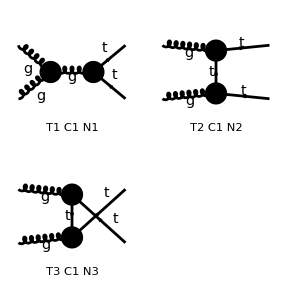

```mathematica
(* Diagrams gg -> ttbar*)
Diagramggttbar=InsertFields[Topology2to2,{V[5],V[5]}->{F[3,{3}],-F[3,{3}]}];
Paint[Diagramggttbar,ColumnsXRows->2];
```

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

in total: 1 Classes insertion

> Top. 1 aebe\cfdf\ef.m, 0 diagrams

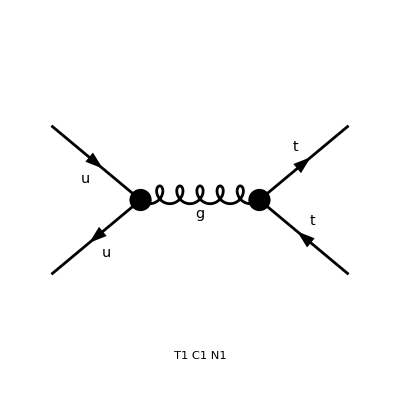

```mathematica
(* Diagrams gg -> ttbar*)
Diagramqqttbar=InsertFields[Topology2to2,{F[3,{1}],-F[3,{1}]}->{F[3,{3}],-F[3,{3}]},LastSelections->{V[5]}];
Paint[Diagramqqttbar,ColumnsXRows->2];
```

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

in total: 3 Classes insertions

> Top. 1 aebe\cfdf\ef.m, 0 diagrams

> Top. 2 aebf\cedf\ef.m, 0 diagrams

> Top. 3 aebf\cfde\ef.m, 0 diagrams

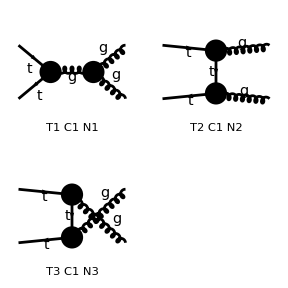

```mathematica
(* Diagrams ttbar -> gg *)
Diagramttbargg=InsertFields[Topology2to2,{F[3,{3}],-F[3,{3}]}->{V[5],V[5]}];
Paint[Diagramttbargg,ColumnsXRows->2];
```

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 5 Classes insertions

> Top. 3: 5 Classes insertions

> Top. 4: 0 Classes insertions

in total: 10 Classes insertions

> Top. 1 aebe\cfdf\ef.m, 0 diagrams

> Top. 2 aebf\cedf\ef.m, 0 diagrams

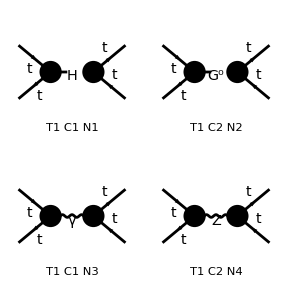

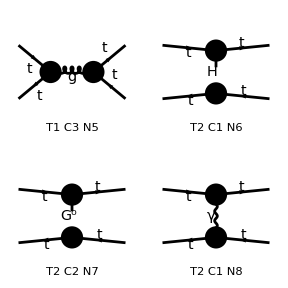

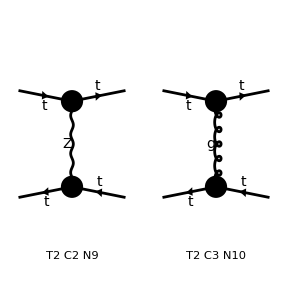

```mathematica
(* Diagrams ttbar -> ttbar *)
Diagramttbarttbar=InsertFields[Topology2to2,{F[3,{3}],-F[3,{3}]}->{F[3,{3}],-F[3,{3}]}];
Paint[Diagramttbarttbar,ColumnsXRows->2];
```

### Amplitudes

#### Generate amplitudes

```mathematica
(* gg -> ttbar *)
AmplitudeggttbarRaw=MyCreateFCAmp[Diagramggttbar];
(* qq -> ttbar *)
AmplitudeqqttbarRaw=MyCreateFCAmp[Diagramqqttbar];
(* qq -> ttbar *)
AmplitudettbarggRaw=MyCreateFCAmp[Diagramttbargg];
(* ttbar -> ttbar *)
DiagramttbarttbarRaw={MyCreateFCAmp[Diagramttbarttbar][[10]]};
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

creating amplitudes at level(s) {Classes}

> Top. 1: 5 Classes amplitudes

> Top. 2: 5 Classes amplitudes

in total: 10 Classes amplitudes

#### Functions to manipulate

```mathematica
(* Turn spinors and matrices to actual matrices *)
repDiracStructure={
Spinor[-Momentum[mom1_],mass1_,1].DiracStructure__.Spinor[Momentum[mom2_],mass2_, 1]->Hold[SpinorVBar[mom1,mass1].DiracStructure.SpinorU[mom2,mass2]],
Spinor[Momentum[mom1_],mass1_,1].DiracStructure__.Spinor[-Momentum[mom2_],mass2_, 1]->Hold[SpinorUBar[mom1,mass1].DiracStructure.SpinorV[mom2,mass2]],
SpinorVBar[mom_,mass_]:>BarDiracSpinorV[mom[0],ToThreeVector[mom],mass,mom],
SpinorUBar[mom_,mass_]:>BarDiracSpinorU[mom[0],ToThreeVector[mom],mass,mom],
SpinorU[mom_,mass_]:>DiracSpinorU[mom[0],ToThreeVector[mom],mass,mom],
SpinorV[mom_,mass_]:>DiracSpinorV[mom[0],ToThreeVector[mom],mass,mom],
DiracGamma[LorentzIndex[ind_]]:>GammaMatrix[LorentzIndex[ind]],
DiracGamma[Momentum[mom_]]:>Sum[GammaMatrix[LorentzIndex[ind]]*Pair[Momentum[mom],LorentzIndex[mu]]*Metric[mu,mu],{mu,0,3}]
};
repFourVector={
Pair[LorentzIndex[ind_],Momentum[mom_]]->mom[LorentzIndex[ind]],
Pair[Momentum[mom_],LorentzIndex[ind_]]->mom[LorentzIndex[ind]],
Pair[ind_,Momentum[mom_]]/;MemberQ[{0,1,2,3},ind]->mom[ind],
Pair[Momentum[mom_],ind_]/;MemberQ[{0,1,2,3},ind]->mom[ind]
};
```

```mathematica
(* Function to carry out summation over repeated Lorentz indices *)
RepeatedLorentzIndexSummation[exp_]:=Module[{RepeatedIndexList,Result},
Result=exp;
(* Look for all repeated Lorentz indices *)
RepeatedIndexList=DeleteDuplicates[Cases[exp,LorentzIndex[__],Infinity]];
(* For each repeated index, *)
Do[
(* Carry out summation over repeated index i *)
Result=Sum[Metric[mu,mu]*(Result//.{LorentzIndex[RepeatedIndexList[[i]]]->mu}),{mu,0,3}];
,{i,Length[RepeatedIndexList]}];
Return[Result];
]
```

```mathematica
(* Physical assumptions *)
AssumptionPhysicalggttbar={{InMom1[__],InMom2[__],OutMom1[__],OutMom2[__],FCGV[__],XiUp[__],XiDown[__],EtaUp[__],EtaDown[__],Xi[__],Eta[__],InMom1,InMom2,OutMom1,OutMom2,Phi[__],phi}∈Reals,Mtt>0,mt>0,mq>0,InMom1[0]>0,,InMom2[0]>0,,OutMom1[0]>0,OutMom2[0]>0,
p>=0,p1>=0,p2>=0,theta>=0,theta<=Pi,theta1>=0,theta1<=Pi,theta2>=0,theta2<=Pi,
Theta[__]>=0,Theta[__]<=Pi,Phi[__]>=0,Phi[__]<=2*Pi,phi>=0,phi<=2*Pi,phi1>=0,phi1<=2*Pi,phi2>=0,phi2<=2*Pi};
```

```mathematica
MomentumList={InMom1,InMom2,InMom3,InMom4,OutMom1,OutMom2,OutMom3,OutMom4};
```

```mathematica
(* Scalar products identities *)
repScalar2to2Prod={FCGV["MT"]->mt,FCGV["MU"]->mq,FCI[SP[OutMom1]]:>mt^2,FCI[SP[OutMom2]]:>mt^2,FCI[SP[InMom1]]:>0,FCI[SP[InMom2]]:>0,FCI[SP[OutMom1,OutMom2]]:>(Mtt^2-2*mt^2)/2,FCI[SP[InMom1,InMom2]]:>Mtt^2/2,FCI[SP[OutMom1,InMom1]]:>(mt^2-t)/2,FCI[SP[OutMom2,InMom1]]:>(mt^2-u)/2,FCI[SP[OutMom2,InMom2]]:>(mt^2-t)/2,FCI[SP[OutMom1,InMom2]]:>(mt^2-u)/2,mq->0};
repScalar2to2Dec={FCGV["MT"]->mt,FCGV["MU"]->mq,FCI[SP[OutMom1]]:>0,FCI[SP[OutMom2]]:>0,FCI[SP[InMom1]]:>mt^2,FCI[SP[InMom2]]:>mt^2,FCI[SP[OutMom1,OutMom2]]:>Mtt^2/2,FCI[SP[OutMom1,InMom1]]:>(mt^2-t)/2,FCI[SP[OutMom2,InMom1]]:>(mt^2-u)/2,FCI[SP[OutMom2,InMom2]]:>(mt^2-t)/2,FCI[SP[OutMom1,InMom2]]:>(mt^2-u)/2,mq->0};
```

```mathematica
repLeviCivita={EpsLC[i_,j_,k_,l_]:>Signature[{i,j,k,l}]};
```

```mathematica
repPolarization={Polarization[mom_,I][ind_]:>PolarizationEpsVectorZ[mom][[ind+1]],Polarization[mom_,-I][ind_]:>Conjugate[PolarizationEpsVectorZ[mom][[ind+1]]]};
```

```mathematica
(* Center-of-mass with z axis along the initial particle movement *)
rep2to2ProdCM=Join[{InMom1[1|2]->0,InMom2[1|2]->0,InMom1[0|3]->Mtt/2,InMom2[0]->Mtt/2,InMom2[3]->-Mtt/2,OutMom1[0]->Mtt/2,OutMom2[0]->Mtt/2,OutMom1[3]->p*Cos[theta],OutMom1[1]->p*Sin[theta]*Cos[phi],OutMom1[2]->p*Sin[theta]*Sin[phi],OutMom2[3]->-p*Cos[theta],OutMom2[1]->-p*Sin[theta]*Cos[phi],OutMom2[2]->-p*Sin[theta]*Sin[phi],Theta[InMom1]->0,Theta[InMom2]->0,Theta[OutMom1]->0,Theta[OutMom2]->0,Phi[__]->0,t:>mt^2-2*Sum[InMom1[i]*OutMom1[i]*Metric[i,i],{i,0,3}],u:>mt^2-2*Sum[InMom1[i]*OutMom2[i]*Metric[i,i],{i,0,3}]},repPolarization,repLeviCivita];
(*{InMom1[0]->Mtt/2,InMom2[0]->Mtt/2,InMom1[1]->-Mtt*Sin[theta]/2,InMom2[1]->Mtt*Sin[theta]/2,InMom1[2]->0,InMom2[2]->0,InMom1[3]->Mtt*Cos[theta]/2,InMom2[3]->-Mtt*Cos[theta]/2,OutMom1[0]->Mtt/2,OutMom2[0]->Mtt/2,OutMom1[3]->p,OutMom1[1|2]->0,OutMom2[3]->-p,OutMom2[1|2]->0};*)
rep2to2DecCM=Join[{InMom1[2]->0,InMom2[2]->0,InMom1[0]->Mtt/2,InMom2[0]->Mtt/2,InMom1[3]->-p*Sin[theta],InMom2[3]->p*Sin[theta],InMom1[3]->p*Cos[theta],InMom2[3]->-p*Cos[theta],OutMom1[0]->Mtt/2,OutMom2[0]->Mtt/2,OutMom1[1|2]->0,OutMom2[1|2]->0,OutMom1[3]->Mtt/2,OutMom2[3]->-Mtt/2,Phi[__]->0,Theta[InMom1]->0,Theta[InMom2]->0,Theta[OutMom1]->0,Theta[OutMom2]->0,t:>mt^2-2*Sum[InMom1[i]*OutMom1[i]*Metric[i,i],{i,0,3}],u:>mt^2-2*Sum[InMom1[i]*OutMom2[i]*Metric[i,i],{i,0,3}]},repPolarization,repLeviCivita];
```

```mathematica
(* Make expression looks nicer *)
repSimplify={InMom1->Subscript[k, 1],InMom2->Subscript[k, 2],OutMom1->Subscript[p, 1],OutMom2->Subscript[p, 2],Mtt->Subscript[M, tt],mt->Subscript[m, t],FCGV["MT"]->Subscript[m, t],Ftheta->θ,phi->ϕ,EtaUp->SubPlus[η],EtaDown->SubMinus[η],XiUp->SubPlus[ξ],XiDown->SubMinus[ξ],Eta[mom_,plus]->EtaUp[mom],Eta[mom_,minus]->EtaDown[mom],Xi[mom_,plus]->XiUp[mom],Xi[mom_,minus]->XiDown[mom],Pol[mom_,plus]->SubPlus[ε][mom],Pol[mom_,minus]->SubMinus[ε][mom],RelMom->p,OutMom->P,RelInMom->k};
```

```mathematica
(* Other *)
rep2to2NR={p->0,mt->Mtt/2,theta->0}; (* Non-relativistic *)
repIndices2to2NR={Glu1->a,Glu2->b,Glu5->c,Col3->i,Col4->j,Col1->l,Col2->n};
repToLaTeX2to2NR={
"M_{\\text{tt}}"->"\\Mtt",
"\\varepsilon _-\\left(k_2\\right)"->"\\varepsilon _{2-}","\\varepsilon _-\\left(k_1\\right)"->"\\varepsilon _{1-}",
"\\varepsilon _+\\left(k_2\\right)"->"\\varepsilon _{2+}","\\varepsilon _+\\left(k_1\\right)"->"\\varepsilon _{1+}",
"\\eta _+\\left(p_2\\right)"->"\\varsigma _{\\bart \\uparrow}","\\eta _-\\left(p_2\\right)"->"\\varsigma _{\\bart \\downarrow}",
"\\xi _+\\left(p_1\\right)"->"\\varsigma _{t \\uparrow}","\\xi _-\\left(p_1\\right)"->"\\varsigma _{t \\downarrow}",
"\\eta _+\\left(k_2\\right)"->"\\varsigma _{\\barq \\uparrow}","\\eta _-\\left(k_2\\right)"->"\\varsigma _{\\barq \\downarrow}",
"\\xi _+\\left(k_1\\right)"->"\\varsigma _{q \\uparrow}","\\xi _-\\left(k_1\\right)"->"\\varsigma _{q \\downarrow}",
"p^2"->"\\abs{\\bp^*}^2","{}^2"->"^2"};
```

```mathematica
(* Combine Dirac spinors and matrices evaluation operations *)
DiracEvaluate[exp_,repPre_:{},momentumList_:{}]:=Module[{Result},
Result=exp;
(* uncontract all momenta *)
Do[Result=Uncontract[Result,momentumList[[i]],Pair->{Polarization}],{i,Length[momentumList]}]; 
(* Turn Result into a list of mono terms *)
Result=Expand[Result//.repPre//.repDiracStructure//.{Eps->EpsLC}]//.repFourVector; (* In FeynCalc, Eps[0,__]=0 and Pair[0,__]=0, hence repFourVector and Eps->EpsLC *)
Result=If[Head[Result]===Plus,List@@Result,{Result}];
(* replace Dirac structure and enforce repeated indices summation individually for each term *)
Result=Total[RepeatedLorentzIndexSummation[#]&/@Result];
(* Release Hold and allow matrix multiplication to happen *)
Result=ReleaseHold[Result//.repPre]//.repFourVector;
If[Dimensions[Result]=={1,1},Return[Result[[1,1]]],Return[Result]]
];
```

```mathematica
(* Produce the replacement rule for setting Eta and Xi corresponding to Mom to up (SpinProj > 0) or down (SpinProj < 0) *)
repProjectSpin[Mom_,SpinProj_]:=If[Head[Mom]===List,Flatten[Table[repProjectSpin[Mom[[i]],SpinProj[[i]]],{i,Length[Mom]}]],
If[SpinProj>0,{Eta[Mom,plus]:>1,Eta[Mom,minus]->0,Xi[Mom,plus]:>1,Xi[Mom,minus]->0,Pol[Mom,plus]:>1,Pol[Mom,minus]->0},
If[SpinProj<0,{Eta[Mom,plus]:>0,Eta[Mom,minus]->1,Xi[Mom,plus]:>0,Xi[Mom,minus]->1,Pol[Mom,plus]:>0,Pol[Mom,minus]->1},Throw["SpinProj cannot be 0","InvalidArgument"]]]];
```

```mathematica
(* Extract spinor structure *)
ProjectSpinStructure[exp_,Sinit_,Minit_,Sfin_,Mfin_,OptionsPattern[{InMomList->{InMom1,InMom2},OutMomList->{OutMom1,OutMom2}}]]:=Module[{Result,InList,OutList},
InList=OptionValue[InMomList];
OutList=OptionValue[OutMomList];
If[Or[Length[InList]!=2,Length[OutList]!=2],Throw["Length of InMomList and OutMomList must be 2","InvalidArgument"]]; (* Assume only 2 incoming and 2 outgoing momenta *)
If[FreeQ[exp,Pol[__],Infinity],
If[And[Sinit==1,Minit==1],Result=(exp//.repProjectSpin[InList,{1,1}]),
If[And[Sinit==1,Minit==-1],Result=(exp//.repProjectSpin[InList,{-1,-1}]),
If[And[Sinit==1,Minit==0],Result=1/Sqrt[2]*((exp//.repProjectSpin[InList,{1,-1}])+(exp//.repProjectSpin[InList,{-1,1}])),
If[And[Sinit==0,Minit==0],Result=1/Sqrt[2]*((exp//.repProjectSpin[InList,{1,-1}])-(exp//.repProjectSpin[InList,{-1,1}])),Throw["Unrecognizable Sinit and/or Minit","InvalidArgument"];];];];];,
If[And[Sinit==2,Minit==2],Result=(exp//.repProjectSpin[InList,{1,1}]),
If[And[Sinit==2,Minit==-2],Result=(exp//.repProjectSpin[InList,{-1,-1}]),
If[And[Sinit==2,Minit==0],Result=1/Sqrt[2]*((exp//.repProjectSpin[InList,{1,-1}])+(exp//.repProjectSpin[InList,{-1,1}])),
If[And[Sinit==0,Minit==0],Result=1/Sqrt[2]*((exp//.repProjectSpin[InList,{1,-1}])-(exp//.repProjectSpin[InList,{-1,1}])),Throw["Unrecognizable Sinit and/or Minit","InvalidArgument"];];];];];];
If[And[Sfin==1,Mfin==1],Result=(Result//.repProjectSpin[OutList,{1,1}]),
If[And[Sfin==1,Mfin==-1],Result=(Result//.repProjectSpin[OutList,{-1,-1}]),
If[And[Sfin==1,Mfin==0],Result=1/Sqrt[2]*((Result//.repProjectSpin[OutList,{1,-1}])-(Result//.repProjectSpin[OutList,{-1,1}])),
If[And[Sfin==0,Mfin==0],Result=1/Sqrt[2]*((Result//.repProjectSpin[OutList,{1,-1}])+(Result//.repProjectSpin[OutList,{-1,1}])),Throw["Unrecognizable Sfin and/or Mfin","InvalidArgument"];];];];];
Return[Result//.{Pol[__,__]->1}];];
```

```mathematica
(* Compute spherical harmonics expansion *)
ProjectSphericalHarmonics[exp_,ll_,mm_,OptionsPattern[{angleL->theta,angleM->phi}]]:=
Assuming[OptionValue["angleL"]>0&&OptionValue["angleM"]>0,Simplify[Integrate[Simplify[exp*Conjugate[SphericalHarmonicY[ll,mm,OptionValue["angleL"],OptionValue["angleM"]]]]*Sin[OptionValue["angleL"]],{OptionValue["angleM"],0,2*Pi},{OptionValue["angleL"],0,Pi}]]];
(* Find all spherical harmonics *)
SphericalHarmonicExpansion[exp_,Lmax_,OptionsPattern[{MomentumRescale->1,angleL->theta,angleM->phi}]]:=Table[Table[{{ll,mm},(ProjectSphericalHarmonics[exp,ll,mm,angleL->OptionValue["angleL"],angleM->OptionValue["angleM"]])/(OptionValue["MomentumRescale"]^ll)},{mm,-ll,ll}],{ll,0,Lmax}];
```

```mathematica
(* Export to LaTeX *)
ToLaTeX[exp_,OptionsPattern[{repExp->{},repString->{}}]]:=StringReplace[ToString[TeXForm[exp//.OptionValue[repExp]]],OptionValue[repString]];
SphericalHarmonicCoeffLaTex[exp_,OptionsPattern[{repExp->{},repString->{},coeffSuperscript->"",Prefactor->1}]]:=Module[{CoeffList,Output,superscript,RHSOutput},
CoeffList=Flatten[exp,1];
superscript="^{"<>OptionValue["coeffSuperscript"]<>"}";
Output="";
Do[If[Not[CoeffList[[inc]][[2]]===0],
RHSOutput=ToLaTeX[CoeffList[[inc]][[2]],repExp->OptionValue["repExp"],repString->OptionValue["repString"]];
If[Not[OptionValue["Prefactor"]===1],
If[Head[CoeffList[[inc]][[2]]]===Plus,RHSOutput="\\qty["<>RHSOutput<>"]"<>ToString[OptionValue["Prefactor"]],
RHSOutput=RHSOutput<>ToString[OptionValue["Prefactor"]]]];
Output=Output<>"a"<>superscript<>"_{"<>ToString[CoeffList[[inc]][[1,1]]]<>ToString[CoeffList[[inc]][[1,2]]]<>"} &= "<>RHSOutput<>", \\nn\n";
],{inc,Length[CoeffList]}];
Output=StringDrop[Output,-6];
Return[Output];
]
```

```mathematica
(* Impose physical, CM, and simplification conditions *)
SimplifyCM[exp_,repCM_:{},repScalar_:{},AssumptionPhysical_:{}]:=Simplify[%//.repCM//.repScalar,Assumptions->AssumptionPhysical];
```

#### Manipulate

```mathematica
Amplitudeqqttbar=FeynAmpDenominatorExplicit[DiracSimplify[AmplitudeqqttbarRaw,DiracSubstitute67->True]];
Amplitudeggttbar=FeynAmpDenominatorExplicit[Simplify[DiracSimplify[AmplitudeggttbarRaw,DiracSubstitute67->True]]];
Amplitudettbargg=FeynAmpDenominatorExplicit[Simplify[DiracSimplify[AmplitudettbarggRaw,DiracSubstitute67->True]]];
Diagramttbarttbar=FeynAmpDenominatorExplicit[Simplify[DiracSimplify[DiagramttbarttbarRaw,DiracSubstitute67->True]]];
```

#### Projection operators

```mathematica
repInitialCM={Spinor[-Momentum[InMom2],0,1].DiracGamma[Momentum[mom_]].Spinor[Momentum[InMom1],0,1]->-2Sqrt[2]*EnCM*Pair[Momentum[mom],Momentum[Polarization[InMom,I]]],EnCM->Sqrt[SP[InMom1+InMom2]/2]};
repFinalMomenta={OutMom1->OutMom/2+RelMom,OutMom2->OutMom/2-RelMom};
repOnshell={FCI[SP[mom_,Polarization[mom_,-I]]]->0};
repOnshell2to2={FCI[SP[OutMom,Polarization[mom_,__]]]->0,FCI[SP[InMom1,Polarization[InMom1,__]]]->0,FCI[SP[InMom1,Polarization[InMom2,__]]]->0,FCI[SP[InMom2,Polarization[InMom1,__]]]->0,FCI[SP[InMom2,Polarization[InMom2,__]]]->0};
```

```mathematica
(* ttbar -> ttbar *)
Print["Spin singlet: ", DiracSimplify[Total[ProjectSpinProduction[Diagramttbarttbar,0]]]]
```

Throw::nocatch: Uncaught Throw[Too many spinors detected] returned to top level.

Hold[Throw[Too many spinors detected]]

```mathematica
(* qq -> ttbar *)
Print["Spin singlet: ", DiracSimplify[Total[ProjectSpinProduction[Amplitudeqqttbar,0]]]]
Simplify[ DiracSimplify[Total[ProjectSpinProduction[Amplitudeqqttbar,1]]]];
SimplifyCM[%,rep2to2ProdCM,repScalar2to2Prod,AssumptionPhysicalggttbar]//.repInitialCM;
ExpandScalarProduct[%]//.repScalar2to2Prod;
SimplifyCM[%,rep2to2ProdCM,repScalar2to2Prod,AssumptionPhysicalggttbar];
FullSimplify[ExpandScalarProduct[FCReplaceMomenta[%,repFinalMomenta]]//.repOnshell];
Print["Spin triplet: ",%//.repSimplify]
```

Spin singlet: 0

Spin triplet: -(2 √2 g_s^2 (4 (p̄·ε̄(InMom)) (p̄·(ε̄)^*(P))+(ε̄(InMom)·(ε̄)^*(P)) M_tt (2 m_t+M_tt)) T_Col2Col1^Glu5 T_Col3Col4^Glu5)/(M_tt (2 m_t+M_tt))

```mathematica
(* gg -> ttbar, s-channel *)
Simplify[DiracSimplify[ProjectSpinProduction[Amplitudeggttbar[[1]],0]]];
Print["Spin singlet: ", %//.repSimplify];
%%;
DiracEvaluate[%,repScalar2to2Prod,MomentumList];
Print["Spin singlet in CM frame: ",FullSimplify[SimplifyCM[%,rep2to2ProdCM,repScalar2to2Prod,AssumptionPhysicalggttbar]//.repSimplify]];
Simplify[ DiracSimplify[ProjectSpinProduction[Amplitudeggttbar[[1]],1]]];
SimplifyCM[%,{},repScalar2to2Prod,AssumptionPhysicalggttbar]//.repInitialCM;
ExpandScalarProduct[%]//.repScalar2to2Prod;
SimplifyCM[%,{},repScalar2to2Prod,AssumptionPhysicalggttbar];
FullSimplify[ExpandScalarProduct[FCReplaceMomenta[%,repFinalMomenta]]//.repOnshell//.repOnshell2to2];
Print["Spin triplet: ",%//.repSimplify]
```

Spin singlet: 0

Spin singlet in CM frame: 0

Spin triplet: -(ⅈ √2 (ε̄(k_1)·ε̄(k_2)) g_s^2 (2 (u-t) (p̄·(ε̄)^*(P))+((ε̄)^*(P)·(k̄)_1-(ε̄)^*(P)·(k̄)_2) M_tt (2 m_t+M_tt)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(M_tt^2 (2 m_t+M_tt))

```mathematica
(* gg -> ttbar, t-channel *)
Simplify[DiracSimplify[ProjectSpinProduction[Amplitudeggttbar[[2]],0]]];
Print["Spin singlet: ", DiracSimplify[EpsEvaluate[FCReplaceMomenta[%//.repScalar2to2Prod,{InMom1->OutMom/2+RelInMom/2,InMom2->OutMom/2-RelInMom/2,OutMom1->OutMom/2+RelMom/2,OutMom2->OutMom/2-RelMom/2}]]]//.repSimplify];
Simplify[%%//.repScalar2to2Prod]
DiracEvaluate[%,repScalar2to2Prod,MomentumList];
Print["Spin singlet in CM frame: ",FullSimplify[SimplifyCM[%,rep2to2ProdCM,repScalar2to2Prod,AssumptionPhysicalggttbar]//.repSimplify]];
Simplify[ DiracSimplify[ProjectSpinProduction[Amplitudeggttbar[[2]],1]]];
SimplifyCM[%,{},repScalar2to2Prod,AssumptionPhysicalggttbar]//.repInitialCM;
ExpandScalarProduct[%]//.repScalar2to2Prod;
SimplifyCM[%,{},repScalar2to2Prod,AssumptionPhysicalggttbar];
FullSimplify[ExpandScalarProduct[FCReplaceMomenta[%,repFinalMomenta]]//.repOnshell//.repOnshell2to2];
tmpt=Simplify[%//.repSimplify//.{t+u->2*Subscript[m, t]^2-Subscript[M, tt]^2,-t-u->-2*Subscript[m, t]^2+Subscript[M, tt]^2}];
Print["Spin triplet: ",%]
```

Spin singlet: -(2 ⅈ √2 g_s^2 (-1/4 (ϵ̄)^(P̄ k̄ p̄ ε̄(k_2)) (((P̄)/2-(p̄)/2)·ε̄(k_1))+1/4 (ϵ̄)^(P̄ k̄ p̄ ε̄(k_1)) (((P̄)/2-(p̄)/2)·ε̄(k_2))+1/4 (ϵ̄)^(P̄ p̄ ε̄(k_1)ε̄(k_2)) (m_t^2-t)+(-1/4 (ϵ̄)^(k̄ p̄ ε̄(k_1)ε̄(k_2))+1/4 (ϵ̄)^(P̄ k̄ ε̄(k_1)ε̄(k_2))+1/4 (ϵ̄)^(P̄ p̄ ε̄(k_1)ε̄(k_2))) m_t (m_t+M_tt)+(1/4 (ϵ̄)^(k̄ p̄ ε̄(k_1)ε̄(k_2))+1/4 (ϵ̄)^(P̄ k̄ ε̄(k_1)ε̄(k_2))-1/4 (ϵ̄)^(P̄ p̄ ε̄(k_1)ε̄(k_2))) (2 m_t^2+M_tt m_t+1/2 (M_tt^2-2 m_t^2))) T_Col3Col5^Glu1 T_Col5Col4^Glu2)/((m_t^2-t) M_tt (2 m_t+M_tt))

-1/(Mtt (2 mt+Mtt) (mt^2-t))2 ⅈ √2 g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 (1/2 (2 mt^2+2 mt Mtt+Mtt^2) (ϵ̄)^(OverBar[InMom2]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2))-1/2 (mt^2-t) (ϵ̄)^(OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2))+mt (mt+Mtt) (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]ε̄(InMom1)ε̄(InMom2))+(OverBar[OutMom2]·ε̄(InMom1)) (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom2))-(OverBar[OutMom2]·ε̄(InMom2)) (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom1)))

Spin singlet in CM frame: (g_s^2 ((2 m_t+M_tt)^2-4 p^2) T_Col3Col5^Glu1 T_Col5Col4^Glu2 (ε_-(k_2) ε_+(k_1)-ε_-(k_1) ε_+(k_2)))/(√2 (M_tt-2 p cos(theta)) (2 m_t+M_tt))

Spin triplet: -(√2 g_s^2 ((p̄·(ε̄)^*(P)) (8 (p̄·ε̄(k_1)) (p̄·ε̄(k_2))+(u-t) (ε̄(k_1)·ε̄(k_2)))+((p̄·ε̄(k_2)) ((ε̄)^*(P)·ε̄(k_1))+(p̄·ε̄(k_1)) ((ε̄)^*(P)·ε̄(k_2))-((ε̄)^*(P)·(k̄)_2) (ε̄(k_1)·ε̄(k_2))) M_tt (2 m_t+M_tt)) T_Col3Col5^Glu1 T_Col5Col4^Glu2)/((t-m_t^2) (2 m_t+M_tt))

```mathematica
repScalar2to2Prod
```

{FCGV(MT)→mt,FCGV(MU)→mq,OverBar[OutMom1]^2:>mt^2,OverBar[OutMom2]^2:>mt^2,OverBar[InMom1]^2:>0,OverBar[InMom2]^2:>0,OverBar[OutMom1]·OverBar[OutMom2]:>1/2 (Mtt^2-2 mt^2),OverBar[InMom1]·OverBar[InMom2]:>Mtt^2/2,OverBar[InMom1]·OverBar[OutMom1]:>1/2 (mt^2-t),OverBar[InMom1]·OverBar[OutMom2]:>1/2 (mt^2-u),OverBar[InMom2]·OverBar[OutMom2]:>1/2 (mt^2-t),OverBar[InMom2]·OverBar[OutMom1]:>1/2 (mt^2-u),mq→0}

```mathematica
(* gg -> ttbar, u-channel *)
Simplify[DiracSimplify[ProjectSpinProduction[Amplitudeggttbar[[3]],0]]];
Print["Spin singlet: ", %//.repScalar2to2Prod//.repSimplify];
%%;
DiracEvaluate[%,repScalar2to2Prod,MomentumList];
Print["Spin singlet in CM frame: ",FullSimplify[SimplifyCM[%,rep2to2ProdCM,repScalar2to2Prod,AssumptionPhysicalggttbar]//.repSimplify]];
Simplify[ DiracSimplify[ProjectSpinProduction[Amplitudeggttbar[[3]],1]]];
SimplifyCM[%,{},repScalar2to2Prod,AssumptionPhysicalggttbar]//.repInitialCM;
ExpandScalarProduct[%]//.repScalar2to2Prod;
SimplifyCM[%,{},repScalar2to2Prod,AssumptionPhysicalggttbar];
FullSimplify[ExpandScalarProduct[FCReplaceMomenta[%,repFinalMomenta]]//.repOnshell//.repOnshell2to2];
tmpu=Simplify[%//.{t+u->2*mt^2-s,-t-u->s-2*mt^2}//.repSimplify];
Print["Spin triplet: ",%]
```

Spin singlet: -(2 ⅈ √2 g_s^2 ((ϵ̄)^((k̄)_2(p̄)_1(p̄)_2 ε̄(k_2)) (ε̄(k_1)·(p̄)_2)-(ϵ̄)^((k̄)_2(p̄)_1(p̄)_2 ε̄(k_1)) (ε̄(k_2)·(p̄)_2)-1/2 (ϵ̄)^((p̄)_1(p̄)_2 ε̄(k_1)ε̄(k_2)) (m_t^2-t)+(ϵ̄)^((k̄)_2(p̄)_1 ε̄(k_1)ε̄(k_2)) m_t (m_t+M_tt)+(ϵ̄)^((k̄)_2(p̄)_2 ε̄(k_1)ε̄(k_2)) (2 m_t^2+M_tt m_t+1/2 (M_tt^2-2 m_t^2))) T_Col5Col4^Glu1 T_Col3Col5^Glu2)/((m_t^2-u) M_tt (2 m_t+M_tt))

Spin singlet in CM frame: (g_s^2 ((2 m_t+M_tt)^2-4 p^2) T_Col5Col4^Glu1 T_Col3Col5^Glu2 (ε_-(k_2) ε_+(k_1)-ε_-(k_1) ε_+(k_2)))/(√2 (2 p cos(theta)+M_tt) (2 m_t+M_tt))

Spin triplet: (√2 g_s^2 ((p̄·ε̄(k_2)) ((ε̄)^*(P)·ε̄(k_1)) (2 m_t+M_tt) (2 M_tt^2-s)+(p̄·ε̄(k_1)) (8 (p̄·(ε̄)^*(P)) (p̄·ε̄(k_2)) M_tt+s ((ε̄)^*(P)·ε̄(k_2)) (2 m_t+M_tt))+(ε̄(k_1)·ε̄(k_2)) M_tt ((t-u) (p̄·(ε̄)^*(P))+((ε̄)^*(P)·(k̄)_2) M_tt (2 m_t+M_tt))) T_Col5Col4^Glu1 T_Col3Col5^Glu2)/((m_t^2-u) M_tt (2 m_t+M_tt))

#### Explicit forms

```mathematica
(* qq -> ttbar *)
tmpSqq=1;tmpMqq=-1;tmpStt=1;tmpMtt=-1;
DiracEvaluate[Total[Amplitudeqqttbar],repScalar2to2Prod];
SimplifyCM[%,rep2to2ProdCM,repScalar2to2Prod,AssumptionPhysicalggttbar];
FullSimplify[%,Assumptions->AssumptionPhysicalggttbar];
%//.repSimplify
FullSimplify[%%//.rep2to2NR,Assumptions->AssumptionPhysicalggttbar]//.repSimplify
ToLaTeX[%%,repExp->repIndices2to2NR,repString->repToLaTeX2to2NR]
FullSimplify[ProjectSpinStructure[%%%%,tmpSqq,tmpMqq,tmpStt,tmpMtt]];
%//.repSimplify
ToLaTeX[TrigExpand[Simplify[%%/(SMP["g_s"]^2*SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col2],SUNFIndex[Col1]]*SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col3],SUNFIndex[Col4]]/(Subscript[M, tt]*(Subscript[M, tt]+2*Subscript[m, t])))]],repExp->repIndices2to2NR,repString->Join[repToLaTeX2to2NR,{"(\\theta )"->"\\theta"}]]
tmp=SUNSimplify[%%%*Sqrt[2]*SUNTF[{I},Col4,Col3]]/(Sqrt[2*Pi]*SMP["g_s"]^2*SUNTF[{SUNIndex[I]},SUNFIndex[Col2],SUNFIndex[Col1]]/(Mtt*(2*mt+Mtt)));
FullSimplify[SphericalHarmonicExpansion[%,4,MomentumRescale->p]]
SphericalHarmonicCoeffLaTex[%//.repSimplify,repExp->repIndices2to2NR,repString->Join[repToLaTeX2to2NR,{"(\\theta )"->"\\theta"}],coeffSuperscript->"\\ket{"<>ToString[tmpSqq]<>","<>ToString[tmpMqq]<>"}_{q\\bar q} \\to \\ket{"<>ToString[tmpStt]<>","<>ToString[tmpMtt]<>"}_{t\\bar t}",Prefactor->"F^I_{nl}"]
```

1/(M_tt (2 m_t+M_tt))g_s^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (ⅇ^(-2 ⅈ ϕ) η_-(k_2) ξ_-(k_1) (ⅇ^(2 ⅈ ϕ) η_-(p_2) ξ_-(p_1) ((2 m_t+M_tt)^2+4 p^2 cos^2(theta))+2 p^2 ⅇ^(ⅈ ϕ) sin(2 theta) (η_+(p_2) ξ_-(p_1)-η_-(p_2) ξ_+(p_1))-4 p^2 η_+(p_2) ξ_+(p_1) sin^2(theta))+η_+(k_2) ξ_+(k_1) (η_+(p_2) ξ_+(p_1) ((2 m_t+M_tt)^2+4 p^2 cos^2(theta))-4 p^2 ⅇ^(2 ⅈ ϕ) η_-(p_2) ξ_-(p_1) sin^2(theta)+2 p^2 ⅇ^(ⅈ ϕ) sin(2 theta) (η_+(p_2) ξ_-(p_1)-η_-(p_2) ξ_+(p_1))))

2 g_s^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (η_-(k_2) ξ_-(k_1) η_-(p_2) ξ_-(p_1)+η_+(k_2) ξ_+(k_1) η_+(p_2) ξ_+(p_1))

\frac{g_s^2 T_{ij}^c T_{nl}^c \left(e^{-2 i \phi } \varsigma _{\barq \downarrow} \varsigma _{q \downarrow} \left(e^{2 i \phi } \varsigma _{\bart \downarrow} \varsigma _{t \downarrow} \left(\left(2 m_t+\Mtt\right)^2+4 \abs{\bp^*}^2 \cos ^2(\theta )\right)+2 \abs{\bp^*}^2 e^{i \phi } \sin (2 \theta ) \left(\varsigma _{\bart \uparrow} \varsigma _{t \downarrow}-\varsigma _{\bart \downarrow} \varsigma _{t \uparrow}\right)-4 \abs{\bp^*}^2 \varsigma _{\bart \uparrow} \varsigma _{t \uparrow} \sin ^2(\theta )\right)+\varsigma _{\barq \uparrow} \varsigma _{q \uparrow} \left(\varsigma _{\bart \uparrow} \varsigma _{t \uparrow} \left(\left(2 m_t+\Mtt\right)^2+4 \abs{\bp^*}^2 \cos ^2(\theta )\right)-4 \abs{\bp^*}^2 e^{2 i \phi } \varsigma _{\bart \downarrow} \varsigma _{t \downarrow} \sin ^2(\theta )+2 \abs{\bp^*}^2 e^{i \phi } \sin (2 \theta ) \left(\varsigma _{\bart \uparrow} \varsigma _{t \downarrow}-\varsigma _{\bart \downarrow} \varsigma _{t \uparrow}\right)\right)\right)}{\Mtt \left(2 m_t+\Mtt\right)}

(g_s^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((2 m_t+M_tt)^2+4 p^2 cos^2(theta)))/(M_tt (2 m_t+M_tt))

\frac{8 \text{mt}^2 m_t \Mtt}{\text{Mtt} (2 \text{mt}+\text{Mtt})}+\frac{8 \abs{\bp^*}^2 m_t \Mtt \cos ^2\theta}{\text{Mtt} (2 \text{mt}+\text{Mtt})}+\frac{8 \text{mt} m_t \Mtt}{2 \text{mt}+\text{Mtt}}+\frac{2 \text{Mtt} m_t \Mtt}{2 \text{mt}+\text{Mtt}}+\frac{4 \text{mt}^2 \Mtt^2}{\text{Mtt} (2 \text{mt}+\text{Mtt})}+\frac{4 \abs{\bp^*}^2 \Mtt^2 \cos ^2\theta}{\text{Mtt} (2 \text{mt}+\text{Mtt})}+\frac{4 \text{mt} \Mtt^2}{2 \text{mt}+\text{Mtt}}+\frac{\text{Mtt} \Mtt^2}{2 \text{mt}+\text{Mtt}}

{({0,0} | (2 mt+Mtt)^2+(4 p^2)/3),({1,-1} | 0
{1,0} | 0
{1,1} | 0),({2,-2} | 0
{2,-1} | 0
{2,0} | 8/(3 √5)
{2,1} | 0
{2,2} | 0),({3,-3} | 0
{3,-2} | 0
{3,-1} | 0
{3,0} | 0
{3,1} | 0
{3,2} | 0
{3,3} | 0),({4,-4} | 0
{4,-3} | 0
{4,-2} | 0
{4,-1} | 0
{4,0} | 0
{4,1} | 0
{4,2} | 0
{4,3} | 0
{4,4} | 0)}

a^{\ket{1,-1}_{q\bar q} \to \ket{1,-1}_{t\bar t}}_{00} &= \qty[\left(2 m_t+\Mtt\right)^2+\frac{4 \abs{\bp^*}^2}{3}]F^I_{nl}, \nn
a^{\ket{1,-1}_{q\bar q} \to \ket{1,-1}_{t\bar t}}_{20} &= \frac{8}{3 \sqrt{5}}F^I_{nl}

```mathematica
(* gg -> ttbar (s-channel) *)
tmpSgg=2;tmpMgg=0;tmpStt=1;tmpMtt=1;
DiracEvaluate[Amplitudeggttbar[[1]],repScalar2to2Prod,MomentumList];
SimplifyCM[%,rep2to2ProdCM,repScalar2to2Prod,AssumptionPhysicalggttbar];
FullSimplify[%];
%//.repSimplify
Factor[Expand[FullSimplify[%%//.rep2to2NR]]]//.repSimplify
ToLaTeX[%%,repExp->repIndices2to2NR,repString->repToLaTeX2to2NR]
FullSimplify[ProjectSpinStructure[%%%%,tmpSgg,tmpMgg,tmpStt,tmpMtt]];
%//.repSimplify
ToLaTeX[FullSimplify[%/(I*SMP["g_s"]^2*SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu5]]*SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col3],SUNFIndex[Col4]]/(Subscript[M, tt]*(Subscript[M, tt]+2*Subscript[m, t])))],repExp->repIndices2to2NR,repString->Join[repToLaTeX2to2NR,{"(\\theta )"->"\\theta"}]]
tmp=SUNSimplify[%%%*Sqrt[2]*SUNTF[{I},Col4,Col3]]/(Sqrt[2*Pi]*SMP["g_s"]^2*I*SUNF[SUNIndex[I],SUNIndex[Glu1],SUNIndex[Glu2]]/(Mtt*(2*mt+Mtt)));
FullSimplify[SphericalHarmonicExpansion[%,4,MomentumRescale->p]]
SphericalHarmonicCoeffLaTex[%//.repSimplify,repExp->repIndices2to2NR,repString->Join[repToLaTeX2to2NR,{"(\\theta )"->"\\theta"}],coeffSuperscript->"\\ket{"<>ToString[tmpSgg]<>","<>ToString[tmpMgg]<>"}_{gg} \\to \\ket{"<>ToString[tmpStt]<>","<>ToString[tmpMtt]<>"}_{t\\bar t}",Prefactor->"F^{Iab}"]
```

(g_s^2 (ε_-(k_2) ε_+(k_1)+ε_-(k_1) ε_+(k_2)) T_Col3Col4^Glu5 f^Glu1Glu2Glu5 (ⅈ (η_+(p_2) ξ_-(p_1)-η_-(p_2) ξ_+(p_1)) ((2 m_t+M_tt)^2-4 p^2 cos(2 theta))+4 p^2 sin(2 theta) sin(ϕ) (η_+(p_2) ξ_+(p_1)-η_-(p_2) ξ_-(p_1))+4 ⅈ p^2 sin(2 theta) cos(ϕ) (η_-(p_2) ξ_-(p_1)+η_+(p_2) ξ_+(p_1))))/(2 M_tt (2 m_t+M_tt))

ⅈ g_s^2 (ε_-(k_2) ε_+(k_1)+ε_-(k_1) ε_+(k_2)) (η_+(p_2) ξ_-(p_1)-η_-(p_2) ξ_+(p_1)) T_Col3Col4^Glu5 f^Glu1Glu2Glu5

\frac{g_s^2 \left(\varepsilon _{2-} \varepsilon _{1+}+\varepsilon _{1-} \varepsilon _{2+}\right) f^{abc} T_{ij}^c \left(i \left(\varsigma _{\bart \uparrow} \varsigma _{t \downarrow}-\varsigma _{\bart \downarrow} \varsigma _{t \uparrow}\right) \left(\left(2 m_t+\Mtt\right)^2-4 \abs{\bp^*}^2 \cos (2 \theta )\right)+4 \abs{\bp^*}^2 \sin (2 \theta ) \sin (\phi ) \left(\varsigma _{\bart \uparrow} \varsigma _{t \uparrow}-\varsigma _{\bart \downarrow} \varsigma _{t \downarrow}\right)+4 i \abs{\bp^*}^2 \sin (2 \theta ) \cos (\phi ) \left(\varsigma _{\bart \downarrow} \varsigma _{t \downarrow}+\varsigma _{\bart \uparrow} \varsigma _{t \uparrow}\right)\right)}{2 \Mtt \left(2 m_t+\Mtt\right)}

(2 √2 p^2 g_s^2 sin(2 theta) (sin(ϕ)+ⅈ cos(ϕ)) T_Col3Col4^Glu5 f^Glu1Glu2Glu5)/(M_tt (2 m_t+M_tt))

4 \sqrt{2} \abs{\bp^*}^2 e^{-i \phi } \sin \theta \cos \theta

{({0,0} | 0),({1,-1} | 0
{1,0} | 0
{1,1} | 0),({2,-2} | 0
{2,-1} | 8/(√15)
{2,0} | 0
{2,1} | 0
{2,2} | 0),({3,-3} | 0
{3,-2} | 0
{3,-1} | 0
{3,0} | 0
{3,1} | 0
{3,2} | 0
{3,3} | 0),({4,-4} | 0
{4,-3} | 0
{4,-2} | 0
{4,-1} | 0
{4,0} | 0
{4,1} | 0
{4,2} | 0
{4,3} | 0
{4,4} | 0)}

a^{\ket{2,0}_{gg} \to \ket{1,1}_{t\bar t}}_{2-1} &= \frac{8}{\sqrt{15}}F^{Iab}

```mathematica
(* gg -> ttbar (s+t+u-channel) *)
tmpSgg=2;tmpMgg=0;tmpStt=1;tmpMtt=0;
DiracEvaluate[#,repScalar2to2Prod,MomentumList]&/@Amplitudeggttbar;
SimplifyCM[%,rep2to2ProdCM,repScalar2to2Prod,AssumptionPhysicalggttbar];
Collect[%,{Pol[__],Xi[__],Eta[__]},FullSimplify];
%//.repSimplify;
Factor[Expand[FullSimplify[%%//.rep2to2NR]]]//.repSimplify;
FullSimplify[ProjectSpinStructure[%%%,tmpSgg,tmpMgg,tmpStt,tmpMtt]];
%//.repSimplify
ToLaTeX[FullSimplify[%/(SMP["g_s"]^2*SUNTF[{SUNIndex[Glu1]},SUNFIndex[Col3],SUNFIndex[Col5]]*SUNTF[{SUNIndex[Glu2]},SUNFIndex[Col5],SUNFIndex[Col4]]/(Subscript[M, tt]*(Subscript[M, tt]+2*Subscript[m, t])*(Subscript[M, tt]-2*p*Cos[θ])))]//.{p->mom},repExp->repIndices2to2NR,repString->Join[repToLaTeX2to2NR,{"(\\theta )"->"\\theta","\\text{mom}"->"\\abs{\\bp^*}","\\r "->"\\r"}]]
tmp=Simplify[
SUNSimplify[%%%*Sqrt[2]*SUNTF[{I},Col4,Col3]]/(Sqrt[2*Pi]*SMP["g_s"]^2/(Mtt*(2*mt+Mtt)))]
Simplify[Total[tmp]//.{p->xp*Mtt}];
Simplify[Normal[Series[%,{xp,0,4}]]//.{xp->p/Mtt}]
Simplify[TrigExpand[SphericalHarmonicExpansion[%,4,MomentumRescale->p]]]
Simplify[%//.{p->0}]
```

{0,(g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 (2 m_t+M_tt-2 p) (2 m_t+M_tt+2 p))/((2 m_t+M_tt) (M_tt-2 p cos(theta))),(g_s^2 T_Col3Col5^Glu2 T_Col5Col4^Glu1 (2 m_t+M_tt-2 p) (2 m_t+M_tt+2 p))/((2 m_t+M_tt) (M_tt+2 p cos(theta)))}

\left\{0,\frac{\Mtt \left(2 m_t+\Mtt-2 \abs{\bp^*}\right) \left(2 \left(m_t+\abs{\bp^*}\right)+\Mtt\right) \left(\Mtt-2 \abs{\bp^*} \cos \theta\right)}{\Mtt-2 \abs{\bp^*} \cos \theta},\frac{\Mtt T_{\text{Col5}j}^a T_{i\text{Col5}}^b \left(2 m_t+\Mtt-2 \abs{\bp^*}\right) \left(2 \left(m_t+\abs{\bp^*}\right)+\Mtt\right) \left(\Mtt-2 \abs{\bp^*} \cos \theta\right)}{T_{i\text{Col5}}^a T_{\text{Col5}j}^b \left(\Mtt+2 \abs{\bp^*} \cos \theta\right)}\right\}

{0,(Mtt (2 mt+Mtt-2 p) (2 mt+Mtt+2 p) (d^ⅈGlu1Glu2+ⅈ f^ⅈGlu1Glu2))/(4 √π (Mtt-2 p cos(theta))),(Mtt (2 mt+Mtt-2 p) (2 mt+Mtt+2 p) (d^ⅈGlu1Glu2-ⅈ f^ⅈGlu1Glu2))/(4 √π (Mtt+2 p cos(theta)))}

1/(2 √π Mtt^4)(d^ⅈGlu1Glu2 (4 Mtt^2 p^2 cos^2(theta) (4 mt^2+4 mt Mtt+Mtt^2-4 p^2)+Mtt^4 (4 mt^2+4 mt Mtt+Mtt^2-4 p^2)+16 p^4 (2 mt+Mtt)^2 cos^4(theta))+2 ⅈ Mtt p cos(theta) f^ⅈGlu1Glu2 (4 mt^2 (Mtt^2+2 p^2)+4 mt (Mtt^3+2 Mtt p^2)+2 p^2 (2 mt+Mtt)^2 cos(2 theta)+Mtt^4-2 Mtt^2 p^2))

{({0,0} | (d^ⅈGlu1Glu2 (4 mt^2 (15 Mtt^4+20 Mtt^2 p^2+48 p^4)+4 mt (15 Mtt^5+20 Mtt^3 p^2+48 Mtt p^4)+15 Mtt^6-40 Mtt^4 p^2-32 Mtt^2 p^4))/(15 Mtt^4)),({1,-1} | 0
{1,0} | (2 ⅈ f^ⅈGlu1Glu2 (4 mt^2 (5 Mtt^2+12 p^2)+4 mt (5 Mtt^3+12 Mtt p^2)+5 Mtt^4-8 Mtt^2 p^2))/(5 √3 Mtt^3)
{1,1} | 0),({2,-2} | 0
{2,-1} | 0
{2,0} | (8 d^ⅈGlu1Glu2 (4 mt^2 (7 Mtt^2+24 p^2)+4 mt (7 Mtt^3+24 Mtt p^2)+7 Mtt^4-4 Mtt^2 p^2))/(21 √5 Mtt^4)
{2,1} | 0
{2,2} | 0),({3,-3} | 0
{3,-2} | 0
{3,-1} | 0
{3,0} | (16 ⅈ (2 mt+Mtt)^2 f^ⅈGlu1Glu2)/(5 √7 Mtt^3)
{3,1} | 0
{3,2} | 0
{3,3} | 0),({4,-4} | 0
{4,-3} | 0
{4,-2} | 0
{4,-1} | 0
{4,0} | (128 (2 mt+Mtt)^2 d^ⅈGlu1Glu2)/(105 Mtt^4)
{4,1} | 0
{4,2} | 0
{4,3} | 0
{4,4} | 0)}

{({0,0} | (2 mt+Mtt)^2 d^ⅈGlu1Glu2),({1,-1} | 0
{1,0} | (2 ⅈ (2 mt+Mtt)^2 f^ⅈGlu1Glu2)/(√3 Mtt)
{1,1} | 0),({2,-2} | 0
{2,-1} | 0
{2,0} | (8 (2 mt+Mtt)^2 d^ⅈGlu1Glu2)/(3 √5 Mtt^2)
{2,1} | 0
{2,2} | 0),({3,-3} | 0
{3,-2} | 0
{3,-1} | 0
{3,0} | (16 ⅈ (2 mt+Mtt)^2 f^ⅈGlu1Glu2)/(5 √7 Mtt^3)
{3,1} | 0
{3,2} | 0
{3,3} | 0),({4,-4} | 0
{4,-3} | 0
{4,-2} | 0
{4,-1} | 0
{4,0} | (128 (2 mt+Mtt)^2 d^ⅈGlu1Glu2)/(105 Mtt^4)
{4,1} | 0
{4,2} | 0
{4,3} | 0
{4,4} | 0)}

```mathematica
RhoFunction[l_,m_]:=Sqrt[Pi]/Gamma[l+1/2]*Sqrt[(l+m)!(l-m)!/(2*l+1)]/Mtt^(l-2)*EpsFunction[l]
EpsFunction[l_]:=If[OddQ[l],SUND[SUNIndex[I],SUNIndex[Glu1],SUNIndex[Glu2]],I*SUNF[SUNIndex[I],SUNIndex[Glu1],SUNIndex[Glu2]]]
Simplify[Expand[Table[-RhoFunction[l,1]*((1+2*mt/Mtt)^2*HeavisideTheta[l-0.5]+HeavisideTheta[l-2.5]),{l,1,4}]]];
Simplify[Expand[Table[-Sqrt[2]*RhoFunction[l,2]*(4*p^2/(7*Mtt^2)*KroneckerDelta[l,2]+HeavisideTheta[l-2.5]),{l,2,4}]]];
Simplify[Expand[Table[RhoFunction[l,3]*(HeavisideTheta[l-2.5]),{l,3,4}]]];
Simplify[Expand[Table[1/Sqrt[2]*RhoFunction[l,-1]*((1+2*mt/Mtt)^2*HeavisideTheta[l-0.5]),{l,1,4}]]];
Simplify[Expand[Table[RhoFunction[l,0]*(1+2*mt/Mtt)^2*(HeavisideTheta[l-0.5]+4*p^2/(3*Mtt^2)*KroneckerDelta[l,0]),{l,0,4}]]];
Simplify[Expand[Table[1/Sqrt[2]*RhoFunction[l,-1]*(4*mt^2/Mtt^2-1)*HeavisideTheta[l-0.5],{l,1,4}]]];
Simplify[Expand[Table[RhoFunction[l,0]*(1+2*mt/Mtt)^2*HeavisideTheta[l+0.5],{l,0,4}]]]
```

{ⅈ (2 mt+Mtt)^2 f^ⅈGlu1Glu2,(2 (2 mt+Mtt)^2 d^ⅈGlu1Glu2)/(√3 Mtt),(8 ⅈ (2 mt+Mtt)^2 f^ⅈGlu1Glu2)/(3 √5 Mtt^2),(16 (2 mt+Mtt)^2 d^ⅈGlu1Glu2)/(5 √7 Mtt^3),(128 ⅈ (2 mt+Mtt)^2 f^ⅈGlu1Glu2)/(105 Mtt^4)}

```mathematica
(* gg -> ttbar (t-channel) *)
tmpSgg=2;tmpMgg=0;tmpStt=1;tmpMtt=0;
DiracEvaluate[Amplitudeggttbar[[2]],repScalar2to2Prod,MomentumList];
SimplifyCM[%,rep2to2ProdCM,repScalar2to2Prod,AssumptionPhysicalggttbar];
Collect[%,{Pol[__],Xi[__],Eta[__]},FullSimplify];
%//.repSimplify;
Factor[Expand[FullSimplify[%%//.rep2to2NR]]]//.repSimplify
FullSimplify[ProjectSpinStructure[%%%,tmpSgg,tmpMgg,tmpStt,tmpMtt]];
%//.repSimplify
ToLaTeX[FullSimplify[%/(SMP["g_s"]^2*SUNTF[{SUNIndex[Glu1]},SUNFIndex[Col3],SUNFIndex[Col5]]*SUNTF[{SUNIndex[Glu2]},SUNFIndex[Col5],SUNFIndex[Col4]]/(Subscript[M, tt]*(Subscript[M, tt]+2*Subscript[m, t])*(Subscript[M, tt]-2*p*Cos[θ])))]//.{p->mom},repExp->repIndices2to2NR,repString->Join[repToLaTeX2to2NR,{"(\\theta )"->"\\theta","\\text{mom}"->"\\abs{\\bp^*}","\\r "->"\\r"}]]
tmp=Simplify[
SUNSimplify[%%%*Sqrt[2]*SUNTF[{I},Col4,Col3]]/(Sqrt[2*Pi]*SMP["g_s"]^2*(SUND[SUNIndex[I],SUNIndex[Glu1],SUNIndex[Glu2]]+I*SUNF[SUNIndex[I],SUNIndex[Glu1],SUNIndex[Glu2]])/(Mtt*(2*mt+Mtt)))]
Simplify[tmp//.{p->xp*Mtt}];
Simplify[Normal[Series[%,{xp,0,4}]]//.{xp->p/Mtt}]
Simplify[TrigExpand[SphericalHarmonicExpansion[%,4,MomentumRescale->p]]]
Simplify[%//.{p->0}]
(*FullSimplify[SphericalHarmonicExpansion[%,4,MomentumRescale->p]]
SphericalHarmonicCoeffLaTex[%//.repSimplify,repExp->repIndices2to2NR,repString->Join[repToLaTeX2to2NR,{"(\\theta )"->"\\theta"}],coeffSuperscript->"\\ket{"<>ToString[tmpSgg]<>","<>ToString[tmpMgg]<>"}_{gg} \\to \\ket{"<>ToString[tmpStt]<>","<>ToString[tmpMtt]<>"}_{t\\bar t}",Prefactor->"F^{Iab}"]*)
```

-2 g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 (ε_-(k_1) ε_+(k_2) η_+(p_2) ξ_-(p_1)-ε_-(k_2) ε_+(k_1) η_-(p_2) ξ_+(p_1))

(g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 (M_tt (2 m_t+M_tt)^2-4 p^2 (M_tt cos(2 theta)+4 p sin^2(theta) cos(theta))))/(M_tt (2 m_t+M_tt) (M_tt-2 p cos(theta)))

\frac{\left(\Mtt-2 \abs{\bp^*} \cos \theta\right) \left(\Mtt \left(\left(2 m_t+\Mtt\right)^2-4 \abs{\bp^*}^2 \cos (2 \theta )\right)-8 \abs{\bp^*}^3 \sin \theta \sin (2 \theta )\right)}{\Mtt-2 \abs{\bp^*} \cos \theta}

(Mtt (2 mt+Mtt)^2-4 Mtt p^2 cos(2 theta)-8 p^3 sin(theta) sin(2 theta))/(4 √π (Mtt-2 p cos(theta)))

1/(4 √π Mtt^4)(2 Mtt^3 p cos(theta) (4 mt^2+4 mt Mtt+Mtt^2-2 p^2)+16 mt Mtt^2 p^2 (mt+Mtt) cos^2(theta)+Mtt^2 (Mtt (Mtt (2 mt+Mtt)^2+p^3 sin(4 theta) csc(theta))+4 Mtt^2 p^2 sin^2(theta)-4 p^4 sin^2(2 theta))+64 mt p^4 (mt+Mtt) cos^4(theta)+32 mt Mtt p^3 (mt+Mtt) cos^3(theta))

{({0,0} | (4 mt^2 (15 Mtt^4+20 Mtt^2 p^2+48 p^4)+4 mt (15 Mtt^5+20 Mtt^3 p^2+48 Mtt p^4)+15 Mtt^6+40 Mtt^4 p^2-32 Mtt^2 p^4)/(30 Mtt^4)),({1,-1} | 0
{1,0} | (4 mt^2 (5 Mtt^2+12 p^2)+4 mt (5 Mtt^3+12 Mtt p^2)+5 Mtt^4-8 Mtt^2 p^2)/(5 √3 Mtt^3)
{1,1} | 0),({2,-2} | 0
{2,-1} | 0
{2,0} | (4 (4 mt^2 (7 Mtt^2+24 p^2)+4 mt (7 Mtt^3+24 Mtt p^2)-7 Mtt^4-4 Mtt^2 p^2))/(21 √5 Mtt^4)
{2,1} | 0
{2,2} | 0),({3,-3} | 0
{3,-2} | 0
{3,-1} | 0
{3,0} | (8 (2 mt+Mtt)^2)/(5 √7 Mtt^3)
{3,1} | 0
{3,2} | 0
{3,3} | 0),({4,-4} | 0
{4,-3} | 0
{4,-2} | 0
{4,-1} | 0
{4,0} | (64 (2 mt+Mtt)^2)/(105 Mtt^4)
{4,1} | 0
{4,2} | 0
{4,3} | 0
{4,4} | 0)}

{({0,0} | 1/2 (2 mt+Mtt)^2),({1,-1} | 0
{1,0} | (2 mt+Mtt)^2/(√3 Mtt)
{1,1} | 0),({2,-2} | 0
{2,-1} | 0
{2,0} | -(4 (-4 mt^2-4 mt Mtt+Mtt^2))/(3 √5 Mtt^2)
{2,1} | 0
{2,2} | 0),({3,-3} | 0
{3,-2} | 0
{3,-1} | 0
{3,0} | (8 (2 mt+Mtt)^2)/(5 √7 Mtt^3)
{3,1} | 0
{3,2} | 0
{3,3} | 0),({4,-4} | 0
{4,-3} | 0
{4,-2} | 0
{4,-1} | 0
{4,0} | (64 (2 mt+Mtt)^2)/(105 Mtt^4)
{4,1} | 0
{4,2} | 0
{4,3} | 0
{4,4} | 0)}

```mathematica
RhoFunction[l_,m_]:=Sqrt[Pi]/Gamma[l+1/2]*Sqrt[(l+m)!(l-m)!/(2*l+1)]/Mtt^(l-2)
Simplify[Expand[Table[RhoFunction[l,0]/2*((1+2*mt/Mtt)^2*HeavisideTheta[l+0.5]-2KroneckerDelta[l,2]),{l,0,4}]]]
```

{1/2 (2 mt+Mtt)^2,(2 mt+Mtt)^2/(√3 Mtt),-(4 (-4 mt^2-4 mt Mtt+Mtt^2))/(3 √5 Mtt^2),(8 (2 mt+Mtt)^2)/(5 √7 Mtt^3),(64 (2 mt+Mtt)^2)/(105 Mtt^4)}

```mathematica
(* gg -> ttbar (u-channel) *)
tmpSgg=2;tmpMgg=0;tmpStt=1;tmpMtt=0;
DiracEvaluate[Amplitudeggttbar[[3]],repScalar2to2Prod,MomentumList];
SimplifyCM[%,rep2to2ProdCM,repScalar2to2Prod,AssumptionPhysicalggttbar];
Collect[%,{Pol[__],Xi[__],Eta[__]},FullSimplify];
%//.repSimplify;
Factor[Expand[FullSimplify[%%//.rep2to2NR]]]//.repSimplify
FullSimplify[ProjectSpinStructure[%%%,tmpSgg,tmpMgg,tmpStt,tmpMtt]];
%//.repSimplify
ToLaTeX[FullSimplify[%/(SMP["g_s"]^2*SUNTF[{SUNIndex[Glu2]},SUNFIndex[Col3],SUNFIndex[Col5]]*SUNTF[{SUNIndex[Glu1]},SUNFIndex[Col5],SUNFIndex[Col4]]/(Subscript[M, tt]*(Subscript[M, tt]+2*Subscript[m, t])*(Subscript[M, tt]+2*p*Cos[θ])))]//.{p->mom},repExp->repIndices2to2NR,repString->Join[repToLaTeX2to2NR,{"(\\theta )"->"\\theta","\\text{mom}"->"\\abs{\\bp^*}","\\r "->"\\r"}]]
tmp=Simplify[
SUNSimplify[%%%*Sqrt[2]*SUNTF[{I},Col4,Col3]]/(Sqrt[2*Pi]*SMP["g_s"]^2*(SUND[SUNIndex[I],SUNIndex[Glu1],SUNIndex[Glu2]]-I*SUNF[SUNIndex[I],SUNIndex[Glu1],SUNIndex[Glu2]])/(Mtt*(2*mt+Mtt)))]
Simplify[tmp//.{p->xp*Mtt}];
Simplify[Normal[Series[%,{xp,0,4}]]//.{xp->p/Mtt}]
Simplify[TrigExpand[SphericalHarmonicExpansion[%,4,MomentumRescale->p]]]
Simplify[%//.{p->0}]
```

2 g_s^2 T_Col3Col5^Glu2 T_Col5Col4^Glu1 (ε_-(k_2) ε_+(k_1) η_+(p_2) ξ_-(p_1)-ε_-(k_1) ε_+(k_2) η_-(p_2) ξ_+(p_1))

-(g_s^2 T_Col3Col5^Glu2 T_Col5Col4^Glu1 (M_tt (2 m_t+M_tt)^2-4 p^2 M_tt cos(2 theta)+8 p^3 sin(theta) sin(2 theta)))/(M_tt (2 m_t+M_tt) (M_tt+2 p cos(theta)))

-\frac{\left(\Mtt+2 \abs{\bp^*} \cos \theta\right) \left(\Mtt \left(\left(2 m_t+\Mtt\right)^2-4 \abs{\bp^*}^2 \cos (2 \theta )\right)+8 \abs{\bp^*}^3 \sin \theta \sin (2 \theta )\right)}{\Mtt+2 \abs{\bp^*} \cos \theta}

(-Mtt (2 mt+Mtt)^2+4 Mtt p^2 cos(2 theta)-8 p^3 sin(theta) sin(2 theta))/(4 √π (Mtt+2 p cos(theta)))

(2 Mtt^3 p cos(theta) (4 mt^2+4 mt Mtt+Mtt^2+2 p^2 cos(2 theta)-2 p^2)-16 mt Mtt^2 p^2 (mt+Mtt) cos^2(theta)-Mtt^2 (Mtt^2 (2 mt+Mtt)^2+4 Mtt^2 p^2 sin^2(theta)-4 p^4 sin^2(2 theta))-64 mt p^4 (mt+Mtt) cos^4(theta)+32 mt Mtt p^3 (mt+Mtt) cos^3(theta))/(4 √π Mtt^4)

{({0,0} | -(4 mt^2 (15 Mtt^4+20 Mtt^2 p^2+48 p^4)+4 mt (15 Mtt^5+20 Mtt^3 p^2+48 Mtt p^4)+15 Mtt^6+40 Mtt^4 p^2-32 Mtt^2 p^4)/(30 Mtt^4)),({1,-1} | 0
{1,0} | (4 mt^2 (5 Mtt^2+12 p^2)+4 mt (5 Mtt^3+12 Mtt p^2)+5 Mtt^4-8 Mtt^2 p^2)/(5 √3 Mtt^3)
{1,1} | 0),({2,-2} | 0
{2,-1} | 0
{2,0} | -(4 (4 mt^2 (7 Mtt^2+24 p^2)+4 mt (7 Mtt^3+24 Mtt p^2)-7 Mtt^4-4 Mtt^2 p^2))/(21 √5 Mtt^4)
{2,1} | 0
{2,2} | 0),({3,-3} | 0
{3,-2} | 0
{3,-1} | 0
{3,0} | (8 (2 mt+Mtt)^2)/(5 √7 Mtt^3)
{3,1} | 0
{3,2} | 0
{3,3} | 0),({4,-4} | 0
{4,-3} | 0
{4,-2} | 0
{4,-1} | 0
{4,0} | -(64 (2 mt+Mtt)^2)/(105 Mtt^4)
{4,1} | 0
{4,2} | 0
{4,3} | 0
{4,4} | 0)}

{({0,0} | -1/2 (2 mt+Mtt)^2),({1,-1} | 0
{1,0} | (2 mt+Mtt)^2/(√3 Mtt)
{1,1} | 0),({2,-2} | 0
{2,-1} | 0
{2,0} | (4 (-4 mt^2-4 mt Mtt+Mtt^2))/(3 √5 Mtt^2)
{2,1} | 0
{2,2} | 0),({3,-3} | 0
{3,-2} | 0
{3,-1} | 0
{3,0} | (8 (2 mt+Mtt)^2)/(5 √7 Mtt^3)
{3,1} | 0
{3,2} | 0
{3,3} | 0),({4,-4} | 0
{4,-3} | 0
{4,-2} | 0
{4,-1} | 0
{4,0} | -(64 (2 mt+Mtt)^2)/(105 Mtt^4)
{4,1} | 0
{4,2} | 0
{4,3} | 0
{4,4} | 0)}

```mathematica
(* gg -> ttbar (u-channel) *)
DiracEvaluate[Amplitudeggttbar[[3]],repScalar2to2Prod,MomentumList];
SimplifyCM[%,rep2to2ProdCM,repScalar2to2Prod,AssumptionPhysicalggttbar];
FullSimplify[%];
%//.repSimplify
Factor[Expand[FullSimplify[%%//.rep2to2NR]]]//.repSimplify
FullSimplify[ProjectSpinStructure[%%%,0,0,0,0]]//.repSimplify
ToLaTeX[FullSimplify[%/(SMP["g_s"]^2*SUNTF[{SUNIndex[Glu2]},SUNFIndex[Col3],SUNFIndex[Col5]]*SUNTF[{SUNIndex[Glu1]},SUNFIndex[Col5],SUNFIndex[Col4]]/(Subscript[M, tt]*(Subscript[M, tt]+2*Subscript[m, t])*(Subscript[M, tt]+2*p*Cos[θ])))]//.{p->mom},repExp->repIndices2to2NR,repString->Join[repToLaTeX2to2NR,{"(\\theta )"->"\\theta","\\text{mom}"->"\\abs{\\bp^*}","\\r "->"\\r"}]]
```

1/(M_tt (2 m_t+M_tt) (M_tt+2 p cos(theta)))g_s^2 T_Col3Col5^Glu2 T_Col5Col4^Glu1 (η_-(p_2) (2 p ε_+(k_1) sin(theta) (ε_-(k_2) (-2 p ξ_+(p_1) sin(theta) (M_tt+2 p cos(theta))+ⅇ^(ⅈ ϕ) ξ_-(p_1) (2 m_t M_tt+2 p (M_tt cos(theta)+p cos(2 theta))+M_tt^2-2 p^2))-4 p^2 ⅇ^(2 ⅈ ϕ) ε_+(k_2) sin(theta) (ξ_+(p_1) cos(theta)+ⅇ^(ⅈ ϕ) ξ_-(p_1) sin(theta)))+ε_-(k_1) (2 p ⅇ^(-2 ⅈ ϕ) ε_-(k_2) sin(theta) (-4 p^2 ξ_+(p_1) sin(theta) cos(theta)+ⅇ^(ⅈ ϕ) ξ_-(p_1) ((2 m_t+M_tt)^2+2 p^2 cos(2 theta)+2 p^2))+ε_+(k_2) (-ξ_+(p_1) (M_tt ((2 m_t+M_tt)^2-2 p^2 cos(2 theta)-2 p^2)+8 p^3 sin^2(theta) cos(theta))+4 p ⅇ^(ⅈ ϕ) ξ_-(p_1) sin(theta) (m_t (2 m_t+M_tt)+p (M_tt cos(theta)+p cos(2 theta))+p^2))))+η_+(p_2) (2 p ε_-(k_1) sin(theta) (ε_+(k_2) (2 p ξ_-(p_1) sin(theta) (M_tt+2 p cos(theta))+ⅇ^(-ⅈ ϕ) ξ_+(p_1) (2 m_t M_tt+2 p (M_tt cos(theta)+p cos(2 theta))+M_tt^2-2 p^2))+4 p^2 ⅇ^(-3 ⅈ ϕ) ε_-(k_2) sin(theta) (-ξ_+(p_1) sin(theta)+ⅇ^(ⅈ ϕ) ξ_-(p_1) cos(theta)))+ε_+(k_1) (2 p ⅇ^(ⅈ ϕ) ε_+(k_2) sin(theta) (ξ_+(p_1) (2 m_t+M_tt)^2+4 p^2 cos(theta) (ξ_+(p_1) cos(theta)+ⅇ^(ⅈ ϕ) ξ_-(p_1) sin(theta)))+ε_-(k_2) (ξ_-(p_1) (M_tt ((2 m_t+M_tt)^2-2 p^2 cos(2 theta)-2 p^2)+8 p^3 sin^2(theta) cos(theta))+4 p ⅇ^(-ⅈ ϕ) ξ_+(p_1) sin(theta) (m_t (2 m_t+M_tt)+p (M_tt cos(theta)+p cos(2 theta))+p^2)))))

2 g_s^2 T_Col3Col5^Glu2 T_Col5Col4^Glu1 (ε_-(k_2) ε_+(k_1) η_+(p_2) ξ_-(p_1)-ε_-(k_1) ε_+(k_2) η_-(p_2) ξ_+(p_1))

(g_s^2 T_Col3Col5^Glu2 T_Col5Col4^Glu1 (2 m_t+M_tt-2 p) (2 m_t+M_tt+2 p))/((2 m_t+M_tt) (M_tt+2 p cos(theta)))

\frac{\Mtt \left(2 m_t+\Mtt-2 \abs{\bp^*}\right) \left(2 \left(m_t+\abs{\bp^*}\right)+\Mtt\right) \left(\Mtt+2 \abs{\bp^*} \cos \theta\right)}{\Mtt+2 \abs{\bp^*} \cos \theta}

```mathematica
(* ttbar -> gg (s-channel) *)
DiracEvaluate[Amplitudettbargg[[1]],repScalar2to2Dec,MomentumList]
SimplifyCM[%,rep2to2DecCM,repScalar2to2Dec,AssumptionPhysicalggttbar]
Simplify[%]//.repSimplify
Factor[Expand[Simplify[%%//.rep2to2NR]]]//.repSimplify
```

-1/(4 Mtt (2 mt+Mtt))ⅈ g_s^2 f^Glu3Glu4Glu5 T_Col2Col1^Glu5 (-Conjugate[Pol(OutMom1,plus)] (2 Conjugate[Pol(OutMom2,plus)] (Pair(1,3)-ⅈ Pair(2,3)) (Eta(InMom2,plus) ((4 mt^2+4 Mtt mt+Mtt^2+2 p^2-2 p^2 cos(2 theta)) Xi(InMom1,plus)-4 p InMom1(1) sin(theta) Xi(InMom1,minus))+4 Eta(InMom2,minus) InMom2(1) (InMom1(1) Xi(InMom1,minus)-p sin(theta) Xi(InMom1,plus)))+Conjugate[Pol(OutMom2,minus)] (Eta(InMom2,minus) ((4 (Pair(1,3)-ⅈ Pair(2,3)) mt^2+4 Mtt (Pair(1,3)-ⅈ Pair(2,3)) mt+4 p^2 (Pair(1,3)-ⅈ Pair(2,3)) sin^2(theta)+Mtt^2 Pair(1,3)+4 InMom1(1) InMom2(1) Pair(1,3)-ⅈ Mtt^2 Pair(2,3)+4 ⅈ InMom1(1) InMom2(1) Pair(2,3)-8 p (InMom1(1)-InMom2(1)) sin(theta)) Xi(InMom1,minus)-2 (4 mt^2+4 Mtt mt+Mtt^2-2 p^2+2 p^2 cos(2 theta)-4 InMom1(1) InMom2(1)-2 p (InMom1(1) (Pair(1,3)-ⅈ Pair(2,3))-InMom2(1) (Pair(1,3)+ⅈ Pair(2,3))) sin(theta)) Xi(InMom1,plus))+Eta(InMom2,plus) (2 (4 mt^2+4 Mtt mt+Mtt^2-4 p^2 sin^2(theta)-4 InMom1(1) InMom2(1)-2 p (InMom1(1) (Pair(1,3)+ⅈ Pair(2,3))-InMom2(1) (Pair(1,3)-ⅈ Pair(2,3))) sin(theta)) Xi(InMom1,minus)+(4 (Pair(1,3)+ⅈ Pair(2,3)) mt^2+4 Mtt (Pair(1,3)+ⅈ Pair(2,3)) mt+4 p^2 (Pair(1,3)+ⅈ Pair(2,3)) sin^2(theta)+Mtt^2 Pair(1,3)+4 InMom1(1) InMom2(1) Pair(1,3)+ⅈ Mtt^2 Pair(2,3)-4 ⅈ InMom1(1) InMom2(1) Pair(2,3)-8 p (InMom1(1)-InMom2(1)) sin(theta)) Xi(InMom1,plus))))-Conjugate[Pol(OutMom1,minus)] (2 Conjugate[Pol(OutMom2,minus)] (Pair(1,3)+ⅈ Pair(2,3)) (4 Eta(InMom2,plus) InMom2(1) (p sin(theta) Xi(InMom1,minus)+InMom1(1) Xi(InMom1,plus))+Eta(InMom2,minus) ((4 mt^2+4 Mtt mt+Mtt^2+2 p^2-2 p^2 cos(2 theta)) Xi(InMom1,minus)+4 p InMom1(1) sin(theta) Xi(InMom1,plus)))+Conjugate[Pol(OutMom2,plus)] (Eta(InMom2,minus) ((4 (Pair(1,3)-ⅈ Pair(2,3)) mt^2+4 Mtt (Pair(1,3)-ⅈ Pair(2,3)) mt+4 p^2 (Pair(1,3)-ⅈ Pair(2,3)) sin^2(theta)+Mtt^2 Pair(1,3)+4 InMom1(1) InMom2(1) Pair(1,3)-ⅈ Mtt^2 Pair(2,3)+4 ⅈ InMom1(1) InMom2(1) Pair(2,3)-8 p (InMom1(1)-InMom2(1)) sin(theta)) Xi(InMom1,minus)-2 (4 mt^2+4 Mtt mt+Mtt^2-2 p^2+2 p^2 cos(2 theta)-4 InMom1(1) InMom2(1)-2 p (InMom1(1) (Pair(1,3)-ⅈ Pair(2,3))-InMom2(1) (Pair(1,3)+ⅈ Pair(2,3))) sin(theta)) Xi(InMom1,plus))+Eta(InMom2,plus) (2 (4 mt^2+4 Mtt mt+Mtt^2-4 p^2 sin^2(theta)-4 InMom1(1) InMom2(1)-2 p (InMom1(1) (Pair(1,3)+ⅈ Pair(2,3))-InMom2(1) (Pair(1,3)-ⅈ Pair(2,3))) sin(theta)) Xi(InMom1,minus)+(4 (Pair(1,3)+ⅈ Pair(2,3)) mt^2+4 Mtt (Pair(1,3)+ⅈ Pair(2,3)) mt+4 p^2 (Pair(1,3)+ⅈ Pair(2,3)) sin^2(theta)+Mtt^2 Pair(1,3)+4 InMom1(1) InMom2(1) Pair(1,3)+ⅈ Mtt^2 Pair(2,3)-4 ⅈ InMom1(1) InMom2(1) Pair(2,3)-8 p (InMom1(1)-InMom2(1)) sin(theta)) Xi(InMom1,plus)))))

-1/(4 M_tt (2 m_t+M_tt))ⅈ g_s^2 f^Glu3Glu4Glu5 T_Col2Col1^Glu5 (-Conjugate[ε_+(p_1)] (2 Conjugate[ε_+(p_2)] (Pair(1,3)-ⅈ Pair(2,3)) (η_+(k_2) ((-2 cos(2 θ) p^2+2 p^2+4 m_t^2+M_tt^2+4 m_t M_tt) ξ_+(k_1)-4 p sin(θ) ξ_-(k_1) k_1(1))+4 η_-(k_2) (ξ_-(k_1) k_1(1)-p sin(θ) ξ_+(k_1)) k_2(1))+Conjugate[ε_-(p_2)] (η_+(k_2) (ξ_+(k_1) (4 p^2 (Pair(1,3)+ⅈ Pair(2,3)) sin^2(θ)-8 p (k_1(1)-k_2(1)) sin(θ)+4 (Pair(1,3)+ⅈ Pair(2,3)) m_t^2+Pair(1,3) M_tt^2+ⅈ Pair(2,3) M_tt^2+4 (Pair(1,3)+ⅈ Pair(2,3)) m_t M_tt+4 Pair(1,3) k_1(1) k_2(1)-4 ⅈ Pair(2,3) k_1(1) k_2(1))+2 ξ_-(k_1) (-4 p^2 sin^2(θ)-2 p ((Pair(1,3)+ⅈ Pair(2,3)) k_1(1)-(Pair(1,3)-ⅈ Pair(2,3)) k_2(1)) sin(θ)+4 m_t^2+M_tt^2+4 m_t M_tt-4 k_1(1) k_2(1)))+η_-(k_2) (ξ_-(k_1) (4 p^2 (Pair(1,3)-ⅈ Pair(2,3)) sin^2(θ)-8 p (k_1(1)-k_2(1)) sin(θ)+4 (Pair(1,3)-ⅈ Pair(2,3)) m_t^2+Pair(1,3) M_tt^2-ⅈ Pair(2,3) M_tt^2+4 (Pair(1,3)-ⅈ Pair(2,3)) m_t M_tt+4 Pair(1,3) k_1(1) k_2(1)+4 ⅈ Pair(2,3) k_1(1) k_2(1))-2 ξ_+(k_1) (2 cos(2 θ) p^2-2 p^2-2 sin(θ) ((Pair(1,3)-ⅈ Pair(2,3)) k_1(1)-(Pair(1,3)+ⅈ Pair(2,3)) k_2(1)) p+4 m_t^2+M_tt^2+4 m_t M_tt-4 k_1(1) k_2(1)))))-Conjugate[ε_-(p_1)] (2 Conjugate[ε_-(p_2)] (Pair(1,3)+ⅈ Pair(2,3)) (η_-(k_2) ((-2 cos(2 θ) p^2+2 p^2+4 m_t^2+M_tt^2+4 m_t M_tt) ξ_-(k_1)+4 p sin(θ) ξ_+(k_1) k_1(1))+4 η_+(k_2) (p sin(θ) ξ_-(k_1)+ξ_+(k_1) k_1(1)) k_2(1))+Conjugate[ε_+(p_2)] (η_+(k_2) (ξ_+(k_1) (4 p^2 (Pair(1,3)+ⅈ Pair(2,3)) sin^2(θ)-8 p (k_1(1)-k_2(1)) sin(θ)+4 (Pair(1,3)+ⅈ Pair(2,3)) m_t^2+Pair(1,3) M_tt^2+ⅈ Pair(2,3) M_tt^2+4 (Pair(1,3)+ⅈ Pair(2,3)) m_t M_tt+4 Pair(1,3) k_1(1) k_2(1)-4 ⅈ Pair(2,3) k_1(1) k_2(1))+2 ξ_-(k_1) (-4 p^2 sin^2(θ)-2 p ((Pair(1,3)+ⅈ Pair(2,3)) k_1(1)-(Pair(1,3)-ⅈ Pair(2,3)) k_2(1)) sin(θ)+4 m_t^2+M_tt^2+4 m_t M_tt-4 k_1(1) k_2(1)))+η_-(k_2) (ξ_-(k_1) (4 p^2 (Pair(1,3)-ⅈ Pair(2,3)) sin^2(θ)-8 p (k_1(1)-k_2(1)) sin(θ)+4 (Pair(1,3)-ⅈ Pair(2,3)) m_t^2+Pair(1,3) M_tt^2-ⅈ Pair(2,3) M_tt^2+4 (Pair(1,3)-ⅈ Pair(2,3)) m_t M_tt+4 Pair(1,3) k_1(1) k_2(1)+4 ⅈ Pair(2,3) k_1(1) k_2(1))-2 ξ_+(k_1) (2 cos(2 θ) p^2-2 p^2-2 sin(θ) ((Pair(1,3)-ⅈ Pair(2,3)) k_1(1)-(Pair(1,3)+ⅈ Pair(2,3)) k_2(1)) p+4 m_t^2+M_tt^2+4 m_t M_tt-4 k_1(1) k_2(1))))))

1/(2 M_tt^2)g_s^2 f^Glu3Glu4Glu5 T_Col2Col1^Glu5 (2 ⅈ Conjugate[ε_-(p_1)] Conjugate[ε_-(p_2)] Pair(1,3) η_-(k_2) ξ_-(k_1) M_tt^2+ⅈ Conjugate[ε_-(p_2)] Conjugate[ε_+(p_1)] Pair(1,3) η_-(k_2) ξ_-(k_1) M_tt^2+ⅈ Conjugate[ε_-(p_1)] Conjugate[ε_+(p_2)] Pair(1,3) η_-(k_2) ξ_-(k_1) M_tt^2-2 Conjugate[ε_-(p_1)] Conjugate[ε_-(p_2)] Pair(2,3) η_-(k_2) ξ_-(k_1) M_tt^2+Conjugate[ε_-(p_2)] Conjugate[ε_+(p_1)] Pair(2,3) η_-(k_2) ξ_-(k_1) M_tt^2+Conjugate[ε_-(p_1)] Conjugate[ε_+(p_2)] Pair(2,3) η_-(k_2) ξ_-(k_1) M_tt^2+2 ⅈ Conjugate[ε_-(p_2)] Conjugate[ε_+(p_1)] ξ_-(k_1) η_+(k_2) M_tt^2+2 ⅈ Conjugate[ε_-(p_1)] Conjugate[ε_+(p_2)] ξ_-(k_1) η_+(k_2) M_tt^2-2 ⅈ Conjugate[ε_-(p_2)] Conjugate[ε_+(p_1)] η_-(k_2) ξ_+(k_1) M_tt^2-2 ⅈ Conjugate[ε_-(p_1)] Conjugate[ε_+(p_2)] η_-(k_2) ξ_+(k_1) M_tt^2+ⅈ Conjugate[ε_-(p_2)] Conjugate[ε_+(p_1)] Pair(1,3) η_+(k_2) ξ_+(k_1) M_tt^2+ⅈ Conjugate[ε_-(p_1)] Conjugate[ε_+(p_2)] Pair(1,3) η_+(k_2) ξ_+(k_1) M_tt^2+2 ⅈ Conjugate[ε_+(p_1)] Conjugate[ε_+(p_2)] Pair(1,3) η_+(k_2) ξ_+(k_1) M_tt^2-Conjugate[ε_-(p_2)] Conjugate[ε_+(p_1)] Pair(2,3) η_+(k_2) ξ_+(k_1) M_tt^2-Conjugate[ε_-(p_1)] Conjugate[ε_+(p_2)] Pair(2,3) η_+(k_2) ξ_+(k_1) M_tt^2+2 Conjugate[ε_+(p_1)] Conjugate[ε_+(p_2)] Pair(2,3) η_+(k_2) ξ_+(k_1) M_tt^2+ⅈ Conjugate[ε_-(p_2)] Conjugate[ε_+(p_1)] Pair(1,3) η_-(k_2) ξ_-(k_1) k_1(1) k_2(1)+ⅈ Conjugate[ε_-(p_1)] Conjugate[ε_+(p_2)] Pair(1,3) η_-(k_2) ξ_-(k_1) k_1(1) k_2(1)+2 ⅈ Conjugate[ε_+(p_1)] Conjugate[ε_+(p_2)] Pair(1,3) η_-(k_2) ξ_-(k_1) k_1(1) k_2(1)-Conjugate[ε_-(p_2)] Conjugate[ε_+(p_1)] Pair(2,3) η_-(k_2) ξ_-(k_1) k_1(1) k_2(1)-Conjugate[ε_-(p_1)] Conjugate[ε_+(p_2)] Pair(2,3) η_-(k_2) ξ_-(k_1) k_1(1) k_2(1)+2 Conjugate[ε_+(p_1)] Conjugate[ε_+(p_2)] Pair(2,3) η_-(k_2) ξ_-(k_1) k_1(1) k_2(1)-2 ⅈ Conjugate[ε_-(p_2)] Conjugate[ε_+(p_1)] ξ_-(k_1) η_+(k_2) k_1(1) k_2(1)-2 ⅈ Conjugate[ε_-(p_1)] Conjugate[ε_+(p_2)] ξ_-(k_1) η_+(k_2) k_1(1) k_2(1)+2 ⅈ Conjugate[ε_-(p_2)] Conjugate[ε_+(p_1)] η_-(k_2) ξ_+(k_1) k_1(1) k_2(1)+2 ⅈ Conjugate[ε_-(p_1)] Conjugate[ε_+(p_2)] η_-(k_2) ξ_+(k_1) k_1(1) k_2(1)+2 ⅈ Conjugate[ε_-(p_1)] Conjugate[ε_-(p_2)] Pair(1,3) η_+(k_2) ξ_+(k_1) k_1(1) k_2(1)+ⅈ Conjugate[ε_-(p_2)] Conjugate[ε_+(p_1)] Pair(1,3) η_+(k_2) ξ_+(k_1) k_1(1) k_2(1)+ⅈ Conjugate[ε_-(p_1)] Conjugate[ε_+(p_2)] Pair(1,3) η_+(k_2) ξ_+(k_1) k_1(1) k_2(1)-2 Conjugate[ε_-(p_1)] Conjugate[ε_-(p_2)] Pair(2,3) η_+(k_2) ξ_+(k_1) k_1(1) k_2(1)+Conjugate[ε_-(p_2)] Conjugate[ε_+(p_1)] Pair(2,3) η_+(k_2) ξ_+(k_1) k_1(1) k_2(1)+Conjugate[ε_-(p_1)] Conjugate[ε_+(p_2)] Pair(2,3) η_+(k_2) ξ_+(k_1) k_1(1) k_2(1))

#### Spherical harmonic expansion

```mathematica
(* gg -> ttbar (t-channel) *)
DiracEvaluate[Amplitudeggttbar[[2]],repScalar2to2Prod,MomentumList];
SimplifyCM[%,rep2to2ProdCM,repScalar2to2Prod,AssumptionPhysicalggttbar];
Collect[%,{Pol[__],Xi[__],Eta[__]},FullSimplify];
%//.repSimplify
Factor[Expand[FullSimplify[%%//.rep2to2NR]]]//.repSimplify
Simplify[ProjectSpinStructure[%%%,0,0,1,0]]//.repSimplify
```

ε_+(k_1) ε_+(k_2) (ξ_-(p_1) ((8 ⅇ^(2 ⅈ ϕ) p^3 cos(θ) sin^2(θ) g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 η_+(p_2))/(M_tt (M_tt-2 p cos(θ)) (2 m_t+M_tt))-(8 ⅇ^(3 ⅈ ϕ) p^3 sin^3(θ) g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 η_-(p_2))/(M_tt (M_tt-2 p cos(θ)) (2 m_t+M_tt)))+((2 ⅇ^(ⅈ ϕ) p sin(θ) g_s^2 (4 p^2 cos^2(θ)+(2 m_t+M_tt)^2) T_Col3Col5^Glu1 T_Col5Col4^Glu2 η_+(p_2))/(M_tt (M_tt-2 p cos(θ)) (2 m_t+M_tt))-(8 ⅇ^(2 ⅈ ϕ) p^3 cos(θ) sin^2(θ) g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 η_-(p_2))/(M_tt (M_tt-2 p cos(θ)) (2 m_t+M_tt))) ξ_+(p_1))+ε_-(k_2) ε_+(k_1) (ξ_-(p_1) (-(4 ⅇ^(ⅈ ϕ) p^2 sin(θ) (2 p sin^2(θ)+cos(θ) M_tt) T_Col3Col5^Glu1 T_Col5Col4^Glu2 η_-(p_2) g_s^2)/(M_tt (M_tt-2 p cos(θ)) (2 m_t+M_tt))-(4 p^2 sin^2(θ) T_Col3Col5^Glu1 T_Col5Col4^Glu2 η_+(p_2) g_s^2)/(M_tt^2+2 m_t M_tt))+(((M_tt ((2 m_t+M_tt)^2-2 p^2)-2 p^2 (4 p cos(θ) sin^2(θ)+cos(2 θ) M_tt)) T_Col3Col5^Glu1 T_Col5Col4^Glu2 η_-(p_2) g_s^2)/(M_tt (M_tt-2 p cos(θ)) (2 m_t+M_tt))+(2 ⅇ^(-ⅈ ϕ) p sin(θ) (2 cos(2 θ) p^2+2 p^2-2 cos(θ) M_tt p+(2 m_t+M_tt)^2) T_Col3Col5^Glu1 T_Col5Col4^Glu2 η_+(p_2) g_s^2)/(M_tt (M_tt-2 p cos(θ)) (2 m_t+M_tt))) ξ_+(p_1))+ε_-(k_1) (ε_-(k_2) (ξ_-(p_1) ((8 ⅇ^(-2 ⅈ ϕ) cos(θ) sin^2(θ) g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 η_+(p_2) p^3)/(M_tt (M_tt-2 p cos(θ)) (2 m_t+M_tt))+(2 ⅇ^(-ⅈ ϕ) sin(θ) g_s^2 (4 p^2 cos^2(θ)+(2 m_t+M_tt)^2) T_Col3Col5^Glu1 T_Col5Col4^Glu2 η_-(p_2) p)/(M_tt (M_tt-2 p cos(θ)) (2 m_t+M_tt)))+(-(8 ⅇ^(-2 ⅈ ϕ) cos(θ) sin^2(θ) g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 η_-(p_2) p^3)/(M_tt (M_tt-2 p cos(θ)) (2 m_t+M_tt))-(8 ⅇ^(-3 ⅈ ϕ) sin^3(θ) g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 η_+(p_2) p^3)/(M_tt (M_tt-2 p cos(θ)) (2 m_t+M_tt))) ξ_+(p_1))+ε_+(k_2) (ξ_-(p_1) ((2 ⅇ^(ⅈ ϕ) p sin(θ) g_s^2 (2 cos(2 θ) p^2+2 p^2-2 cos(θ) M_tt p+(2 m_t+M_tt)^2) T_Col3Col5^Glu1 T_Col5Col4^Glu2 η_-(p_2))/(M_tt (M_tt-2 p cos(θ)) (2 m_t+M_tt))-(g_s^2 (M_tt ((2 m_t+M_tt)^2-2 p^2)-2 p^2 (4 p cos(θ) sin^2(θ)+cos(2 θ) M_tt)) T_Col3Col5^Glu1 T_Col5Col4^Glu2 η_+(p_2))/(M_tt (M_tt-2 p cos(θ)) (2 m_t+M_tt)))+((4 p^2 sin^2(θ) g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 η_-(p_2))/(M_tt^2+2 m_t M_tt)-(4 ⅇ^(-ⅈ ϕ) p^2 sin(θ) g_s^2 (2 p sin^2(θ)+cos(θ) M_tt) T_Col3Col5^Glu1 T_Col5Col4^Glu2 η_+(p_2))/(M_tt (M_tt-2 p cos(θ)) (2 m_t+M_tt))) ξ_+(p_1)))

-2 g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 (ε_-(k_1) ε_+(k_2) η_+(p_2) ξ_-(p_1)-ε_-(k_2) ε_+(k_1) η_-(p_2) ξ_+(p_1))

0

## Tree-level 2 -> 3

### Diagrams

```mathematica
(* Topology *)
Topology2to3=CreateTopologies[0,2->3];
Topology2to1=CreateTopologies[0,2->1];
```

loading generic model file C:\Users\Vu Phan\AppData\Roaming\Mathematica\Applications\FeynCalc\FeynArts\Models\Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file C:\Users\Vu Phan\AppData\Roaming\Mathematica\Applications\FeynCalc\FeynArts\Models\SMQCD.mod

loading classes model file C:\Users\Vu Phan\AppData\Roaming\Mathematica\Applications\FeynCalc\FeynArts\Models\SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counterterms of order 1

> 6 counterterms of order 2

classes model {SMQCD} initialized

Excluding 0 Generic, 10 Classes, and 14 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 0 Classes insertions

> Top. 8: 0 Classes insertions

> Top. 9: 0 Classes insertions

> Top. 10: 0 Classes insertions

> Top. 11: 1 Classes insertion

> Top. 12: 0 Classes insertions

> Top. 13: 0 Classes insertions

> Top. 14: 1 Classes insertion

> Top. 15: 0 Classes insertions

> Top. 16: 0 Classes insertions

> Top. 17: 0 Classes insertions

> Top. 18: 0 Classes insertions

> Top. 19: 0 Classes insertions

> Top. 20: 0 Classes insertions

> Top. 21: 0 Classes insertions

> Top. 22: 0 Classes insertions

> Top. 23: 0 Classes insertions

> Top. 24: 0 Classes insertions

> Top. 25: 0 Classes insertions

Restoring 0 Generic, 10 Classes, and 14 Particles fields

in total: 2 Classes insertions

> Top. 1 afbf\cgdgeh\fhgh.m, 0 diagrams

> Top. 2 afbg\cfdgeh\fhgh.m, 0 diagrams

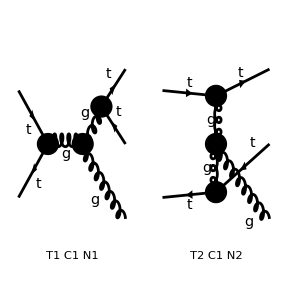

```mathematica
(* Diagrams ttbar -> ttbarg *)
Diagramttbarg=InsertFields[Topology2to3,{F[3,{3}],-F[3,{3}]}->{F[3,{3}],-F[3,{3}],V[5]},ExcludeParticles->{S[__],V[1|2|3|4],F[3]}];
Paint[Diagramttbarg,ColumnsXRows->2];
```

### Amplitudes

#### Generate amplitudes

```mathematica
AmplitudettbargRaw=MyCreateFCAmp[Diagramttbarg];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

in total: 2 Classes amplitudes

#### Manipulate

```mathematica
AmplitudettbargRaw[[2]]
DiracSimplify[%,DiracSubstitute67->True];
Simplify[FeynAmpDenominatorExplicit[%]]
```

(ⅈ g_s (ḡ)^Lor2Lor3 (ḡ)^Lor4Lor5 ((ε̄)^*)^Lor1(OutMom3) f^Glu5Glu6Glu7 ((ḡ)^Lor3Lor5 (2 OverBar[InMom2]-2 OverBar[OutMom2]-OverBar[OutMom3])^Lor1+(ḡ)^Lor1Lor5 (-OverBar[InMom2]+OverBar[OutMom2]-OverBar[OutMom3])^Lor3+(ḡ)^Lor1Lor3 (-OverBar[InMom2]+OverBar[OutMom2]+2 OverBar[OutMom3])^Lor5) (φ(OverBar[OutMom1],FCGV(MT))).(-ⅈ g_s (γ̄)^Lor2.(γ̄)^6 T_Col3Col1^Glu6-ⅈ g_s (γ̄)^Lor2.(γ̄)^7 T_Col3Col1^Glu6).(φ(OverBar[InMom1],FCGV(MT))) (φ(-OverBar[InMom2],FCGV(MT))).(-ⅈ g_s (γ̄)^Lor4.(γ̄)^6 T_Col2Col4^Glu7-ⅈ g_s (γ̄)^Lor4.(γ̄)^7 T_Col2Col4^Glu7).(φ(-OverBar[OutMom2],FCGV(MT))))/((OverBar[InMom2]-OverBar[OutMom2])^2 (-OverBar[InMom2]+OverBar[OutMom2]+OverBar[OutMom3])^2)

(ⅈ g_s^3 T_Col3Col1^Glu6 T_Col2Col4^Glu7 f^Glu5Glu6Glu7 ((-2 (OverBar[InMom2]·(ε̄)^*(OutMom3))+2 (OverBar[OutMom2]·(ε̄)^*(OutMom3))+OverBar[OutMom3]·(ε̄)^*(OutMom3)) (φ(OverBar[OutMom1],FCGV(MT))).(γ̄)^Lor4.(φ(OverBar[InMom1],FCGV(MT))) (φ(-OverBar[InMom2],FCGV(MT))).(γ̄)^Lor4.(φ(-OverBar[OutMom2],FCGV(MT)))+(φ(-OverBar[InMom2],FCGV(MT))).(γ̄·(ε̄)^*(OutMom3)).(φ(-OverBar[OutMom2],FCGV(MT))) ((φ(OverBar[OutMom1],FCGV(MT))).(γ̄·OverBar[InMom2]).(φ(OverBar[InMom1],FCGV(MT)))-(φ(OverBar[OutMom1],FCGV(MT))).(γ̄·OverBar[OutMom2]).(φ(OverBar[InMom1],FCGV(MT)))+(φ(OverBar[OutMom1],FCGV(MT))).(γ̄·OverBar[OutMom3]).(φ(OverBar[InMom1],FCGV(MT))))-2 (φ(-OverBar[InMom2],FCGV(MT))).(γ̄·OverBar[OutMom3]).(φ(-OverBar[OutMom2],FCGV(MT))) (φ(OverBar[OutMom1],FCGV(MT))).(γ̄·(ε̄)^*(OutMom3)).(φ(OverBar[InMom1],FCGV(MT)))))/((-2 (OverBar[InMom2]·OverBar[OutMom2])+OverBar[InMom2]^2+OverBar[OutMom2]^2) (-2 (OverBar[InMom2]·OverBar[OutMom2])-2 (OverBar[InMom2]·OverBar[OutMom3])+OverBar[InMom2]^2+2 (OverBar[OutMom2]·OverBar[OutMom3])+OverBar[OutMom2]^2+OverBar[OutMom3]^2))

```mathematica
SUNF[SUNIndex[Glu5], SUNIndex[Glu6], SUNIndex[Glu7]]*
  SUNTF[{SUNIndex[Glu6]}, SUNFIndex[Col3], SUNFIndex[Col1]]*SUNTF[{SUNIndex[Glu7]}, SUNFIndex[Col2], SUNFIndex[Col4]]
SUNSimplify[%*SUNTF[{SUNIndex[Glu1]},SUNFIndex[Col1],SUNFIndex[Col2]]/Sqrt[SUNN]*Sqrt[2]*SUNFDelta[SUNFIndex[Col3],SUNFIndex[Col4]],SUNNToCACF->False]
Simplify[I*%//.{SUNN->3}]
```

T_Col3Col1^Glu6 T_Col2Col4^Glu7 f^Glu5Glu6Glu7

-(ⅈ √N δ^Glu1Glu5)/(2 √2)

1/2 √(3/2) δ^Glu1Glu5

```mathematica
SUNTF[{SUNIndex[A]}, SUNFIndex[Col3], SUNFIndex[Col1]]*SUNFDelta[SUNFIndex[Col2],SUNFIndex[Col4]]
SUNSimplify[%*SUNTF[{SUNIndex[Glu1]},SUNFIndex[Col1],SUNFIndex[Col2]]/Sqrt[SUNN]*Sqrt[2]*SUNFDelta[SUNFIndex[Col3],SUNFIndex[Col4]],SUNNToCACF->False]
Simplify[%//.{SUNN->3}]
```

δ_Col2Col4 T_Col3Col1^A

δ^AGlu1/(√2 √N)

δ^AGlu1/(√6)

```mathematica
SUNTF[{SUNIndex[A]}, SUNFIndex[Col2], SUNFIndex[Col4]]*SUNFDelta[SUNFIndex[Col1],SUNFIndex[Col3]]
SUNSimplify[%*SUNTF[{SUNIndex[Glu1]},SUNFIndex[Col1],SUNFIndex[Col2]]/Sqrt[SUNN]*Sqrt[2]*SUNFDelta[SUNFIndex[Col3],SUNFIndex[Col4]],SUNNToCACF->False]
Simplify[%//.{SUNN->3}]
```

δ_Col1Col3 T_Col2Col4^A

δ^AGlu1/(√2 √N)

δ^AGlu1/(√6)

Excluding 0 Generic, 10 Classes, and 14 Particles fields

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

Restoring 0 Generic, 10 Classes, and 14 Particles fields

in total: 1 Classes insertion

> Top. 1 adbd\cd\0.m, 0 diagrams

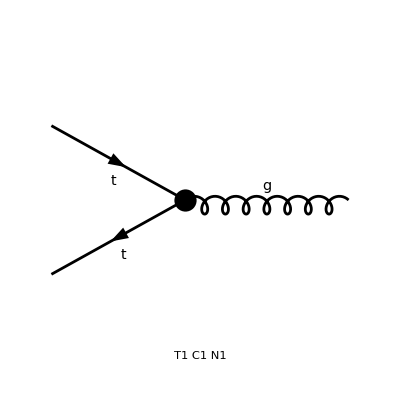

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

{-ⅈ ((ε̄)^*)^Lor1(OutMom1) (φ(-OverBar[InMom2],FCGV(MT))).(-ⅈ g_s (γ̄)^Lor1.(γ̄)^6 T_Col2Col1^Glu3-ⅈ g_s (γ̄)^Lor1.(γ̄)^7 T_Col2Col1^Glu3).(φ(OverBar[InMom1],FCGV(MT)))}

{g_s T_Col2Col1^Glu3 (-(φ(-OverBar[InMom2],FCGV(MT))).(γ̄·(ε̄)^*(OutMom1)).(φ(OverBar[InMom1],FCGV(MT))))}

```mathematica
(* Diagrams ttbar -> ttbarg *)
tmp=InsertFields[Topology2to1,{F[3,{3}],-F[3,{3}]}->{V[5]},ExcludeParticles->{S[__],V[1|2|3|4],F[3]}];
Paint[%,ColumnsXRows->2];
MyCreateFCAmp[tmp]
Simplify[DiracSimplify[%,DiracSubstitute67->True]]
```

Excluding 0 Generic, 10 Classes, and 14 Particles fields

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

Restoring 0 Generic, 10 Classes, and 14 Particles fields

in total: 1 Classes insertion

> Top. 1 adbd\cd\0.m, 0 diagrams

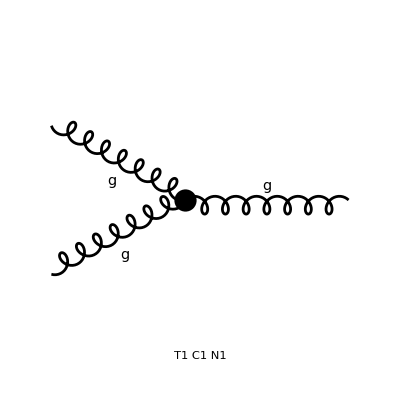

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

{-ⅈ g_s (ε̄)^Lor1(InMom1) (ε̄)^Lor2(InMom2) ((ε̄)^*)^Lor3(OutMom1) f^Glu1Glu2Glu3 ((ḡ)^Lor1Lor2 (OverBar[InMom2]-OverBar[InMom1])^Lor3+(ḡ)^Lor1Lor3 (OverBar[InMom1]+OverBar[OutMom1])^Lor2+(ḡ)^Lor2Lor3 (-OverBar[InMom2]-OverBar[OutMom1])^Lor1)}

{-ⅈ g_s (ε̄)^Lor1(InMom1) (ε̄)^Lor2(InMom2) ((ε̄)^*)^Lor3(OutMom1) f^Glu1Glu2Glu3 ((ḡ)^Lor1Lor2 (OverBar[InMom2]-OverBar[InMom1])^Lor3+(ḡ)^Lor1Lor3 (OverBar[InMom1]+OverBar[OutMom1])^Lor2+(ḡ)^Lor2Lor3 (-OverBar[InMom2]-OverBar[OutMom1])^Lor1)}

```mathematica
tmp=InsertFields[Topology2to1,{V[5],V[5]}->{V[5]},ExcludeParticles->{S[__],V[1|2|3|4],F[3]}];
Paint[%,ColumnsXRows->2];
MyCreateFCAmp[tmp]
Simplify[DiracSimplify[%,DiracSubstitute67->True]]
```

```mathematica
Paint[Diagramggttbar,ColumnsXRows->2];
```

> Top. 1 aebe\cfdf\ef.m, 0 diagrams

> Top. 2 aebf\cedf\ef.m, 0 diagrams

> Top. 3 aebf\cfde\ef.m, 0 diagrams

-Graphics-

```mathematica
AmplitudeggttbarRaw
```

{1/(OverBar[OutMom1]+OverBar[OutMom2])^2 g_s (ḡ)^Lor3Lor4 (ε̄)^Lor1(InMom1) (ε̄)^Lor2(InMom2) f^Glu1Glu2Glu5 ((ḡ)^Lor1Lor2 (OverBar[InMom2]-OverBar[InMom1])^Lor3+(ḡ)^Lor1Lor3 (OverBar[InMom1]+OverBar[OutMom1]+OverBar[OutMom2])^Lor2+(ḡ)^Lor2Lor3 (-OverBar[InMom2]-OverBar[OutMom1]-OverBar[OutMom2])^Lor1) (φ(OverBar[OutMom1],FCGV(MT))).(-ⅈ g_s (γ̄)^Lor4.(γ̄)^6 T_Col3Col4^Glu5-ⅈ g_s (γ̄)^Lor4.(γ̄)^7 T_Col3Col4^Glu5).(φ(-OverBar[OutMom2],FCGV(MT))),-((ε̄)^Lor1(InMom1) (ε̄)^Lor2(InMom2) (φ(OverBar[OutMom1],FCGV(MT))).(-ⅈ g_s (γ̄)^Lor1.(γ̄)^6 T_Col3Col5^Glu1-ⅈ g_s (γ̄)^Lor1.(γ̄)^7 T_Col3Col5^Glu1).(γ̄·(OverBar[InMom2]-OverBar[OutMom2])+FCGV(MT)).(-ⅈ g_s (γ̄)^Lor2.(γ̄)^6 T_Col5Col4^Glu2-ⅈ g_s (γ̄)^Lor2.(γ̄)^7 T_Col5Col4^Glu2).(φ(-OverBar[OutMom2],FCGV(MT))))/((OverBar[OutMom2]-OverBar[InMom2])^2-(FCGV(MT))^2),-((ε̄)^Lor1(InMom1) (ε̄)^Lor2(InMom2) (φ(OverBar[OutMom1],FCGV(MT))).(-ⅈ g_s (γ̄)^Lor2.(γ̄)^6 T_Col3Col5^Glu2-ⅈ g_s (γ̄)^Lor2.(γ̄)^7 T_Col3Col5^Glu2).(γ̄·(OverBar[OutMom1]-OverBar[InMom2])+FCGV(MT)).(-ⅈ g_s (γ̄)^Lor1.(γ̄)^6 T_Col5Col4^Glu1-ⅈ g_s (γ̄)^Lor1.(γ̄)^7 T_Col5Col4^Glu1).(φ(-OverBar[OutMom2],FCGV(MT))))/((OverBar[InMom2]-OverBar[OutMom1])^2-(FCGV(MT))^2)}

```mathematica
DiracSpinorV[En,{0,0,-En},0,bq]
%//.{Theta[bq]->0,Phi[bq]->0}
```

(√2 √En (ⅇ^(-1/2 ⅈ Phi(bq)) cos((Theta(bq))/2) Eta(bq,minus)-ⅇ^(-1/2 ⅈ Phi(bq)) sin((Theta(bq))/2) Eta(bq,plus))
0
0
-√2 √En (ⅇ^(1/2 ⅈ Phi(bq)) sin((Theta(bq))/2) Eta(bq,minus)+ⅇ^(1/2 ⅈ Phi(bq)) cos((Theta(bq))/2) Eta(bq,plus)))

(√2 √En Eta(bq,minus)
0
0
-√2 √En Eta(bq,plus))

```mathematica
DiracSpinorU[En,{p*Sin[theta],0,p*Cos[theta]},0,t]
Simplify[(%*Sqrt[2*En])//.{Theta[t]->0,Phi[t]->0}]
```

(((√En-(p cos(theta))/(√En)) (ⅇ^(-1/2 ⅈ Phi(t)) cos((Theta(t))/2) Xi(t,plus)-ⅇ^(-1/2 ⅈ Phi(t)) sin((Theta(t))/2) Xi(t,minus))-(p sin(theta) (ⅇ^(1/2 ⅈ Phi(t)) cos((Theta(t))/2) Xi(t,minus)+ⅇ^(1/2 ⅈ Phi(t)) sin((Theta(t))/2) Xi(t,plus)))/(√En))/(√2)
(((p cos(theta))/(√En)+√En) (ⅇ^(1/2 ⅈ Phi(t)) cos((Theta(t))/2) Xi(t,minus)+ⅇ^(1/2 ⅈ Phi(t)) sin((Theta(t))/2) Xi(t,plus))-(p sin(theta) (ⅇ^(-1/2 ⅈ Phi(t)) cos((Theta(t))/2) Xi(t,plus)-ⅇ^(-1/2 ⅈ Phi(t)) sin((Theta(t))/2) Xi(t,minus)))/(√En))/(√2)
(((p cos(theta))/(√En)+√En) (ⅇ^(-1/2 ⅈ Phi(t)) cos((Theta(t))/2) Xi(t,plus)-ⅇ^(-1/2 ⅈ Phi(t)) sin((Theta(t))/2) Xi(t,minus))+(p sin(theta) (ⅇ^(1/2 ⅈ Phi(t)) cos((Theta(t))/2) Xi(t,minus)+ⅇ^(1/2 ⅈ Phi(t)) sin((Theta(t))/2) Xi(t,plus)))/(√En))/(√2)
((p sin(theta) (ⅇ^(-1/2 ⅈ Phi(t)) cos((Theta(t))/2) Xi(t,plus)-ⅇ^(-1/2 ⅈ Phi(t)) sin((Theta(t))/2) Xi(t,minus)))/(√En)+(√En-(p cos(theta))/(√En)) (ⅇ^(1/2 ⅈ Phi(t)) cos((Theta(t))/2) Xi(t,minus)+ⅇ^(1/2 ⅈ Phi(t)) sin((Theta(t))/2) Xi(t,plus)))/(√2))

(Xi(t,plus) (En-p cos(theta))-p sin(theta) Xi(t,minus)
Xi(t,minus) (En+p cos(theta))-p sin(theta) Xi(t,plus)
Xi(t,plus) (En+p cos(theta))+p sin(theta) Xi(t,minus)
Xi(t,minus) (En-p cos(theta))+p sin(theta) Xi(t,plus))

```mathematica
DiracSpinorV[En,{-p*Sin[theta],0,-p*Cos[theta]},0,bt]
Simplify[(%*Sqrt[2*En])//.{Theta[bt]->0,Phi[bt]->0}]
```

(((p sin(theta) (ⅇ^(1/2 ⅈ Phi(bt)) sin((Theta(bt))/2) Eta(bt,minus)+ⅇ^(1/2 ⅈ Phi(bt)) cos((Theta(bt))/2) Eta(bt,plus)))/(√En)+((p cos(theta))/(√En)+√En) (ⅇ^(-1/2 ⅈ Phi(bt)) cos((Theta(bt))/2) Eta(bt,minus)-ⅇ^(-1/2 ⅈ Phi(bt)) sin((Theta(bt))/2) Eta(bt,plus)))/(√2)
((√En-(p cos(theta))/(√En)) (ⅇ^(1/2 ⅈ Phi(bt)) sin((Theta(bt))/2) Eta(bt,minus)+ⅇ^(1/2 ⅈ Phi(bt)) cos((Theta(bt))/2) Eta(bt,plus))+(p sin(theta) (ⅇ^(-1/2 ⅈ Phi(bt)) cos((Theta(bt))/2) Eta(bt,minus)-ⅇ^(-1/2 ⅈ Phi(bt)) sin((Theta(bt))/2) Eta(bt,plus)))/(√En))/(√2)
((p sin(theta) (ⅇ^(1/2 ⅈ Phi(bt)) sin((Theta(bt))/2) Eta(bt,minus)+ⅇ^(1/2 ⅈ Phi(bt)) cos((Theta(bt))/2) Eta(bt,plus)))/(√En)-(√En-(p cos(theta))/(√En)) (ⅇ^(-1/2 ⅈ Phi(bt)) cos((Theta(bt))/2) Eta(bt,minus)-ⅇ^(-1/2 ⅈ Phi(bt)) sin((Theta(bt))/2) Eta(bt,plus)))/(√2)
((p sin(theta) (ⅇ^(-1/2 ⅈ Phi(bt)) cos((Theta(bt))/2) Eta(bt,minus)-ⅇ^(-1/2 ⅈ Phi(bt)) sin((Theta(bt))/2) Eta(bt,plus)))/(√En)-((p cos(theta))/(√En)+√En) (ⅇ^(1/2 ⅈ Phi(bt)) sin((Theta(bt))/2) Eta(bt,minus)+ⅇ^(1/2 ⅈ Phi(bt)) cos((Theta(bt))/2) Eta(bt,plus)))/(√2))

(Eta(bt,minus) (En+p cos(theta))+p sin(theta) Eta(bt,plus)
Eta(bt,plus) (En-p cos(theta))+p sin(theta) Eta(bt,minus)
Eta(bt,minus) (p cos(theta)-En)+p sin(theta) Eta(bt,plus)
p sin(theta) Eta(bt,minus)-Eta(bt,plus) (En+p cos(theta)))

```mathematica
BarDiracSpinorU[En,{0,0,p},mt].GammaMatrix[3].DiracSpinorV[En,{0,0,-p},mt];
Simplify[%//.{Phi[__]->0,Theta[__]->0},Assumptions->Join[AssumptionPhysicalggttbar,{En>0}]]
```

(((En^2+2 En mt+mt^2-p^2) (Eta(1,plus) Xi(1,minus)-Eta(1,minus) Xi(1,plus)))/(En+mt))

```mathematica
BarDiracSpinorU[En,{p*Sin[theta],0,p*Cos[theta]},mt].GammaMatrix[1].DiracSpinorV[En,{-p*Sin[theta],0,-p*Cos[theta]},mt];
Simplify[%//.{Phi[__]->0,Theta[__]->theta},Assumptions->Join[AssumptionPhysicalggttbar,{En>0}]]
```

(-(Eta(1,plus) (cos(theta) Xi(1,plus) (En^2+2 En mt+mt^2+p^2)-sin(theta) Xi(1,minus) (En^2+2 En mt+mt^2-p^2))+Eta(1,minus) (cos(theta) Xi(1,minus) (En^2+2 En mt+mt^2+p^2)+sin(theta) Xi(1,plus) (En^2+2 En mt+mt^2-p^2)))/(En+mt))

```mathematica
BarDiracSpinorU[En,{p*Sin[theta],0,p*Cos[theta]},mt].GammaMatrix[3].DiracSpinorV[En,{-p*Sin[theta],0,-p*Cos[theta]},mt];
Simplify[%//.{Phi[__]->0,Theta[__]->theta},Assumptions->Join[AssumptionPhysicalggttbar,{En>0}]]
```

((Eta(1,minus) (sin(theta) Xi(1,minus) (En^2+2 En mt+mt^2+p^2)-cos(theta) Xi(1,plus) (En^2+2 En mt+mt^2-p^2))+Eta(1,plus) (cos(theta) Xi(1,minus) (En^2+2 En mt+mt^2-p^2)+sin(theta) Xi(1,plus) (En^2+2 En mt+mt^2+p^2)))/(En+mt))

```mathematica
BarDiracSpinorU[En,{p*Sin[theta]Cos[pi],0,p*Cos[theta]},mt].GammaMatrix[2].DiracSpinorV[En,{-p*Sin[theta],0,-p*Cos[theta]},mt];
Simplify[%//.{Phi[__]->0,Theta[__]->theta},Assumptions->Join[AssumptionPhysicalggttbar,{En>0}]]
```

(-(ⅈ (En^2+2 En mt+mt^2+p^2) (Eta(1,minus) Xi(1,minus)-Eta(1,plus) Xi(1,plus)))/(En+mt))

```mathematica
BarDiracSpinorU[En,{p*Sin[theta],0,p*Cos[theta]},mt].GammaMatrix[1].DiracSpinorV[En,{-p*Sin[theta],0,-p*Cos[theta]},mt];
Simplify[%//.{Phi[__]->0,Theta[__]->theta},Assumptions->Join[AssumptionPhysicalggttbar,{En>0}]]
```

(-(Eta(1,plus) (cos(theta) Xi(1,plus) (En^2+2 En mt+mt^2+p^2)-sin(theta) Xi(1,minus) (En^2+2 En mt+mt^2-p^2))+Eta(1,minus) (cos(theta) Xi(1,minus) (En^2+2 En mt+mt^2+p^2)+sin(theta) Xi(1,plus) (En^2+2 En mt+mt^2-p^2)))/(En+mt))

```mathematica
BarDiracSpinorU[En,{En*Sin[theta],0,En*Cos[theta]},0].GammaMatrix[2].DiracSpinorV[En,{-En*Sin[theta],0,-En*Cos[theta]},0];
Simplify[%//.{Phi[__]->0,Theta[__]->theta},Assumptions->Join[AssumptionPhysicalggttbar,{En>0}]]
```

(-2 ⅈ En (Eta(1,minus) Xi(1,minus)-Eta(1,plus) Xi(1,plus)))

```mathematica
BarDiracSpinorV[En,{En*Sin[theta],0,-En*Cos[theta]},0].GammaMatrix[3].DiracSpinorU[En,{-En*Sin[theta],0,En*Cos[theta]},0];
Simplify[%//.{Phi[__]->0,Theta[__]->-theta},Assumptions->Join[AssumptionPhysicalggttbar,{En>0}]]
```

(-2 En sin(theta) (Eta(1,minus) Xi(1,minus)+Eta(1,plus) Xi(1,plus)))

```mathematica
DiracSpinorV[En,{-p*Sin[theta]Cos[phi],-p*Sin[theta]Sin[phi],-p*Cos[theta]},0]//.{Phi[__]->0,Theta[__]->0}
Simplify[%*Sqrt[2*En]]
```

((Eta(1,minus) ((p cos(theta))/(√En)+√En)-(Eta(1,plus) (-p cos(phi) sin(theta)+ⅈ p sin(phi) sin(theta)))/(√En))/(√2)
(Eta(1,plus) (√En-(p cos(theta))/(√En))-(Eta(1,minus) (-p cos(phi) sin(theta)-ⅈ p sin(phi) sin(theta)))/(√En))/(√2)
(-(Eta(1,minus) (√En-(p cos(theta))/(√En)))-(Eta(1,plus) (-p cos(phi) sin(theta)+ⅈ p sin(phi) sin(theta)))/(√En))/(√2)
(-(Eta(1,plus) ((p cos(theta))/(√En)+√En))-(Eta(1,minus) (-p cos(phi) sin(theta)-ⅈ p sin(phi) sin(theta)))/(√En))/(√2))

(Eta(1,minus) (En+p cos(theta))+p sin(theta) Eta(1,plus) (cos(phi)-ⅈ sin(phi))
Eta(1,plus) (En-p cos(theta))+p sin(theta) Eta(1,minus) (cos(phi)+ⅈ sin(phi))
Eta(1,minus) (p cos(theta)-En)+p sin(theta) Eta(1,plus) (cos(phi)-ⅈ sin(phi))
-Eta(1,plus) (En+p cos(theta))+p sin(theta) Eta(1,minus) (cos(phi)+ⅈ sin(phi)))

```mathematica
BarDiracSpinorU[En,{0,0,En},0]//.{Phi[__]->0,Theta[__]->0}
```

(√2 Conjugate[(√En Xi(1,plus))] | 0 | 0 | √2 Conjugate[(√En Xi(1,minus))])

```mathematica
BarDiracSpinorU[En,{p*Sin[theta]*Cos[phi],p*Sin[theta]*Sin[phi],p*Cos[theta]},mt].GammaMatrix[1].DiracSpinorV[En,{-p*Sin[theta]*Cos[phi],-p*Sin[theta]*Sin[phi],-p*Cos[theta]},mt]//.{Phi[__]->0,Theta[__]->theta};
Simplify[%[[1,1]],Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]];
FullSimplify[%,Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]]
Collect[%,{Eta[__],Xi[__]},FullSimplify]//.repSimplify
FullSimplify[%//.{p->0}]
```

-1/(2 (En+mt))((2 (En+mt)^2+p^2 cos(2 theta)+p^2) (Eta(1,plus) (cos(theta) Xi(1,plus)-sin(theta) Xi(1,minus))+Eta(1,minus) (cos(theta) Xi(1,minus)+sin(theta) Xi(1,plus)))-2 ⅈ p^2 sin(2 phi) sin^2(theta) (Eta(1,minus) Xi(1,minus)-Eta(1,plus) Xi(1,plus))-2 p^2 cos(2 phi) sin^2(theta) (Eta(1,plus) (cos(theta) Xi(1,plus)-sin(theta) Xi(1,minus))+Eta(1,minus) (cos(theta) Xi(1,minus)+sin(theta) Xi(1,plus)))+2 p^2 cos(phi) sin(2 theta) (Eta(1,minus) (sin(theta) Xi(1,minus)-cos(theta) Xi(1,plus))+Eta(1,plus) (cos(theta) Xi(1,minus)+sin(theta) Xi(1,plus))))

η_-(1) (-(ξ_+(1) sin(θ) (2 (En+m_t)^2+p^2 (-4 cos^2(θ) cos(ϕ)-2 sin^2(θ) cos(2 ϕ)+cos(2 θ))+p^2))/(2 (En+m_t))+(ξ_-(1) (-cos(θ) (2 (En+m_t)^2+p^2 cos(2 θ)+p^2)+2 p^2 sin^2(θ) (cos(θ) (cos(2 ϕ)-2 cos(ϕ))+ⅈ sin(2 ϕ))))/(2 (En+m_t)))+η_+(1) ((ξ_-(1) sin(θ) (2 (En+m_t)^2+p^2 (-4 cos^2(θ) cos(ϕ)-2 sin^2(θ) cos(2 ϕ)+cos(2 θ))+p^2))/(2 (En+m_t))+(ξ_+(1) (-cos(θ) (2 (En+m_t)^2+p^2 cos(2 θ)+p^2)+2 p^2 sin^2(θ) (cos(θ) (cos(2 ϕ)-2 cos(ϕ))-ⅈ sin(2 ϕ))))/(2 (En+m_t)))

-((En+m_t) (ξ_-(1) (η_-(1) cos(θ)-η_+(1) sin(θ))+ξ_+(1) (η_-(1) sin(θ)+η_+(1) cos(θ))))

```mathematica
BarDiracSpinorU[En,{p*Sin[theta]*Cos[phi],p*Sin[theta]*Sin[phi],p*Cos[theta]},mt].GammaMatrix[2].DiracSpinorV[En,{-p*Sin[theta]*Cos[phi],-p*Sin[theta]*Sin[phi],-p*Cos[theta]},mt]//.{Phi[__]->0,Theta[__]->theta};
Simplify[%[[1,1]],Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]];
FullSimplify[%,Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]]
Collect[%,{Eta[__],Xi[__]},FullSimplify]//.repSimplify
FullSimplify[%//.{p->0}]
```

1/(En+mt)(Eta(1,plus) (-p^2 Xi(1,minus) (sin(2 phi) sin^3(theta)+sin(phi) sin(2 theta) cos(theta))+ⅈ Xi(1,plus) ((En+mt)^2+p^2 (cos^2(theta)+sin^2(theta) (cos(2 phi)-2 ⅈ sin(phi) (cos(phi)-1) cos(theta)))))+Eta(1,minus) (p^2 Xi(1,plus) (sin(2 phi) sin^3(theta)+sin(phi) sin(2 theta) cos(theta))-ⅈ Xi(1,minus) ((En+mt)^2+p^2 (cos^2(theta)+sin^2(theta) (cos(2 phi)+2 ⅈ sin(phi) (cos(phi)-1) cos(theta))))))

η_-(1) ((ξ_+(1) p^2 (sin^3(θ) sin(2 ϕ)+sin(2 θ) cos(θ) sin(ϕ)))/(En+m_t)-(ⅈ ξ_-(1) ((En+m_t)^2+p^2 (cos^2(θ)+sin^2(θ) (cos(2 ϕ)+2 ⅈ cos(θ) sin(ϕ) (cos(ϕ)-1)))))/(En+m_t))+η_+(1) (-(ξ_-(1) p^2 (sin^3(θ) sin(2 ϕ)+sin(2 θ) cos(θ) sin(ϕ)))/(En+m_t)+(ⅈ ξ_+(1) ((En+m_t)^2+p^2 (cos^2(θ)+sin^2(θ) (cos(2 ϕ)-2 ⅈ cos(θ) sin(ϕ) (cos(ϕ)-1)))))/(En+m_t))

-ⅈ (η_-(1) ξ_-(1)-η_+(1) ξ_+(1)) (En+m_t)

```mathematica
BarDiracSpinorU[En,{p*Sin[theta]*Cos[phi],p*Sin[theta]*Sin[phi],p*Cos[theta]},mt].GammaMatrix[3].DiracSpinorV[En,{-p*Sin[theta]*Cos[phi],-p*Sin[theta]*Sin[phi],-p*Cos[theta]},mt]//.{Phi[__]->0,Theta[__]->theta};
Simplify[%[[1,1]],Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]];
FullSimplify[%,Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]]
Collect[%,{Eta[__],Xi[__]},FullSimplify]//.repSimplify
FullSimplify[%//.{p->0}]
```

1/(2 (En+mt))(2 ((En+mt)^2-p^2 cos(2 theta)) (Eta(1,minus) (sin(theta) Xi(1,minus)-cos(theta) Xi(1,plus))+Eta(1,plus) (cos(theta) Xi(1,minus)+sin(theta) Xi(1,plus)))+2 ⅈ p^2 sin(phi) sin(2 theta) (Eta(1,minus) Xi(1,minus)-Eta(1,plus) Xi(1,plus))+2 p^2 cos(phi) sin(2 theta) (Eta(1,plus) (cos(theta) Xi(1,plus)-sin(theta) Xi(1,minus))+Eta(1,minus) (cos(theta) Xi(1,minus)+sin(theta) Xi(1,plus))))

η_+(1) ((ξ_-(1) cos(θ) ((En+m_t)^2-p^2 (2 sin^2(θ) cos(ϕ)+cos(2 θ))))/(En+m_t)+(ξ_+(1) (sin(θ) ((En+m_t)^2-p^2 cos(2 θ))+p^2 sin(2 θ) (cos(θ) cos(ϕ)-ⅈ sin(ϕ))))/(En+m_t))+η_-(1) ((ξ_+(1) (cos(θ) (p^2 cos(2 θ)-(En+m_t)^2)+p^2 sin(θ) sin(2 θ) cos(ϕ)))/(En+m_t)+(ξ_-(1) (sin(θ) ((En+m_t)^2-p^2 cos(2 θ))+p^2 sin(2 θ) (cos(θ) cos(ϕ)+ⅈ sin(ϕ))))/(En+m_t))

(En+m_t) ((η_-(1) ξ_-(1)+η_+(1) ξ_+(1)) sin(θ)+(η_+(1) ξ_-(1)-η_-(1) ξ_+(1)) cos(θ))

```mathematica
(BarDiracSpinorU[En,{p*Sin[theta]*Cos[phi],p*Sin[theta]*Sin[phi],p*Cos[theta]},mt].GammaMatrix[5].DiracSpinorV[En,{-p*Sin[theta]*Cos[phi],-p*Sin[theta]*Sin[phi],-p*Cos[theta]},mt])//.{Phi[__]->0,Theta[__]->theta};
Simplify[%[[1,1]],Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]];
FullSimplify[%,Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]]
Collect[%,{Eta[__],Xi[__]},FullSimplify[TrigReduce[FullSimplify[#]]]&]//.repSimplify
FullSimplify[%//.{p->0}]
```

-(((En+mt)^2+p^2) (Eta(1,plus) Xi(1,minus)+Eta(1,minus) Xi(1,plus)))/(En+mt)

-(η_+(1) ξ_-(1) ((En+m_t)^2+p^2))/(En+m_t)-(η_-(1) ξ_+(1) ((En+m_t)^2+p^2))/(En+m_t)

-((η_+(1) ξ_-(1)+η_-(1) ξ_+(1)) (En+m_t))

```mathematica
(BarDiracSpinorU[En,{p*Sin[theta]*Cos[phi],p*Sin[theta]*Sin[phi],p*Cos[theta]},mt].GammaMatrix[5].GammaMatrix[0].DiracSpinorV[En,{-p*Sin[theta]*Cos[phi],-p*Sin[theta]*Sin[phi],-p*Cos[theta]},mt])//.{Phi[__]->0,Theta[__]->theta};
Simplify[%[[1,1]],Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]];
FullSimplify[%,Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]]
Collect[%,{Eta[__],Xi[__]},FullSimplify[TrigReduce[FullSimplify[#]]]&]//.repSimplify
FullSimplify[%//.{p->0}]
```

((En+mt-p) (En+mt+p) (Eta(1,plus) Xi(1,minus)+Eta(1,minus) Xi(1,plus)))/(En+mt)

η_+(1) ξ_-(1) (-p^2/(En+m_t)+En+m_t)+η_-(1) ξ_+(1) (-p^2/(En+m_t)+En+m_t)

(η_+(1) ξ_-(1)+η_-(1) ξ_+(1)) (En+m_t)

```mathematica
(BarDiracSpinorU[En,{p*Sin[theta]*Cos[phi],p*Sin[theta]*Sin[phi],p*Cos[theta]},mt].GammaMatrix[5].GammaMatrix[1].DiracSpinorV[En,{-p*Sin[theta]*Cos[phi],-p*Sin[theta]*Sin[phi],-p*Cos[theta]},mt])//.{Phi[__]->0,Theta[__]->theta};
Simplify[%[[1,1]],Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]];
FullSimplify[%,Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]]
Collect[%,{Eta[__],Xi[__]},FullSimplify[TrigReduce[FullSimplify[#]]]&]//.repSimplify
FullSimplify[%//.{p->0}]
```

2 p cos(theta) (Eta(1,plus) Xi(1,plus)-Eta(1,minus) Xi(1,minus))+2 ⅈ p sin(phi) sin(theta) (Eta(1,minus) (sin(theta) Xi(1,minus)-cos(theta) Xi(1,plus))+Eta(1,plus) (cos(theta) Xi(1,minus)+sin(theta) Xi(1,plus)))

η_-(1) (-2 ξ_-(1) p (cos(θ)-ⅈ sin^2(θ) sin(ϕ))-2 ⅈ ξ_+(1) p sin(θ) cos(θ) sin(ϕ))+η_+(1) (2 ξ_+(1) p (cos(θ)+ⅈ sin^2(θ) sin(ϕ))+2 ⅈ ξ_-(1) p sin(θ) cos(θ) sin(ϕ))

0

```mathematica
(BarDiracSpinorU[En,{p*Sin[theta]*Cos[phi],p*Sin[theta]*Sin[phi],p*Cos[theta]},mt].GammaMatrix[5].GammaMatrix[3].DiracSpinorV[En,{-p*Sin[theta]*Cos[phi],-p*Sin[theta]*Sin[phi],-p*Cos[theta]},mt])//.{Phi[__]->0,Theta[__]->theta};
Simplify[%[[1,1]],Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]];
FullSimplify[%,Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]]
Collect[%,{Eta[__],Xi[__]},FullSimplify[TrigReduce[FullSimplify[#]]]&]//.repSimplify
```

```mathematica
(BarDiracSpinorU[En,{p*Sin[theta]*Cos[phi],p*Sin[theta]*Sin[phi],p*Cos[theta]},mt].GammaMatrix[5].GammaMatrix[3].DiracSpinorV[En,{-p*Sin[theta]*Cos[phi],-p*Sin[theta]*Sin[phi],-p*Cos[theta]},mt])//.{Phi[__]->0,Theta[__]->theta};
Simplify[%[[1,1]],Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]];
FullSimplify[%,Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]]
Collect[%,{Eta[__],Xi[__]},FullSimplify[TrigReduce[FullSimplify[#]]]&]//.repSimplify
FullSimplify[%//.{p->0}]
```

2 p sin(theta) (cos(phi) (Eta(1,minus) Xi(1,minus)-Eta(1,plus) Xi(1,plus))+ⅈ sin(phi) (Eta(1,plus) (cos(theta) Xi(1,plus)-sin(theta) Xi(1,minus))+Eta(1,minus) (cos(theta) Xi(1,minus)+sin(theta) Xi(1,plus))))

η_-(1) (2 ⅈ ξ_+(1) p sin^2(θ) sin(ϕ)+2 ξ_-(1) p sin(θ) (cos(ϕ)+ⅈ cos(θ) sin(ϕ)))+η_+(1) (-2 ⅈ ξ_-(1) p sin^2(θ) sin(ϕ)-2 ξ_+(1) p sin(θ) (cos(ϕ)-ⅈ cos(θ) sin(ϕ)))

0

```mathematica
(BarDiracSpinorU[En,{p*Sin[theta]*Cos[phi],p*Sin[theta]*Sin[phi],p*Cos[theta]},mt].DiracSpinorV[En,{-p*Sin[theta]*Cos[phi],-p*Sin[theta]*Sin[phi],-p*Cos[theta]},mt])//.{Phi[__]->0,Theta[__]->theta};
Simplify[%[[1,1]],Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]];
FullSimplify[%,Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]]
Collect[%,{Eta[__],Xi[__]},FullSimplify[TrigReduce[FullSimplify[#]]]&]//.repSimplify
FullSimplify[%//.{θ->0}]
```

2 p (-sin^2(phi/2) sin(2 theta) (Eta(1,minus) Xi(1,minus)+Eta(1,plus) Xi(1,plus))+ⅈ sin(phi) sin(theta) (Eta(1,minus) Xi(1,minus)-Eta(1,plus) Xi(1,plus))+sin^2(phi/2) cos(2 theta) (Eta(1,minus) Xi(1,plus)-Eta(1,plus) Xi(1,minus))+cos^2(phi/2) (Eta(1,minus) Xi(1,plus)-Eta(1,plus) Xi(1,minus)))

η_-(1) (2 ξ_+(1) p (cos(2 θ) sin^2(ϕ/2)+cos^2(ϕ/2))+2 ξ_-(1) p sin(θ) (cos(θ) (cos(ϕ)-1)+ⅈ sin(ϕ)))+η_+(1) (-2 ξ_-(1) p (cos(2 θ) sin^2(ϕ/2)+cos^2(ϕ/2))+2 ξ_+(1) p sin(θ) (cos(θ) (cos(ϕ)-1)-ⅈ sin(ϕ)))

0

```mathematica
BarDiracSpinorU[En1,{p1*Sin[theta1]*Cos[phi1],p1*Sin[theta1]*Sin[phi1],p1*Cos[theta1]},mt]//.{Phi[__]->0,Theta[__]->theta1};
DiracSpinorU[En2,{p2*Sin[theta2]*Cos[phi2],p2*Sin[theta2]*Sin[phi2],p2*Cos[theta2]},mt]//.{Phi[__]->0,Theta[__]->theta2};
%%.%
```

(1/2 ((√(En2+mt)-(p2 cos(theta2))/(√(En2+mt))) (cos(theta2/2) Xi(1,minus)+sin(theta2/2) Xi(1,plus))+((p2 cos(phi2) sin(theta2)+ⅈ p2 sin(phi2) sin(theta2)) (cos(theta2/2) Xi(1,plus)-sin(theta2/2) Xi(1,minus)))/(√(En2+mt))) Conjugate[(((p1 cos(theta1))/(√(En1+mt))+√(En1+mt)) (cos(theta1/2) Xi(1,minus)+sin(theta1/2) Xi(1,plus))-((p1 cos(phi1) sin(theta1)+ⅈ p1 sin(phi1) sin(theta1)) (cos(theta1/2) Xi(1,plus)-sin(theta1/2) Xi(1,minus)))/(√(En1+mt)))]+1/2 (((p2 cos(theta2))/(√(En2+mt))+√(En2+mt)) (cos(theta2/2) Xi(1,minus)+sin(theta2/2) Xi(1,plus))-((p2 cos(phi2) sin(theta2)+ⅈ p2 sin(phi2) sin(theta2)) (cos(theta2/2) Xi(1,plus)-sin(theta2/2) Xi(1,minus)))/(√(En2+mt))) Conjugate[(((p1 cos(phi1) sin(theta1)+ⅈ p1 sin(phi1) sin(theta1)) (cos(theta1/2) Xi(1,plus)-sin(theta1/2) Xi(1,minus)))/(√(En1+mt))+(√(En1+mt)-(p1 cos(theta1))/(√(En1+mt))) (cos(theta1/2) Xi(1,minus)+sin(theta1/2) Xi(1,plus)))]+1/2 ((√(En2+mt)-(p2 cos(theta2))/(√(En2+mt))) (cos(theta2/2) Xi(1,plus)-sin(theta2/2) Xi(1,minus))-((p2 cos(phi2) sin(theta2)-ⅈ p2 sin(phi2) sin(theta2)) (cos(theta2/2) Xi(1,minus)+sin(theta2/2) Xi(1,plus)))/(√(En2+mt))) Conjugate[(((p1 cos(theta1))/(√(En1+mt))+√(En1+mt)) (cos(theta1/2) Xi(1,plus)-sin(theta1/2) Xi(1,minus))+((p1 cos(phi1) sin(theta1)-ⅈ p1 sin(phi1) sin(theta1)) (cos(theta1/2) Xi(1,minus)+sin(theta1/2) Xi(1,plus)))/(√(En1+mt)))]+1/2 (((p2 cos(theta2))/(√(En2+mt))+√(En2+mt)) (cos(theta2/2) Xi(1,plus)-sin(theta2/2) Xi(1,minus))+((p2 cos(phi2) sin(theta2)-ⅈ p2 sin(phi2) sin(theta2)) (cos(theta2/2) Xi(1,minus)+sin(theta2/2) Xi(1,plus)))/(√(En2+mt))) Conjugate[((√(En1+mt)-(p1 cos(theta1))/(√(En1+mt))) (cos(theta1/2) Xi(1,plus)-sin(theta1/2) Xi(1,minus))-((p1 cos(phi1) sin(theta1)-ⅈ p1 sin(phi1) sin(theta1)) (cos(theta1/2) Xi(1,minus)+sin(theta1/2) Xi(1,plus)))/(√(En1+mt)))])

```mathematica
BarDiracSpinorU[En1,{p1*Sin[theta1]*Cos[phi1],p1*Sin[theta1]*Sin[phi1],p1*Cos[theta1]},mt]//.{Phi[__]->0,Theta[__]->theta1};
DiracSpinorU[En2,{p2*Sin[theta2]*Cos[phi2],p2*Sin[theta2]*Sin[phi2],p2*Cos[theta2]},mt]//.{Phi[__]->0,Theta[__]->theta2};
%%.%
Simplify[%[[1,1]],Assumptions->Join[AssumptionPhysicalggttbar,{phi2>0,phi2<2*Pi,phi1>0,phi1<2*Pi,En1>0,p1>0,En2>0,p2>0,mt>0,theta1>0,theta1<Pi,theta2>0,theta2<Pi}]];
FullSimplify[%,Assumptions->Join[AssumptionPhysicalggttbar,{phi2>0,phi2<2*Pi,phi1>0,phi1<2*Pi,En1>0,p1>0,En2>0,p2>0,mt>0,theta1>0,theta1<Pi,theta2>0,theta2<Pi}]]
Collect[%,{Eta[__],Xi[__]},FullSimplify[TrigReduce[FullSimplify[#]]]&]//.repSimplify
FullSimplify[%//.{p->0}]
```

(1/2 ((√(En2+mt)-(p2 cos(theta2))/(√(En2+mt))) (cos(theta2/2) Xi(1,minus)+sin(theta2/2) Xi(1,plus))+((p2 cos(phi2) sin(theta2)+ⅈ p2 sin(phi2) sin(theta2)) (cos(theta2/2) Xi(1,plus)-sin(theta2/2) Xi(1,minus)))/(√(En2+mt))) Conjugate[(((p1 cos(theta1))/(√(En1+mt))+√(En1+mt)) (cos(theta1/2) Xi(1,minus)+sin(theta1/2) Xi(1,plus))-((p1 cos(phi1) sin(theta1)+ⅈ p1 sin(phi1) sin(theta1)) (cos(theta1/2) Xi(1,plus)-sin(theta1/2) Xi(1,minus)))/(√(En1+mt)))]+1/2 (((p2 cos(theta2))/(√(En2+mt))+√(En2+mt)) (cos(theta2/2) Xi(1,minus)+sin(theta2/2) Xi(1,plus))-((p2 cos(phi2) sin(theta2)+ⅈ p2 sin(phi2) sin(theta2)) (cos(theta2/2) Xi(1,plus)-sin(theta2/2) Xi(1,minus)))/(√(En2+mt))) Conjugate[(((p1 cos(phi1) sin(theta1)+ⅈ p1 sin(phi1) sin(theta1)) (cos(theta1/2) Xi(1,plus)-sin(theta1/2) Xi(1,minus)))/(√(En1+mt))+(√(En1+mt)-(p1 cos(theta1))/(√(En1+mt))) (cos(theta1/2) Xi(1,minus)+sin(theta1/2) Xi(1,plus)))]+1/2 ((√(En2+mt)-(p2 cos(theta2))/(√(En2+mt))) (cos(theta2/2) Xi(1,plus)-sin(theta2/2) Xi(1,minus))-((p2 cos(phi2) sin(theta2)-ⅈ p2 sin(phi2) sin(theta2)) (cos(theta2/2) Xi(1,minus)+sin(theta2/2) Xi(1,plus)))/(√(En2+mt))) Conjugate[(((p1 cos(theta1))/(√(En1+mt))+√(En1+mt)) (cos(theta1/2) Xi(1,plus)-sin(theta1/2) Xi(1,minus))+((p1 cos(phi1) sin(theta1)-ⅈ p1 sin(phi1) sin(theta1)) (cos(theta1/2) Xi(1,minus)+sin(theta1/2) Xi(1,plus)))/(√(En1+mt)))]+1/2 (((p2 cos(theta2))/(√(En2+mt))+√(En2+mt)) (cos(theta2/2) Xi(1,plus)-sin(theta2/2) Xi(1,minus))+((p2 cos(phi2) sin(theta2)-ⅈ p2 sin(phi2) sin(theta2)) (cos(theta2/2) Xi(1,minus)+sin(theta2/2) Xi(1,plus)))/(√(En2+mt))) Conjugate[((√(En1+mt)-(p1 cos(theta1))/(√(En1+mt))) (cos(theta1/2) Xi(1,plus)-sin(theta1/2) Xi(1,minus))-((p1 cos(phi1) sin(theta1)-ⅈ p1 sin(phi1) sin(theta1)) (cos(theta1/2) Xi(1,minus)+sin(theta1/2) Xi(1,plus)))/(√(En1+mt)))])

$Aborted

ReplaceRepeated::reps: {repSimplify} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted//.repSimplify

$Aborted//.repSimplify

```mathematica
(BarDiracSpinorU[En,{p*Sin[theta]*Cos[phi],p*Sin[theta]*Sin[phi],p*Cos[theta]},mt].GammaMatrix[5].GammaMatrix[3].DiracSpinorV[En,{-p*Sin[theta]*Cos[phi],-p*Sin[theta]*Sin[phi],-p*Cos[theta]},mt])//.{Phi[__]->0,Theta[__]->theta};
Simplify[%[[1,1]],Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]];
FullSimplify[%,Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]]
Collect[%,{Eta[__],Xi[__]},FullSimplify[TrigReduce[FullSimplify[#]]]&]//.repSimplify
FullSimplify[%//.{p->0}]
```

```mathematica
Sum[Metric[mu,mu]*(BarDiracSpinorV[En,{-En*Sin[theta1],0,En*Cos[theta1]},0].GammaMatrix[mu].DiracSpinorU[En,{En*Sin[theta1],0,-En*Cos[theta1]},0]//.{Phi[__]->0,Theta[__]->-theta1})*(BarDiracSpinorU[En,{p*Sin[theta2],0,p*Cos[theta2]},0].GammaMatrix[mu].DiracSpinorV[En,{-p*Sin[theta2],0,-p*Cos[theta2]},0]//.{Phi[__]->0,Theta[__]->theta2}),{mu,0,3}];
Simplify[%,Assumptions->Join[AssumptionPhysicalggttbar,{theta1>0,theta2>0,En>0,p>0}]]
Simplify[%//.{theta2->0},Assumptions->Join[AssumptionPhysicalggttbar,{theta1>0,theta2>0,En>0,p>0}]]
```

(-2 (-Eta(1,minus) Eta(1,plus) (4 (En^2+p^2) Xi(1,minus) Xi(1,plus) sin^2((theta1+theta2)/2)+(En^2-p^2) (Xi(1,minus))^2 sin(theta1+theta2)+(p^2-En^2) (Xi(1,plus))^2 sin(theta1+theta2))+(Eta(1,minus))^2 Xi(1,minus) (2 (En^2+p^2) Xi(1,minus) cos^2((theta1+theta2)/2)+(En^2-p^2) Xi(1,plus) sin(theta1+theta2))+(Eta(1,plus))^2 Xi(1,plus) (2 (En^2+p^2) Xi(1,plus) cos^2((theta1+theta2)/2)-(En^2-p^2) Xi(1,minus) sin(theta1+theta2))))

(-2 (-Eta(1,minus) Eta(1,plus) (4 (En^2+p^2) sin^2(theta1/2) Xi(1,minus) Xi(1,plus)+(En^2-p^2) sin(theta1) (Xi(1,minus))^2+(p^2-En^2) sin(theta1) (Xi(1,plus))^2)+(Eta(1,minus))^2 Xi(1,minus) (2 (En^2+p^2) cos^2(theta1/2) Xi(1,minus)+(En^2-p^2) sin(theta1) Xi(1,plus))+(Eta(1,plus))^2 Xi(1,plus) (2 (En^2+p^2) cos^2(theta1/2) Xi(1,plus)-(En^2-p^2) sin(theta1) Xi(1,minus))))

```mathematica
BarDiracSpinorU[En,{0,0,En},0].GammaMatrix[1].DiracSpinorV[En,{0,0,-En},0];
Simplify[%//.{Phi[__]->0,Theta[__]->0},Assumptions->Join[AssumptionPhysicalggttbar,{En>0}]]
```

(-2 En (Eta(1,minus) Xi(1,minus)+Eta(1,plus) Xi(1,plus)))

```mathematica
2*En*{{EtaDown,0,0,-EtaUp}}.GammaMatrix[0].GammaMatrix[2].Transpose[{{0,XiDown,XiUp,0}}]
```

(2 En (ⅈ EtaDown XiDown-ⅈ EtaUp XiUp))

```mathematica
GammaMatrix[5].GammaMatrix[0]
```

(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

```mathematica
GammaMatrix[0].GammaMatrix[0]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(A+B)^2+(A-B)^2
Simplify[%]
```

(A-B)^2+(A+B)^2

2 (A^2+B^2)

```mathematica
BarDiracSpinorU[En1,{p1*Sin[theta1]*Cos[phi1],p1*Sin[theta1]*Sin[phi1],p1*Cos[theta1]},mt].GammaMatrix[0].DiracSpinorU[En2,{p2*Sin[theta2]*Cos[phi2],p2*Sin[theta2]*Sin[phi2],p2*Cos[theta2]},mt]
```

(1/2 Conjugate[(((p1 cos(phi1) sin(theta1)+ⅈ p1 sin(phi1) sin(theta1)) (ⅇ^(-1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,plus)-ⅇ^(-1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,minus)))/(√(En1+mt))+(√(En1+mt)-(p1 cos(theta1))/(√(En1+mt))) (ⅇ^(1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,minus)+ⅇ^(1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,plus)))] (((p2 cos(phi2) sin(theta2)+ⅈ p2 sin(phi2) sin(theta2)) (ⅇ^(-1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,plus)-ⅇ^(-1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,minus)))/(√(En2+mt))+(√(En2+mt)-(p2 cos(theta2))/(√(En2+mt))) (ⅇ^(1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,minus)+ⅇ^(1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,plus)))+1/2 Conjugate[(((p1 cos(theta1))/(√(En1+mt))+√(En1+mt)) (ⅇ^(1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,minus)+ⅇ^(1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,plus))-((p1 cos(phi1) sin(theta1)+ⅈ p1 sin(phi1) sin(theta1)) (ⅇ^(-1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,plus)-ⅇ^(-1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,minus)))/(√(En1+mt)))] (((p2 cos(theta2))/(√(En2+mt))+√(En2+mt)) (ⅇ^(1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,minus)+ⅇ^(1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,plus))-((p2 cos(phi2) sin(theta2)+ⅈ p2 sin(phi2) sin(theta2)) (ⅇ^(-1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,plus)-ⅇ^(-1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,minus)))/(√(En2+mt)))+1/2 Conjugate[((√(En1+mt)-(p1 cos(theta1))/(√(En1+mt))) (ⅇ^(-1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,plus)-ⅇ^(-1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,minus))-((p1 cos(phi1) sin(theta1)-ⅈ p1 sin(phi1) sin(theta1)) (ⅇ^(1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,minus)+ⅇ^(1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,plus)))/(√(En1+mt)))] ((√(En2+mt)-(p2 cos(theta2))/(√(En2+mt))) (ⅇ^(-1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,plus)-ⅇ^(-1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,minus))-((p2 cos(phi2) sin(theta2)-ⅈ p2 sin(phi2) sin(theta2)) (ⅇ^(1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,minus)+ⅇ^(1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,plus)))/(√(En2+mt)))+1/2 Conjugate[(((p1 cos(theta1))/(√(En1+mt))+√(En1+mt)) (ⅇ^(-1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,plus)-ⅇ^(-1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,minus))+((p1 cos(phi1) sin(theta1)-ⅈ p1 sin(phi1) sin(theta1)) (ⅇ^(1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,minus)+ⅇ^(1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,plus)))/(√(En1+mt)))] (((p2 cos(theta2))/(√(En2+mt))+√(En2+mt)) (ⅇ^(-1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,plus)-ⅇ^(-1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,minus))+((p2 cos(phi2) sin(theta2)-ⅈ p2 sin(phi2) sin(theta2)) (ⅇ^(1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,minus)+ⅇ^(1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,plus)))/(√(En2+mt))))

```mathematica
(DiracSpinorU[En,{p*Sin[theta]*Cos[phi],p*Sin[theta]*Sin[phi],p*Cos[theta]},mt].BarDiracSpinorV[En,{-p*Sin[theta]*Cos[phi],-p*Sin[theta]*Sin[phi],-p*Cos[theta]},mt])//.{Phi[__]->0,Theta[__]->0}
Simplify[%//.{Eta[__,minus]->0,Xi[__,minus]->0},Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]];
FullSimplify[%,Assumptions->Join[AssumptionPhysicalggttbar,{phi>0,phi<2*Pi,En>0,p>0,mt>0,theta>0,theta<Pi}]]
Collect[%,{Eta[__],Xi[__]},FullSimplify[TrigReduce[FullSimplify[#]]]&]//.repSimplify
Simplify[Tr[%]]/4
FullSimplify[Table[Tr[%%.GammaMatrix[i]],{i,0,3}]]/4
Simplify[Tr[%.GammaMatrix[5]]]/4
FullSimplify[Table[Tr[%%.GammaMatrix[5].GammaMatrix[i]],{i,0,3}]]/4
```

(1/2 (Xi(1,plus) (√(En+mt)-(p cos(theta))/(√(En+mt)))-(Xi(1,minus) (p cos(phi) sin(theta)-ⅈ p sin(phi) sin(theta)))/(√(En+mt))) Conjugate[(-((√(En+mt)-(p cos(theta))/(√(En+mt))) Eta(1,minus))-(Eta(1,plus) (ⅈ p sin(phi) sin(theta)-p cos(phi) sin(theta)))/(√(En+mt)))] | 1/2 (Xi(1,plus) (√(En+mt)-(p cos(theta))/(√(En+mt)))-(Xi(1,minus) (p cos(phi) sin(theta)-ⅈ p sin(phi) sin(theta)))/(√(En+mt))) Conjugate[(-(((p cos(theta))/(√(En+mt))+√(En+mt)) Eta(1,plus))-(Eta(1,minus) (-p cos(phi) sin(theta)-ⅈ p sin(phi) sin(theta)))/(√(En+mt)))] | 1/2 (Xi(1,plus) (√(En+mt)-(p cos(theta))/(√(En+mt)))-(Xi(1,minus) (p cos(phi) sin(theta)-ⅈ p sin(phi) sin(theta)))/(√(En+mt))) Conjugate[(((p cos(theta))/(√(En+mt))+√(En+mt)) Eta(1,minus)-(Eta(1,plus) (ⅈ p sin(phi) sin(theta)-p cos(phi) sin(theta)))/(√(En+mt)))] | 1/2 (Xi(1,plus) (√(En+mt)-(p cos(theta))/(√(En+mt)))-(Xi(1,minus) (p cos(phi) sin(theta)-ⅈ p sin(phi) sin(theta)))/(√(En+mt))) Conjugate[((√(En+mt)-(p cos(theta))/(√(En+mt))) Eta(1,plus)-(Eta(1,minus) (-p cos(phi) sin(theta)-ⅈ p sin(phi) sin(theta)))/(√(En+mt)))]
1/2 (Xi(1,minus) ((p cos(theta))/(√(En+mt))+√(En+mt))-(Xi(1,plus) (p cos(phi) sin(theta)+ⅈ p sin(phi) sin(theta)))/(√(En+mt))) Conjugate[(-((√(En+mt)-(p cos(theta))/(√(En+mt))) Eta(1,minus))-(Eta(1,plus) (ⅈ p sin(phi) sin(theta)-p cos(phi) sin(theta)))/(√(En+mt)))] | 1/2 (Xi(1,minus) ((p cos(theta))/(√(En+mt))+√(En+mt))-(Xi(1,plus) (p cos(phi) sin(theta)+ⅈ p sin(phi) sin(theta)))/(√(En+mt))) Conjugate[(-(((p cos(theta))/(√(En+mt))+√(En+mt)) Eta(1,plus))-(Eta(1,minus) (-p cos(phi) sin(theta)-ⅈ p sin(phi) sin(theta)))/(√(En+mt)))] | 1/2 (Xi(1,minus) ((p cos(theta))/(√(En+mt))+√(En+mt))-(Xi(1,plus) (p cos(phi) sin(theta)+ⅈ p sin(phi) sin(theta)))/(√(En+mt))) Conjugate[(((p cos(theta))/(√(En+mt))+√(En+mt)) Eta(1,minus)-(Eta(1,plus) (ⅈ p sin(phi) sin(theta)-p cos(phi) sin(theta)))/(√(En+mt)))] | 1/2 (Xi(1,minus) ((p cos(theta))/(√(En+mt))+√(En+mt))-(Xi(1,plus) (p cos(phi) sin(theta)+ⅈ p sin(phi) sin(theta)))/(√(En+mt))) Conjugate[((√(En+mt)-(p cos(theta))/(√(En+mt))) Eta(1,plus)-(Eta(1,minus) (-p cos(phi) sin(theta)-ⅈ p sin(phi) sin(theta)))/(√(En+mt)))]
1/2 (Xi(1,plus) ((p cos(theta))/(√(En+mt))+√(En+mt))+(Xi(1,minus) (p cos(phi) sin(theta)-ⅈ p sin(phi) sin(theta)))/(√(En+mt))) Conjugate[(-((√(En+mt)-(p cos(theta))/(√(En+mt))) Eta(1,minus))-(Eta(1,plus) (ⅈ p sin(phi) sin(theta)-p cos(phi) sin(theta)))/(√(En+mt)))] | 1/2 (Xi(1,plus) ((p cos(theta))/(√(En+mt))+√(En+mt))+(Xi(1,minus) (p cos(phi) sin(theta)-ⅈ p sin(phi) sin(theta)))/(√(En+mt))) Conjugate[(-(((p cos(theta))/(√(En+mt))+√(En+mt)) Eta(1,plus))-(Eta(1,minus) (-p cos(phi) sin(theta)-ⅈ p sin(phi) sin(theta)))/(√(En+mt)))] | 1/2 (Xi(1,plus) ((p cos(theta))/(√(En+mt))+√(En+mt))+(Xi(1,minus) (p cos(phi) sin(theta)-ⅈ p sin(phi) sin(theta)))/(√(En+mt))) Conjugate[(((p cos(theta))/(√(En+mt))+√(En+mt)) Eta(1,minus)-(Eta(1,plus) (ⅈ p sin(phi) sin(theta)-p cos(phi) sin(theta)))/(√(En+mt)))] | 1/2 (Xi(1,plus) ((p cos(theta))/(√(En+mt))+√(En+mt))+(Xi(1,minus) (p cos(phi) sin(theta)-ⅈ p sin(phi) sin(theta)))/(√(En+mt))) Conjugate[((√(En+mt)-(p cos(theta))/(√(En+mt))) Eta(1,plus)-(Eta(1,minus) (-p cos(phi) sin(theta)-ⅈ p sin(phi) sin(theta)))/(√(En+mt)))]
1/2 (Xi(1,minus) (√(En+mt)-(p cos(theta))/(√(En+mt)))+(Xi(1,plus) (p cos(phi) sin(theta)+ⅈ p sin(phi) sin(theta)))/(√(En+mt))) Conjugate[(-((√(En+mt)-(p cos(theta))/(√(En+mt))) Eta(1,minus))-(Eta(1,plus) (ⅈ p sin(phi) sin(theta)-p cos(phi) sin(theta)))/(√(En+mt)))] | 1/2 (Xi(1,minus) (√(En+mt)-(p cos(theta))/(√(En+mt)))+(Xi(1,plus) (p cos(phi) sin(theta)+ⅈ p sin(phi) sin(theta)))/(√(En+mt))) Conjugate[(-(((p cos(theta))/(√(En+mt))+√(En+mt)) Eta(1,plus))-(Eta(1,minus) (-p cos(phi) sin(theta)-ⅈ p sin(phi) sin(theta)))/(√(En+mt)))] | 1/2 (Xi(1,minus) (√(En+mt)-(p cos(theta))/(√(En+mt)))+(Xi(1,plus) (p cos(phi) sin(theta)+ⅈ p sin(phi) sin(theta)))/(√(En+mt))) Conjugate[(((p cos(theta))/(√(En+mt))+√(En+mt)) Eta(1,minus)-(Eta(1,plus) (ⅈ p sin(phi) sin(theta)-p cos(phi) sin(theta)))/(√(En+mt)))] | 1/2 (Xi(1,minus) (√(En+mt)-(p cos(theta))/(√(En+mt)))+(Xi(1,plus) (p cos(phi) sin(theta)+ⅈ p sin(phi) sin(theta)))/(√(En+mt))) Conjugate[((√(En+mt)-(p cos(theta))/(√(En+mt))) Eta(1,plus)-(Eta(1,minus) (-p cos(phi) sin(theta)-ⅈ p sin(phi) sin(theta)))/(√(En+mt)))])

((p ⅇ^(ⅈ phi) sin(theta) Eta(1,plus) Xi(1,plus) (En+mt-p cos(theta)))/(2 (En+mt)) | -(Eta(1,plus) Xi(1,plus) (En+mt-p cos(theta)) (En+mt+p cos(theta)))/(2 (En+mt)) | (p ⅇ^(ⅈ phi) sin(theta) Eta(1,plus) Xi(1,plus) (En+mt-p cos(theta)))/(2 (En+mt)) | (Eta(1,plus) Xi(1,plus) (En+mt-p cos(theta))^2)/(2 (En+mt))
-(p^2 ⅇ^(2 ⅈ phi) sin^2(theta) Eta(1,plus) Xi(1,plus))/(2 (En+mt)) | (p ⅇ^(ⅈ phi) sin(theta) Eta(1,plus) Xi(1,plus) (En+mt+p cos(theta)))/(2 (En+mt)) | -(p^2 ⅇ^(2 ⅈ phi) sin^2(theta) Eta(1,plus) Xi(1,plus))/(2 (En+mt)) | -(p ⅇ^(ⅈ phi) sin(theta) Eta(1,plus) Xi(1,plus) (En+mt-p cos(theta)))/(2 (En+mt))
(p ⅇ^(ⅈ phi) sin(theta) Eta(1,plus) Xi(1,plus) (En+mt+p cos(theta)))/(2 (En+mt)) | -(Eta(1,plus) Xi(1,plus) (En+mt+p cos(theta))^2)/(2 (En+mt)) | (p ⅇ^(ⅈ phi) sin(theta) Eta(1,plus) Xi(1,plus) (En+mt+p cos(theta)))/(2 (En+mt)) | (Eta(1,plus) Xi(1,plus) (En+mt-p cos(theta)) (En+mt+p cos(theta)))/(2 (En+mt))
(p^2 ⅇ^(2 ⅈ phi) sin^2(theta) Eta(1,plus) Xi(1,plus))/(2 (En+mt)) | -(p ⅇ^(ⅈ phi) sin(theta) Eta(1,plus) Xi(1,plus) (En+mt+p cos(theta)))/(2 (En+mt)) | (p^2 ⅇ^(2 ⅈ phi) sin^2(theta) Eta(1,plus) Xi(1,plus))/(2 (En+mt)) | (p ⅇ^(ⅈ phi) sin(theta) Eta(1,plus) Xi(1,plus) (En+mt-p cos(theta)))/(2 (En+mt)))

((η_+(1) ξ_+(1) p ⅇ^(ⅈ ϕ) sin(θ) (En+m_t-p cos(θ)))/(2 (En+m_t)) | (η_+(1) ξ_+(1) (-2 (En+m_t)^2+p^2 cos(2 θ)+p^2))/(4 (En+m_t)) | (η_+(1) ξ_+(1) p ⅇ^(ⅈ ϕ) sin(θ) (En+m_t-p cos(θ)))/(2 (En+m_t)) | (η_+(1) ξ_+(1) (En+m_t-p cos(θ))^2)/(2 (En+m_t))
-(η_+(1) ξ_+(1) p^2 ⅇ^(2 ⅈ ϕ) sin^2(θ))/(2 (En+m_t)) | (η_+(1) ξ_+(1) p ⅇ^(ⅈ ϕ) sin(θ) (En+m_t+p cos(θ)))/(2 (En+m_t)) | -(η_+(1) ξ_+(1) p^2 ⅇ^(2 ⅈ ϕ) sin^2(θ))/(2 (En+m_t)) | -(η_+(1) ξ_+(1) p ⅇ^(ⅈ ϕ) sin(θ) (En+m_t-p cos(θ)))/(2 (En+m_t))
(η_+(1) ξ_+(1) p ⅇ^(ⅈ ϕ) sin(θ) (En+m_t+p cos(θ)))/(2 (En+m_t)) | -(η_+(1) ξ_+(1) (En+m_t+p cos(θ))^2)/(2 (En+m_t)) | (η_+(1) ξ_+(1) p ⅇ^(ⅈ ϕ) sin(θ) (En+m_t+p cos(θ)))/(2 (En+m_t)) | -(η_+(1) ξ_+(1) (-2 (En+m_t)^2+p^2 cos(2 θ)+p^2))/(4 (En+m_t))
(η_+(1) ξ_+(1) p^2 ⅇ^(2 ⅈ ϕ) sin^2(θ))/(2 (En+m_t)) | -(η_+(1) ξ_+(1) p ⅇ^(ⅈ ϕ) sin(θ) (En+m_t+p cos(θ)))/(2 (En+m_t)) | (η_+(1) ξ_+(1) p^2 ⅇ^(2 ⅈ ϕ) sin^2(θ))/(2 (En+m_t)) | (η_+(1) ξ_+(1) p ⅇ^(ⅈ ϕ) sin(θ) (En+m_t-p cos(θ)))/(2 (En+m_t)))

1/2 η_+(1) ξ_+(1) p ⅇ^(ⅈ ϕ) sin(θ)

{0,-(η_+(1) ξ_+(1) (En^2+2 En m_t+m_t^2+p^2 (cos^2(θ)-ⅇ^(2 ⅈ ϕ) sin^2(θ))))/(4 (En+m_t)),-(ⅈ η_+(1) ξ_+(1) (En^2+2 En m_t+m_t^2+p^2 (cos^2(θ)+ⅇ^(2 ⅈ ϕ) sin^2(θ))))/(4 (En+m_t)),(η_+(1) ξ_+(1) p^2 ⅇ^(ⅈ ϕ) sin(2 θ))/(4 (En+m_t))}

((1/16-ⅈ/16) η_+(1) ξ_+(1) (En^2+2 En m_t+m_t^2-ⅈ p^2 ⅇ^(2 ⅈ ϕ) sin^2(θ)+(1+ⅈ) p^2 ⅇ^(ⅈ ϕ) sin(θ) cos(θ)+p^2 cos^2(θ)))/(En+m_t)

{((1/16-ⅈ/16) η_+(1) ξ_+(1) (En^2+2 En m_t+m_t^2+p^2 (-ⅈ ⅇ^(2 ⅈ ϕ) sin^2(θ)+(1+ⅈ) ⅇ^(ⅈ ϕ) sin(θ) cos(θ)+cos^2(θ))))/(En+m_t),(η_+(1) ξ_+(1) ((1+ⅈ) (En^2+2 En m_t+m_t^2+p^2 cos^2(θ))+(-1+ⅈ) p^2 ⅇ^(2 ⅈ ϕ) sin^2(θ)-p^2 ⅇ^(ⅈ ϕ) sin(2 θ)))/(16 (En+m_t)),((1/16+ⅈ/16) η_+(1) ξ_+(1) (En^2+2 En m_t+m_t^2+p^2 (-ⅈ ⅇ^(2 ⅈ ϕ) sin^2(θ)-(1+ⅈ) ⅇ^(ⅈ ϕ) sin(θ) cos(θ)+cos^2(θ))))/(En+m_t),(η_+(1) ξ_+(1) (-(1-ⅈ) (En^2+2 En m_t+m_t^2+p^2 cos^2(θ))+(1+ⅈ) p^2 ⅇ^(2 ⅈ ϕ) sin^2(θ)+p^2 ⅇ^(ⅈ ϕ) sin(2 θ)))/(16 (En+m_t))}

```mathematica
Options[Eigensystem]
```

{Cubics→False,Method→Automatic,Quartics→False,ZeroTest→Automatic}

```mathematica
?SchurDecomposition
```

```mathematica
p0*IdentityMatrix[2]-DotPauli3[{p1,p2,p3}]
Transpose[Eigenvectors[%]]//Simplify;
Port=Simplify[%.Inverse[Sqrt[Simplify[ConjugateTranspose[%].%]]],Assumptions->{{p0,p1,p2,p3}∈Reals}]
Simplify[Port.ConjugateTranspose[Port]]
```

(p0-p3 | -p1+ⅈ p2
-p1-ⅈ p2 | p0+p3)

((p3 √((-p3 √(p1^2+p2^2+p3^2)+p1^2+p2^2+p3^2)/(p1^2+p2^2+p3^2))+√(-p3 √(p1^2+p2^2+p3^2)+p1^2+p2^2+p3^2))/(√2 (p1+ⅈ p2)) | (p3 √((p3 (√(p1^2+p2^2+p3^2)+p3)+p1^2+p2^2)/(p1^2+p2^2+p3^2))-√(p3 (√(p1^2+p2^2+p3^2)+p3)+p1^2+p2^2))/(√2 (p1+ⅈ p2))
(√((-p3 √(p1^2+p2^2+p3^2)+p1^2+p2^2+p3^2)/(p1^2+p2^2+p3^2)))/(√2) | (√((p3 √(p1^2+p2^2+p3^2)+p1^2+p2^2+p3^2)/(p1^2+p2^2+p3^2)))/(√2))

(((√(p3 (√(p1^2+p2^2+p3^2)+p3)+p1^2+p2^2)-p3 √((p3 (√(p1^2+p2^2+p3^2)+p3)+p1^2+p2^2)/(p1^2+p2^2+p3^2))) (Conjugate[√(p1^2+p2^2+p3 (p3+√(p1^2+p2^2+p3^2)))]-Conjugate[(p3 √((p1^2+p2^2+p3 (p3+√(p1^2+p2^2+p3^2)))/(p1^2+p2^2+p3^2)))])+(p3 √((-p3 √(p1^2+p2^2+p3^2)+p1^2+p2^2+p3^2)/(p1^2+p2^2+p3^2))+√(-p3 √(p1^2+p2^2+p3^2)+p1^2+p2^2+p3^2)) Conjugate[(√((p1^2+p2^2+p3^2-p3 √(p1^2+p2^2+p3^2))/(p1^2+p2^2+p3^2)) p3+√(p1^2+p2^2+p3^2-p3 √(p1^2+p2^2+p3^2)))])/(2 (p1+ⅈ p2) (Conjugate[p1]-ⅈ Conjugate[p2])) | ((p3 √((-p3 √(p1^2+p2^2+p3^2)+p1^2+p2^2+p3^2)/(p1^2+p2^2+p3^2))+√(-p3 √(p1^2+p2^2+p3^2)+p1^2+p2^2+p3^2)) Conjugate[√((p1^2+p2^2+p3^2-p3 √(p1^2+p2^2+p3^2))/(p1^2+p2^2+p3^2))]+(p3 √((p3 (√(p1^2+p2^2+p3^2)+p3)+p1^2+p2^2)/(p1^2+p2^2+p3^2))-√(p3 (√(p1^2+p2^2+p3^2)+p3)+p1^2+p2^2)) Conjugate[√((p1^2+p2^2+p3 (p3+√(p1^2+p2^2+p3^2)))/(p1^2+p2^2+p3^2))])/(2 (p1+ⅈ p2))
(√((p3 (√(p1^2+p2^2+p3^2)+p3)+p1^2+p2^2)/(p1^2+p2^2+p3^2)) (Conjugate[(p3 √((p1^2+p2^2+p3 (p3+√(p1^2+p2^2+p3^2)))/(p1^2+p2^2+p3^2)))]-Conjugate[√(p1^2+p2^2+p3 (p3+√(p1^2+p2^2+p3^2)))])+√((-p3 √(p1^2+p2^2+p3^2)+p1^2+p2^2+p3^2)/(p1^2+p2^2+p3^2)) Conjugate[(√((p1^2+p2^2+p3^2-p3 √(p1^2+p2^2+p3^2))/(p1^2+p2^2+p3^2)) p3+√(p1^2+p2^2+p3^2-p3 √(p1^2+p2^2+p3^2)))])/(2 (Conjugate[p1]-ⅈ Conjugate[p2])) | 1/2 (√((-p3 √(p1^2+p2^2+p3^2)+p1^2+p2^2+p3^2)/(p1^2+p2^2+p3^2)) Conjugate[√((p1^2+p2^2+p3^2-p3 √(p1^2+p2^2+p3^2))/(p1^2+p2^2+p3^2))]+√((p3 (√(p1^2+p2^2+p3^2)+p3)+p1^2+p2^2)/(p1^2+p2^2+p3^2)) Conjugate[√((p1^2+p2^2+p3 (p3+√(p1^2+p2^2+p3^2)))/(p1^2+p2^2+p3^2))]))

```mathematica
p0*IdentityMatrix[2]-DotPauli3[{p1,p2,p3}]
{lambda,v}=SchurDecomposition[%]
U=Transpose[v]
Inverse[U].%%%.U//Simplify
U.ConjugateTranspose[U]
```

(p0-p3 | -p1+ⅈ p2
-p1-ⅈ p2 | p0+p3)

SchurDecomposition::schurn: SchurDecomposition has received a matrix with non-numeric elements.

Set::shape: Lists {lambda,v} and SchurDecomposition[(p0-p3 | -p1+ⅈ p2
-p1-ⅈ p2 | p0+p3)] are not the same shape.

SchurDecomposition[(p0-p3 | -p1+ⅈ p2
-p1-ⅈ p2 | p0+p3)]

(-(-√(p1^2+p2^2+p3^2)-p3)/(p1+ⅈ p2) | -(√(p1^2+p2^2+p3^2)-p3)/(p1+ⅈ p2)
1 | 1)

((p0 √(p1^2+p2^2+p3^2)-p1^2-p2^2-p3^2)/(√(p1^2+p2^2+p3^2)) | 0
0 | (p0 √(p1^2+p2^2+p3^2)+p1^2+p2^2+p3^2)/(√(p1^2+p2^2+p3^2)))

(((-√(p1^2+p2^2+p3^2)-p3) (-Conjugate[√(p1^2+p2^2+p3^2)]-Conjugate[p3]))/((p1+ⅈ p2) (Conjugate[p1]-ⅈ Conjugate[p2]))+((√(p1^2+p2^2+p3^2)-p3) (Conjugate[√(p1^2+p2^2+p3^2)]-Conjugate[p3]))/((p1+ⅈ p2) (Conjugate[p1]-ⅈ Conjugate[p2])) | -(-√(p1^2+p2^2+p3^2)-p3)/(p1+ⅈ p2)-(√(p1^2+p2^2+p3^2)-p3)/(p1+ⅈ p2)
-(-Conjugate[√(p1^2+p2^2+p3^2)]-Conjugate[p3])/(Conjugate[p1]-ⅈ Conjugate[p2])-(Conjugate[√(p1^2+p2^2+p3^2)]-Conjugate[p3])/(Conjugate[p1]-ⅈ Conjugate[p2]) | 2)

```mathematica
p0*IdentityMatrix[2]-DotPauli3[{p1,p2,p3}]
{lambda,v}=Eigensystem[%]
U=Transpose[v]
Inverse[U].%%%.U//Simplify
U.ConjugateTranspose[U]
```

(p0-p3 | -p1+ⅈ p2
-p1-ⅈ p2 | p0+p3)

(p0-√(p1^2+p2^2+p3^2) | p0+√(p1^2+p2^2+p3^2)
{-(-√(p1^2+p2^2+p3^2)-p3)/(p1+ⅈ p2),1} | {-(√(p1^2+p2^2+p3^2)-p3)/(p1+ⅈ p2),1})

(-(-√(p1^2+p2^2+p3^2)-p3)/(p1+ⅈ p2) | -(√(p1^2+p2^2+p3^2)-p3)/(p1+ⅈ p2)
1 | 1)

((p0 √(p1^2+p2^2+p3^2)-p1^2-p2^2-p3^2)/(√(p1^2+p2^2+p3^2)) | 0
0 | (p0 √(p1^2+p2^2+p3^2)+p1^2+p2^2+p3^2)/(√(p1^2+p2^2+p3^2)))

(((-√(p1^2+p2^2+p3^2)-p3) (-Conjugate[√(p1^2+p2^2+p3^2)]-Conjugate[p3]))/((p1+ⅈ p2) (Conjugate[p1]-ⅈ Conjugate[p2]))+((√(p1^2+p2^2+p3^2)-p3) (Conjugate[√(p1^2+p2^2+p3^2)]-Conjugate[p3]))/((p1+ⅈ p2) (Conjugate[p1]-ⅈ Conjugate[p2])) | -(-√(p1^2+p2^2+p3^2)-p3)/(p1+ⅈ p2)-(√(p1^2+p2^2+p3^2)-p3)/(p1+ⅈ p2)
-(-Conjugate[√(p1^2+p2^2+p3^2)]-Conjugate[p3])/(Conjugate[p1]-ⅈ Conjugate[p2])-(Conjugate[√(p1^2+p2^2+p3^2)]-Conjugate[p3])/(Conjugate[p1]-ⅈ Conjugate[p2]) | 2)

```mathematica
DotPauli3[{p1,p2,p3}]
{lambda,v}=Eigensystem[%]
U=Transpose[v]
Inverse[U].%%%.U//Simplify
U.ConjugateTranspose[U]
```

(p3 | p1-ⅈ p2
p1+ⅈ p2 | -p3)

(-√(p1^2+p2^2+p3^2) | √(p1^2+p2^2+p3^2)
{-(√(p1^2+p2^2+p3^2)-p3)/(p1+ⅈ p2),1} | {-(-√(p1^2+p2^2+p3^2)-p3)/(p1+ⅈ p2),1})

(-(√(p1^2+p2^2+p3^2)-p3)/(p1+ⅈ p2) | -(-√(p1^2+p2^2+p3^2)-p3)/(p1+ⅈ p2)
1 | 1)

(-√(p1^2+p2^2+p3^2) | 0
0 | √(p1^2+p2^2+p3^2))

(((-√(p1^2+p2^2+p3^2)-p3) (-Conjugate[√(p1^2+p2^2+p3^2)]-Conjugate[p3]))/((p1+ⅈ p2) (Conjugate[p1]-ⅈ Conjugate[p2]))+((√(p1^2+p2^2+p3^2)-p3) (Conjugate[√(p1^2+p2^2+p3^2)]-Conjugate[p3]))/((p1+ⅈ p2) (Conjugate[p1]-ⅈ Conjugate[p2])) | -(-√(p1^2+p2^2+p3^2)-p3)/(p1+ⅈ p2)-(√(p1^2+p2^2+p3^2)-p3)/(p1+ⅈ p2)
-(-Conjugate[√(p1^2+p2^2+p3^2)]-Conjugate[p3])/(Conjugate[p1]-ⅈ Conjugate[p2])-(Conjugate[√(p1^2+p2^2+p3^2)]-Conjugate[p3])/(Conjugate[p1]-ⅈ Conjugate[p2]) | 2)

```mathematica
{{0,p1,p2,p3},{p1,0,0,0},{p2,0,0,0},{p3,0,0,0}};
%.ConjugateTranspose[%]
{lambda,v}=Eigensystem[%]
U=Transpose[v]
Inverse[U].%%%.U//Simplify
U.ConjugateTranspose[U]
```

(p1 Conjugate[p1]+p2 Conjugate[p2]+p3 Conjugate[p3] | 0 | 0 | 0
0 | p1 Conjugate[p1] | p1 Conjugate[p2] | p1 Conjugate[p3]
0 | p2 Conjugate[p1] | p2 Conjugate[p2] | p2 Conjugate[p3]
0 | p3 Conjugate[p1] | p3 Conjugate[p2] | p3 Conjugate[p3])

(0 | 0 | p1 Conjugate[p1]+p2 Conjugate[p2]+p3 Conjugate[p3] | p1 Conjugate[p1]+p2 Conjugate[p2]+p3 Conjugate[p3]
{0,-Conjugate[p3]/Conjugate[p1],0,1} | {0,-Conjugate[p2]/Conjugate[p1],1,0} | {0,p1/p3,p2/p3,1} | {1,0,0,0})

(0 | 0 | 0 | 1
-Conjugate[p3]/Conjugate[p1] | -Conjugate[p2]/Conjugate[p1] | p1/p3 | 0
0 | 1 | p2/p3 | 0
1 | 0 | 1 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | p1 Conjugate[p1]+p2 Conjugate[p2]+p3 Conjugate[p3] | 0
0 | 0 | 0 | p1 Conjugate[p1]+p2 Conjugate[p2]+p3 Conjugate[p3])

(1 | 0 | 0 | 0
0 | (p2 Conjugate[p2])/(p1 Conjugate[p1])+(p1 Conjugate[p1])/(p3 Conjugate[p3])+(p3 Conjugate[p3])/(p1 Conjugate[p1]) | (p1 Conjugate[p2])/(p3 Conjugate[p3])-Conjugate[p2]/Conjugate[p1] | p1/p3-Conjugate[p3]/Conjugate[p1]
0 | (p2 Conjugate[p1])/(p3 Conjugate[p3])-p2/p1 | (p2 Conjugate[p2])/(p3 Conjugate[p3])+1 | p2/p3
0 | Conjugate[p1]/Conjugate[p3]-p3/p1 | Conjugate[p2]/Conjugate[p3] | 2)

```mathematica
Eigenvalues[{{0,p1,p2,p3},{p1,0,0,0},{p2,0,0,0},{p3,0,0,0}}]
```

{0,0,-√(p1^2+p2^2+p3^2),√(p1^2+p2^2+p3^2)}

```mathematica
{{0,p1,p2,p3},{p1,0,0,0},{p2,0,0,0},{p3,0,0,0}}//MatrixForm
P=Transpose[Eigenvectors[%]]//Simplify;
Port=Simplify[%.Inverse[Sqrt[Simplify[Transpose[%].%]]],Assumptions->{{p0,p1,p2,p3}∈Reals}]
FullSimplify[Port.Transpose[Port],Assumptions->{{p0,p1,p2,p3}∈Reals}]
```

(0 | p1 | p2 | p3
p1 | 0 | 0 | 0
p2 | 0 | 0 | 0
p3 | 0 | 0 | 0)

(0 | 0 | -p3/(√2 Abs[p3]) | p3/(√2 Abs[p3])
(p1 (p2 √(p2 p3)-p3 √(p1^2+p2^2)))/(Abs[p1] (√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)) | (p1 (p3 √(p2 p3)-p2 √(p1^2+p3^2)))/(Abs[p1] (√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)) | (p1 p3)/(√2 Abs[p3] √(p1^2+p2^2+p3^2)) | (p1 p3)/(√2 Abs[p3] √(p1^2+p2^2+p3^2))
(p1^2 √(p2 p3))/(p2 p3 Abs[p1]-Abs[p1] √((p1^2+p2^2) (p1^2+p3^2))) | (p1^2 √(p3^2/p1^2+1))/(√((p1^2+p2^2) (p1^2+p3^2))-p2 p3) | (p2 p3)/(√2 Abs[p3] √(p1^2+p2^2+p3^2)) | (p2 p3)/(√2 Abs[p3] √(p1^2+p2^2+p3^2))
(p1^2 √(p2^2/p1^2+1))/(√((p1^2+p2^2) (p1^2+p3^2))-p2 p3) | (p1^2 √(p2 p3))/(p2 p3 Abs[p1]-Abs[p1] √((p1^2+p2^2) (p1^2+p3^2))) | p3^2/(√2 Abs[p3] √(p1^2+p2^2+p3^2)) | p3^2/(√2 Abs[p3] √(p1^2+p2^2+p3^2)))

(1 | 0 | 0 | 0
0 | p1^2 ((p2^2+p3^2)/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2)+1/(p1^2+p2^2+p3^2))+(p2 p3 ((p2+p3)^2-2 (√(p2 p3 (p1^2+p2^2))+√(p2 p3 (p1^2+p3^2)))))/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2) | p1 (p2/(p1^2+p2^2+p3^2)+(p3 (√(p2 p3 (p1^2+p3^2))-p2 p3)-p1^2 p2)/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2)+(p3 (√(p2 p3 (p1^2+p2^2))-p2^2))/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2)) | p1 (p3/(p1^2+p2^2+p3^2)+(p2 (√(p2 p3 (p1^2+p3^2))-p3^2))/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2)+(p2 (√(p2 p3 (p1^2+p2^2))-p2 p3)-p1^2 p3)/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2))
0 | p1 (p2/(p1^2+p2^2+p3^2)+(p3 (√(p2 p3 (p1^2+p3^2))-p2 p3)-p1^2 p2)/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2)+(p3 (√(p2 p3 (p1^2+p2^2))-p2^2))/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2)) | (p1^2 p2 p3)/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2)+(p1^2 (p1^2+p3^2))/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2)+p2^2/(p1^2+p2^2+p3^2) | ((p2 p3 (p1^4+p1^2 (p2^2+p3^2)+2 p2 p3 (p2 p3-√((p1^2+p2^2) (p1^2+p3^2)))))/(p1^2+p2^2+p3^2)-Abs[p1]^3 (√((p2^3 p3)/p1^2+p2 p3)+√(p2 (p3^3/p1^2+p3))))/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2)
0 | p1 (p3/(p1^2+p2^2+p3^2)+(p2 (√(p2 p3 (p1^2+p3^2))-p3^2))/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2)+(p2 (√(p2 p3 (p1^2+p2^2))-p2 p3)-p1^2 p3)/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2)) | ((p2 p3 (p1^4+p1^2 (p2^2+p3^2)+2 p2 p3 (p2 p3-√((p1^2+p2^2) (p1^2+p3^2)))))/(p1^2+p2^2+p3^2)-Abs[p1]^3 (√((p2^3 p3)/p1^2+p2 p3)+√(p2 (p3^3/p1^2+p3))))/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2) | (p1^2 (p1^2+p2^2))/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2)+(p1^2 p2 p3)/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2)+p3^2/(p1^2+p2^2+p3^2))

```mathematica
{{0,p1,p2,p3},{p1,0,0,0},{p2,0,0,0},{p3,0,0,0}}
Eigenvectors[%]
Assuming[{{p0,p1,p2,p3}∈Reals},Orthogonalize[%]]
Simplify[%[[4]],Assumptions->{{p0,p1,p2,p3}∈Reals}]
```

(0 | p1 | p2 | p3
p1 | 0 | 0 | 0
p2 | 0 | 0 | 0
p3 | 0 | 0 | 0)

(0 | -p3/p1 | 0 | 1
0 | -p2/p1 | 1 | 0
-(√(p1^2+p2^2+p3^2))/p3 | p1/p3 | p2/p3 | 1
(√(p1^2+p2^2+p3^2))/p3 | p1/p3 | p2/p3 | 1)

$Aborted

```mathematica
Port
```

(0 | 0 | -p3/(√2 Abs[p3]) | p3/(√2 Abs[p3])
(p1 (p2 √(p2 p3)-p3 √(p1^2+p2^2)))/(Abs[p1] (√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)) | (p1 (p3 √(p2 p3)-p2 √(p1^2+p3^2)))/(Abs[p1] (√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)) | (p1 p3)/(√2 Abs[p3] √(p1^2+p2^2+p3^2)) | (p1 p3)/(√2 Abs[p3] √(p1^2+p2^2+p3^2))
(p1^2 √(p2 p3))/(p2 p3 Abs[p1]-Abs[p1] √((p1^2+p2^2) (p1^2+p3^2))) | (p1^2 √(p3^2/p1^2+1))/(√((p1^2+p2^2) (p1^2+p3^2))-p2 p3) | (p2 p3)/(√2 Abs[p3] √(p1^2+p2^2+p3^2)) | (p2 p3)/(√2 Abs[p3] √(p1^2+p2^2+p3^2))
(p1^2 √(p2^2/p1^2+1))/(√((p1^2+p2^2) (p1^2+p3^2))-p2 p3) | (p1^2 √(p2 p3))/(p2 p3 Abs[p1]-Abs[p1] √((p1^2+p2^2) (p1^2+p3^2))) | p3^2/(√2 Abs[p3] √(p1^2+p2^2+p3^2)) | p3^2/(√2 Abs[p3] √(p1^2+p2^2+p3^2)))

```mathematica
Port.Transpose[Port]
```

(p3^2/Abs[p3]^2 | 0 | 0 | 0
0 | (p1^2 p3^2)/(Abs[p3]^2 (p1^2+p2^2+p3^2))+(p1^2 (p2 √(p2 p3)-p3 √(p1^2+p2^2))^2)/(Abs[p1]^2 (√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2)+(p1^2 (p3 √(p2 p3)-p2 √(p1^2+p3^2))^2)/(Abs[p1]^2 (√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2) | (p1 p2 p3^2)/(Abs[p3]^2 (p1^2+p2^2+p3^2))+(p1^3 √(p3^2/p1^2+1) (p3 √(p2 p3)-p2 √(p1^2+p3^2)))/(Abs[p1] (√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2)+(p1^3 √(p2 p3) (p2 √(p2 p3)-p3 √(p1^2+p2^2)))/(Abs[p1] (√((p1^2+p2^2) (p1^2+p3^2))-p2 p3) (p2 p3 Abs[p1]-Abs[p1] √((p1^2+p2^2) (p1^2+p3^2)))) | (p1 p3^3)/(Abs[p3]^2 (p1^2+p2^2+p3^2))+(p1^3 √(p2^2/p1^2+1) (p2 √(p2 p3)-p3 √(p1^2+p2^2)))/(Abs[p1] (√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2)+(p1^3 √(p2 p3) (p3 √(p2 p3)-p2 √(p1^2+p3^2)))/(Abs[p1] (√((p1^2+p2^2) (p1^2+p3^2))-p2 p3) (p2 p3 Abs[p1]-Abs[p1] √((p1^2+p2^2) (p1^2+p3^2))))
0 | (p1 p2 p3^2)/(Abs[p3]^2 (p1^2+p2^2+p3^2))+(p1^3 √(p3^2/p1^2+1) (p3 √(p2 p3)-p2 √(p1^2+p3^2)))/(Abs[p1] (√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2)+(p1^3 √(p2 p3) (p2 √(p2 p3)-p3 √(p1^2+p2^2)))/(Abs[p1] (√((p1^2+p2^2) (p1^2+p3^2))-p2 p3) (p2 p3 Abs[p1]-Abs[p1] √((p1^2+p2^2) (p1^2+p3^2)))) | (p2^2 p3^2)/(Abs[p3]^2 (p1^2+p2^2+p3^2))+(p1^4 p2 p3)/((p2 p3 Abs[p1]-Abs[p1] √((p1^2+p2^2) (p1^2+p3^2)))^2)+(p1^4 (p3^2/p1^2+1))/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2) | (p2 p3^3)/(Abs[p3]^2 (p1^2+p2^2+p3^2))+(p1^4 √(p2^2/p1^2+1) √(p2 p3))/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3) (p2 p3 Abs[p1]-Abs[p1] √((p1^2+p2^2) (p1^2+p3^2))))+(p1^4 √(p3^2/p1^2+1) √(p2 p3))/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3) (p2 p3 Abs[p1]-Abs[p1] √((p1^2+p2^2) (p1^2+p3^2))))
0 | (p1 p3^3)/(Abs[p3]^2 (p1^2+p2^2+p3^2))+(p1^3 √(p2^2/p1^2+1) (p2 √(p2 p3)-p3 √(p1^2+p2^2)))/(Abs[p1] (√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2)+(p1^3 √(p2 p3) (p3 √(p2 p3)-p2 √(p1^2+p3^2)))/(Abs[p1] (√((p1^2+p2^2) (p1^2+p3^2))-p2 p3) (p2 p3 Abs[p1]-Abs[p1] √((p1^2+p2^2) (p1^2+p3^2)))) | (p2 p3^3)/(Abs[p3]^2 (p1^2+p2^2+p3^2))+(p1^4 √(p2^2/p1^2+1) √(p2 p3))/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3) (p2 p3 Abs[p1]-Abs[p1] √((p1^2+p2^2) (p1^2+p3^2))))+(p1^4 √(p3^2/p1^2+1) √(p2 p3))/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3) (p2 p3 Abs[p1]-Abs[p1] √((p1^2+p2^2) (p1^2+p3^2)))) | p3^4/(Abs[p3]^2 (p1^2+p2^2+p3^2))+(p1^4 p2 p3)/((p2 p3 Abs[p1]-Abs[p1] √((p1^2+p2^2) (p1^2+p3^2)))^2)+(p1^4 (p2^2/p1^2+1))/((√((p1^2+p2^2) (p1^2+p3^2))-p2 p3)^2))

```mathematica
Eigenvectors[%]
```

$Aborted

```mathematica
P.ConjugateTranspose[P]
```

((2 √(p1^2+p2^2+p3^2) Conjugate[√(p1^2+p2^2+p3^2)])/(p3 Conjugate[p3]) | 0 | 0 | 0
0 | (p2 Conjugate[p2])/(p1 Conjugate[p1])+(2 p1 Conjugate[p1])/(p3 Conjugate[p3])+(p3 Conjugate[p3])/(p1 Conjugate[p1]) | (2 p1 Conjugate[p2])/(p3 Conjugate[p3])-p2/p1 | (2 p1)/p3-p3/p1
0 | (2 p2 Conjugate[p1])/(p3 Conjugate[p3])-Conjugate[p2]/Conjugate[p1] | (2 p2 Conjugate[p2])/(p3 Conjugate[p3])+1 | (2 p2)/p3
0 | (2 Conjugate[p1])/Conjugate[p3]-Conjugate[p3]/Conjugate[p1] | (2 Conjugate[p2])/Conjugate[p3] | 3)

```mathematica
{{0,p1,p2},{p1,0,0},{p2,0,0}}//MatrixForm
P=Transpose[Eigenvectors[%]]//Simplify;
Port=Simplify[P.Inverse[Sqrt[Simplify[Transpose[P].P]]],Assumptions->{{p0,p1,p2,p3}∈Reals}]
FullSimplify[Port.Transpose[Port],Assumptions->{{p0,p1,p2,p3}∈Reals}]
```

(0 | p1 | p2
p1 | 0 | 0
p2 | 0 | 0)

(0 | -p2/(√2 Abs[p2]) | p2/(√2 Abs[p2])
-(p2 Abs[p1])/(p1 √(p1^2+p2^2)) | (p1 p2)/(√2 Abs[p2] √(p1^2+p2^2)) | (p1 p2)/(√2 Abs[p2] √(p1^2+p2^2))
Abs[p1]/(√(p1^2+p2^2)) | p2^2/(√2 Abs[p2] √(p1^2+p2^2)) | p2^2/(√2 Abs[p2] √(p1^2+p2^2)))

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
(M={{0,p1,p2,p3},{p1,0,0,0},{p2,0,0,0},{p3,0,0,0}})//MatrixForm
{L,Diag,R}=Assuming[{p0,p1,p2,p3}∈Reals,SingularValueDecomposition[%.ConjugateTranspose[%]]];
Simplify[L,Assumptions->{{p0,p1,p2,p3}∈Reals}];
U=Simplify[L.ArrayFlatten[{{0,{{-1,1},{1,1}}/Sqrt[2]},{IdentityMatrix[2],0}}],Assumptions->{p1>0,p2>0,p3>0}];
DiagM=Simplify[ConjugateTranspose[U].M.U,Assumptions->{{p0,p1,p2,p3}∈Reals}]
Simplify[ConjugateTranspose[U].U,Assumptions->{{p0,p1,p2,p3}∈Reals}]
Simplify[U,Assumptions->{{p0,p1,p2,p3}∈Reals}]
DiagonalMatrixQ[DiagM]
Simplify[U.Exp[DiagM].ConjugateTranspose[U],Assumptions->{{p0,p1,p2,p3}∈Reals}]
```

(0 | p1 | p2 | p3
p1 | 0 | 0 | 0
p2 | 0 | 0 | 0
p3 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -√(p1^2+p2^2+p3^2) | 0
0 | 0 | 0 | √(p1^2+p2^2+p3^2))

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(0 | 0 | 1/(√2) | 1/(√2)
-p3/(√(p1^2+p3^2)) | -(p1 p2)/(√((p1^2+p3^2) (p1^2+p2^2+p3^2))) | -p1/(√2 √(p1^2+p2^2+p3^2)) | p1/(√2 √(p1^2+p2^2+p3^2))
0 | √((p1^2+p3^2)/(p1^2+p2^2+p3^2)) | -p2/(√2 √(p1^2+p2^2+p3^2)) | p2/(√2 √(p1^2+p2^2+p3^2))
p1/(√(p1^2+p3^2)) | -(p2 p3)/(√((p1^2+p3^2) (p1^2+p2^2+p3^2))) | -p3/(√2 √(p1^2+p2^2+p3^2)) | p3/(√2 √(p1^2+p2^2+p3^2)))

True

(1/2 ⅇ^(-√(p1^2+p2^2+p3^2)) (ⅇ^(√(p1^2+p2^2+p3^2))+1)^2 | 1/2 (-(p1 ⅇ^(-√(p1^2+p2^2+p3^2)))/(√(p1^2+p2^2+p3^2))+(p1 ⅇ^(√(p1^2+p2^2+p3^2)))/(√(p1^2+p2^2+p3^2))-(2 √2 (p3 √(p1^2+p2^2+p3^2)+p1 p2))/(√((p1^2+p3^2) (p1^2+p2^2+p3^2)))) | (p2 (-ⅇ^(-√(p1^2+p2^2+p3^2)))+p2 ⅇ^(√(p1^2+p2^2+p3^2))+2 √2 √(p1^2+p3^2))/(2 √(p1^2+p2^2+p3^2)) | -(p3 ⅇ^(-√(p1^2+p2^2+p3^2)))/(2 √(p1^2+p2^2+p3^2))+(p3 ⅇ^(√(p1^2+p2^2+p3^2)))/(2 √(p1^2+p2^2+p3^2))+(√2 (p1 √(p1^2+p2^2+p3^2)-p2 p3))/(√((p1^2+p3^2) (p1^2+p2^2+p3^2)))
1/2 (-(p1 ⅇ^(-√(p1^2+p2^2+p3^2)))/(√(p1^2+p2^2+p3^2))+(p1 ⅇ^(√(p1^2+p2^2+p3^2)))/(√(p1^2+p2^2+p3^2))-(2 √2 (p1 p2 √((p1^2+p3^2) (p1^2+p2^2+p3^2))+p3 √(p1^2+p3^2) (p2^2+p3^2)+p1^2 p3 √(p1^2+p3^2)))/((p1^2+p3^2) (p1^2+p2^2+p3^2))) | (ⅇ^(-√(p1^2+p2^2+p3^2)) (p1^2 (2 p2^2 ⅇ^(√(p1^2+p2^2+p3^2))+p3^2 ⅇ^(2 √(p1^2+p2^2+p3^2))+p3^2)+4 p1 p2 p3 ⅇ^(√(p1^2+p2^2+p3^2)) √(p1^2+p2^2+p3^2)+2 p3^2 (p2^2+p3^2) ⅇ^(√(p1^2+p2^2+p3^2))+p1^4 (ⅇ^(√(p1^2+p2^2+p3^2))-1)^2))/(2 (p1^2+p3^2) (p1^2+p2^2+p3^2)) | (p1 p2 (ⅇ^(-√(p1^2+p2^2+p3^2))+ⅇ^(√(p1^2+p2^2+p3^2))-4)-2 p3 √(p1^2+p2^2+p3^2))/(2 (p1^2+p2^2+p3^2)) | -(2 p1^2 p2 √(p1^2+p2^2+p3^2)-2 p2 p3^2 √(p1^2+p2^2+p3^2)+p1 p3^3 (-ⅇ^(-√(p1^2+p2^2+p3^2))-ⅇ^(√(p1^2+p2^2+p3^2))+4)+p1^3 p3 (-ⅇ^(-√(p1^2+p2^2+p3^2))-ⅇ^(√(p1^2+p2^2+p3^2))+4))/(2 (p1^2+p3^2) (p1^2+p2^2+p3^2))
(p2 (-ⅇ^(-√(p1^2+p2^2+p3^2)))+p2 ⅇ^(√(p1^2+p2^2+p3^2))+2 √2 √(p1^2+p3^2))/(2 √(p1^2+p2^2+p3^2)) | (p1 p2 (ⅇ^(-√(p1^2+p2^2+p3^2))+ⅇ^(√(p1^2+p2^2+p3^2))-4)-2 p3 √(p1^2+p2^2+p3^2))/(2 (p1^2+p2^2+p3^2)) | (p2^2 (ⅇ^(-√(p1^2+p2^2+p3^2))+ⅇ^(√(p1^2+p2^2+p3^2))-2)+2 p1^2+2 p3^2)/(2 (p1^2+p2^2+p3^2)) | p1/(√(p1^2+p2^2+p3^2))+(p2 p3 (ⅇ^(-√(p1^2+p2^2+p3^2))+ⅇ^(√(p1^2+p2^2+p3^2))-4))/(2 (p1^2+p2^2+p3^2))
-(p3 ⅇ^(-√(p1^2+p2^2+p3^2)))/(2 √(p1^2+p2^2+p3^2))+(p3 ⅇ^(√(p1^2+p2^2+p3^2)))/(2 √(p1^2+p2^2+p3^2))+(√2 (p1 √(p1^2+p3^2) (p2^2+p3^2)-p2 p3 √((p1^2+p3^2) (p1^2+p2^2+p3^2))+p1^3 √(p1^2+p3^2)))/((p1^2+p3^2) (p1^2+p2^2+p3^2)) | -(2 p1^2 p2 √(p1^2+p2^2+p3^2)-2 p2 p3^2 √(p1^2+p2^2+p3^2)+p1 p3^3 (-ⅇ^(-√(p1^2+p2^2+p3^2))-ⅇ^(√(p1^2+p2^2+p3^2))+4)+p1^3 p3 (-ⅇ^(-√(p1^2+p2^2+p3^2))-ⅇ^(√(p1^2+p2^2+p3^2))+4))/(2 (p1^2+p3^2) (p1^2+p2^2+p3^2)) | p1/(√(p1^2+p2^2+p3^2))+(p2 p3 (ⅇ^(-√(p1^2+p2^2+p3^2))+ⅇ^(√(p1^2+p2^2+p3^2))-4))/(2 (p1^2+p2^2+p3^2)) | (p3^2 ⅇ^(-√(p1^2+p2^2+p3^2))+p3^2 ⅇ^(√(p1^2+p2^2+p3^2))+(2 (p1^4-2 p1 p2 p3 √(p1^2+p2^2+p3^2)+p1^2 p2^2+p2^2 p3^2-p3^4))/(p1^2+p3^2))/(2 (p1^2+p2^2+p3^2)))

```mathematica
{{0,1},{1,0}}
{L,Diag,R}=SingularValueDecomposition[%.ConjugateTranspose[%]]
Simplify[ConjugateTranspose[L].%%.L,Assumptions->{{p0,p1,p2,p3}∈Reals}]
```

(0 | 1
1 | 0)

({0,1} | {1,0}
{1,0} | {0,1}
{0,1} | {1,0})

(0 | 1
1 | 0)

```mathematica
Port
```

(-1/(√2) | 1/(√2)
1/(√2) | 1/(√2))

```mathematica
{{0,p1},{p1,0}}//MatrixForm
P=Transpose[Eigenvectors[%]]//Simplify;
Port=Simplify[P.Inverse[Sqrt[Simplify[Transpose[P].P]]],Assumptions->{{p0,p1,p2,p3}∈Reals}]
FullSimplify[Port.Transpose[Port],Assumptions->{{p0,p1,p2,p3}∈Reals}]
```

(0 | p1
p1 | 0)

(-1/(√2) | 1/(√2)
1/(√2) | 1/(√2))

(1 | 0
0 | 1)

```mathematica
{{0,p1,p2},{p1,0,0},{p2,0,0}}//MatrixForm
{L,Diag,R}=Assuming[{p0,p1,p2,p3}∈Reals,SingularValueDecomposition[%.ConjugateTranspose[%]]];
Simplify[L,Assumptions->{{p0,p1,p2,p3}∈Reals}]
Simplify[R,Assumptions->{{p0,p1,p2,p3}∈Reals}]
Simplify[ConjugateTranspose[L].%%%%.R,Assumptions->{{p0,p1,p2,p3}∈Reals}]
```

(0 | p1 | p2
p1 | 0 | 0
p2 | 0 | 0)

(0 | 1 | 0
(p1 Abs[p2])/(p2 √(p1^2+p2^2)) | 0 | -(p2 Abs[p1])/(p1 √(p1^2+p2^2))
Abs[p2]/(√(p1^2+p2^2)) | 0 | Abs[p1]/(√(p1^2+p2^2)))

(0 | 1 | 0
(p1 Abs[p2])/(p2 √(p1^2+p2^2)) | 0 | -(p2 Abs[p1])/(p1 √(p1^2+p2^2))
Abs[p2]/(√(p1^2+p2^2)) | 0 | Abs[p1]/(√(p1^2+p2^2)))

(0 | (Abs[p2] √(p1^2+p2^2))/p2 | 0
(Abs[p2] √(p1^2+p2^2))/p2 | 0 | 0
0 | 0 | 0)

```mathematica
(M=(-1/2)*DotPauli3[{y1,y2,y3}])//MatrixForm
{L,Diag,R}=Assuming[{y1,y2,y3}∈Reals,SingularValueDecomposition[%.ConjugateTranspose[%]]];
U=Simplify[L,Assumptions->{y1>0,y2>0,y3>0}](*Simplify[L.ArrayFlatten[{{0,{{-1,1},{1,1}}/Sqrt[2]},{IdentityMatrix[2],0}}],Assumptions->{p1>0,p2>0,p3>0}]*)
DiagM=Simplify[ConjugateTranspose[U].M.U,Assumptions->{{y1,y2,y3}∈Reals}]
Simplify[ConjugateTranspose[U].U,Assumptions->{{y1,y2,y3}∈Reals}]
Simplify[U,Assumptions->{{y1,y2,y3}∈Reals}]
DiagonalMatrixQ[DiagM]
Simplify[U.Exp[DiagM].ConjugateTranspose[U],Assumptions->{{y1,y2,y3}∈Reals}]
```

(-y3/2 | 1/2 (-y1+ⅈ y2)
1/2 (-y1-ⅈ y2) | y3/2)

Simplify::infd: Expression … simplified to Indeterminate.

Simplify::infd: Expression |((1/4 y3 (Times[«2»]+Times[«2»])-1/4 (Times[«2»]+Times[«2»]) y3) (-1/4 y3 (Times[«2»]+Times[«2»])+1/4 (Times[«2»]+Times[«2»]) y3)+(«1»+«1»)^2+1/512 (-32 y1^2 («)^2+32 y2^2 («)^2+«11»+32 y1^2 («)^2+«3»))/((1/4 y3 Plus[«2»]-1/4 Plus[«2»] «) (1/4 Plus[«2»] Plus[«2»]+(y3 «)/4)+(1/4 y3 Plus[«2»]-1/4 Plus[«2»] «) (1/4 Plus[«2»] Plus[«2»]+(y3 «)/4))| simplified to Indeterminate.

Simplify::infd: Expression (|((1/4 y3 Plus[«2»]-1/4 Plus[«2»] «) (-1/4 y3 Plus[«2»]+1/4 Plus[«2»] «)+(«1»)^2+1/512 («1»))/((Times[«3»]+Times[«3»]) (Times[«3»]+Times[«3»])+(Times[«3»]+Times[«3»]) (Times[«3»]+Times[«3»]))|)^2 simplified to Indeterminate.

General::stop: Further output of Simplify::infd will be suppressed during this calculation.

(Indeterminate | Indeterminate
Indeterminate | Indeterminate)

(Indeterminate | Indeterminate
Indeterminate | Indeterminate)

(Indeterminate | Indeterminate
Indeterminate | Indeterminate)

«1 more identical outputs»

False

(Indeterminate | Indeterminate
Indeterminate | Indeterminate)

```mathematica
DotPauli3[{y1,y2,y3}]
Eigenvalues[%]
```

(y3 | y1-ⅈ y2
y1+ⅈ y2 | -y3)

{-√(y1^2+y2^2+y3^2),√(y1^2+y2^2+y3^2)}

```mathematica
(-1/2)*DotPauli3[{y1,y2,y3}]//MatrixForm
P=Transpose[Eigenvectors[%]]//Simplify;
Port=Simplify[P.Inverse[Sqrt[Simplify[Transpose[P].P]]],Assumptions->{{y1,y2,y3}∈Reals}]
FullSimplify[Port.Transpose[Port],Assumptions->{{y1,y2,y3}∈Reals}]
```

(-y3/2 | 1/2 (-y1+ⅈ y2)
1/2 (-y1-ⅈ y2) | y3/2)

((√2 (√((ⅈ y2)/(y1+ⅈ y2)) (√(y1^2+y2^2+y3^2)-y3)+(√(y1^2+y2^2+y3^2)+y3) √((y3 (y3-√(y1^2+y2^2+y3^2))+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2)))/((y1+ⅈ y2) (2 √((-y3 √(y1^2+y2^2+y3^2)+y1^2+ⅈ y1 y2+y3^2)/(y1+ⅈ y2)^2) √((y3 (√(y1^2+y2^2+y3^2)+y3)+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2)-(2 ⅈ y2)/(y1+ⅈ y2))) | (√2 ((y3-√(y1^2+y2^2+y3^2)) √((y3 (√(y1^2+y2^2+y3^2)+y3)+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2)-√((ⅈ y2)/(y1+ⅈ y2)) (√(y1^2+y2^2+y3^2)+y3)))/((y1+ⅈ y2) (2 √((-y3 √(y1^2+y2^2+y3^2)+y1^2+ⅈ y1 y2+y3^2)/(y1+ⅈ y2)^2) √((y3 (√(y1^2+y2^2+y3^2)+y3)+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2)-(2 ⅈ y2)/(y1+ⅈ y2)))
(√2 (√((y3 (y3-√(y1^2+y2^2+y3^2))+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2)-√((ⅈ y2)/(y1+ⅈ y2))))/(2 √((-y3 √(y1^2+y2^2+y3^2)+y1^2+ⅈ y1 y2+y3^2)/(y1+ⅈ y2)^2) √((y3 (√(y1^2+y2^2+y3^2)+y3)+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2)-(2 ⅈ y2)/(y1+ⅈ y2)) | (√2 (√((y3 (√(y1^2+y2^2+y3^2)+y3)+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2)-√((ⅈ y2)/(y1+ⅈ y2))))/(2 √((-y3 √(y1^2+y2^2+y3^2)+y1^2+ⅈ y1 y2+y3^2)/(y1+ⅈ y2)^2) √((y3 (√(y1^2+y2^2+y3^2)+y3)+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2)-(2 ⅈ y2)/(y1+ⅈ y2)))

((2 ((√((ⅈ y2)/(y1+ⅈ y2)) (√(y1^2+y2^2+y3^2)-y3)+(√(y1^2+y2^2+y3^2)+y3) √((y3 (y3-√(y1^2+y2^2+y3^2))+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2))^2+(√((y3 (√(y1^2+y2^2+y3^2)+y3)+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2) (√(y1^2+y2^2+y3^2)-y3)+√((ⅈ y2)/(y1+ⅈ y2)) (√(y1^2+y2^2+y3^2)+y3))^2))/((y1+ⅈ y2)^2 ((2 ⅈ y2)/(y1+ⅈ y2)-2 √((-y3 √(y1^2+y2^2+y3^2)+y1^2+ⅈ y1 y2+y3^2)/(y1+ⅈ y2)^2) √((y3 (√(y1^2+y2^2+y3^2)+y3)+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2))^2) | (y3 (y1 √((ⅈ y2)/(y1+ⅈ y2)) (√((-y3 √(y1^2+y2^2+y3^2)+y1^2+ⅈ y1 y2+y3^2)/(y1+ⅈ y2)^2)+√((y3 (√(y1^2+y2^2+y3^2)+y3)+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2))+ⅈ y2 (√(y2/(y2-ⅈ y1)) √((-y3 √(y1^2+y2^2+y3^2)+y1^2+ⅈ y1 y2+y3^2)/(y1+ⅈ y2)^2)+√(y2/(y2-ⅈ y1)) √((y3 (√(y1^2+y2^2+y3^2)+y3)+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2)-2)))/((y2 (-1+√((-y3 √(y1^2+y2^2+y3^2)+y1^2+ⅈ y1 y2+y3^2)/(y1+ⅈ y2)^2) √((y3 (√(y1^2+y2^2+y3^2)+y3)+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2))-ⅈ y1 √((-y3 √(y1^2+y2^2+y3^2)+y1^2+ⅈ y1 y2+y3^2)/(y1+ⅈ y2)^2) √((y3 (√(y1^2+y2^2+y3^2)+y3)+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2))^2)
(y3 (y1 √((ⅈ y2)/(y1+ⅈ y2)) (√((-y3 √(y1^2+y2^2+y3^2)+y1^2+ⅈ y1 y2+y3^2)/(y1+ⅈ y2)^2)+√((y3 (√(y1^2+y2^2+y3^2)+y3)+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2))+ⅈ y2 (√(y2/(y2-ⅈ y1)) √((-y3 √(y1^2+y2^2+y3^2)+y1^2+ⅈ y1 y2+y3^2)/(y1+ⅈ y2)^2)+√(y2/(y2-ⅈ y1)) √((y3 (√(y1^2+y2^2+y3^2)+y3)+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2)-2)))/((y2 (-1+√((-y3 √(y1^2+y2^2+y3^2)+y1^2+ⅈ y1 y2+y3^2)/(y1+ⅈ y2)^2) √((y3 (√(y1^2+y2^2+y3^2)+y3)+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2))-ⅈ y1 √((-y3 √(y1^2+y2^2+y3^2)+y1^2+ⅈ y1 y2+y3^2)/(y1+ⅈ y2)^2) √((y3 (√(y1^2+y2^2+y3^2)+y3)+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2))^2) | (2 (-2 √((ⅈ y2)/(y1+ⅈ y2)) (√((y3 (y3-√(y1^2+y2^2+y3^2))+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2)+√((y3 (√(y1^2+y2^2+y3^2)+y3)+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2))+(2 y3^2)/(y1+ⅈ y2)^2+2))/(((2 ⅈ y2)/(y1+ⅈ y2)-2 √((-y3 √(y1^2+y2^2+y3^2)+y1^2+ⅈ y1 y2+y3^2)/(y1+ⅈ y2)^2) √((y3 (√(y1^2+y2^2+y3^2)+y3)+y1^2+ⅈ y1 y2)/(y1+ⅈ y2)^2))^2))

```mathematica
M=DotPauli3[{y1,y2,y3}]
U=Simplify[{{Sqrt[(y+y3)/(2y)],Sqrt[(y-y3)/(2y)]},{(y-y3)/(y1-I*y2)*Sqrt[(y+y3)/(2y)],-(y+y3)/(y1-I*y2)*Sqrt[(y-y3)/(2y)]}}//.{y->Sqrt[y1^2+y2^2+y3^2]},Assumptions->{{y1,y2,y3}∈Reals}];
Simplify[ConjugateTranspose[U].U,Assumptions->{{y1,y2,y3}∈Reals}]
Simplify[ConjugateTranspose[U].M.U,Assumptions->{{y1,y2,y3}∈Reals}]
Simplify[ExpToTrig[Simplify[U.MatrixExp[(-1/2)*%].ConjugateTranspose[U],Assumptions->{{y1,y2,y3}∈Reals}]]]
Simplify[Tr[(%.PauliMatrix[2])/2]]
Simplify[%%.%%,Assumptions->{{y1,y2,y3}∈Reals}]
```

(y3 | y1-ⅈ y2
y1+ⅈ y2 | -y3)

(1 | 0
0 | 1)

(√(y1^2+y2^2+y3^2) | 0
0 | -√(y1^2+y2^2+y3^2))

(cosh(1/2 √(y1^2+y2^2+y3^2))-(y3 sinh(1/2 √(y1^2+y2^2+y3^2)))/(√(y1^2+y2^2+y3^2)) | -((y1-ⅈ y2) sinh(1/2 √(y1^2+y2^2+y3^2)))/(√(y1^2+y2^2+y3^2))
-((y1+ⅈ y2) sinh(1/2 √(y1^2+y2^2+y3^2)))/(√(y1^2+y2^2+y3^2)) | (y3 sinh(1/2 √(y1^2+y2^2+y3^2)))/(√(y1^2+y2^2+y3^2))+cosh(1/2 √(y1^2+y2^2+y3^2)))

-(y2 sinh(1/2 √(y1^2+y2^2+y3^2)))/(√(y1^2+y2^2+y3^2))

(cosh(√(y1^2+y2^2+y3^2))-(y3 sinh(√(y1^2+y2^2+y3^2)))/(√(y1^2+y2^2+y3^2)) | -((y1-ⅈ y2) sinh(√(y1^2+y2^2+y3^2)))/(√(y1^2+y2^2+y3^2))
-((y1+ⅈ y2) sinh(√(y1^2+y2^2+y3^2)))/(√(y1^2+y2^2+y3^2)) | (y3 sinh(√(y1^2+y2^2+y3^2)))/(√(y1^2+y2^2+y3^2))+cosh(√(y1^2+y2^2+y3^2)))

```mathematica
PauliMatrix[1]
```

(0 | 1
1 | 0)

```mathematica
DiracEvaluate[Total[Amplitudeqqttbar],repScalar2to2Prod]
```

```mathematica
(* qq -> ttbar *)
DiracEvaluate[Total[Amplitudeqqttbar],repScalar2to2Prod];
SimplifyCM[%,rep2to2ProdCM,repScalar2to2Prod,AssumptionPhysicalggttbar];
FullSimplify[%,Assumptions->AssumptionPhysicalggttbar];
%//.repSimplify
FullSimplify[%%//.rep2to2NR,Assumptions->AssumptionPhysicalggttbar]//.repSimplify
ToLaTeX[%%,repExp->repIndices2to2NR,repString->repToLaTeX2to2NR]
FullSimplify[ProjectSpinStructure[%%%%,1,1,1,-1]]//.repSimplify
ToLaTeX[TrigExpand[Simplify[%/(SMP["g_s"]^2*SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col2],SUNFIndex[Col1]]*SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col3],SUNFIndex[Col4]]/(Subscript[M, tt]*(Subscript[M, tt]+2*Subscript[m, t])))]],repExp->repIndices2to2NR,repString->Join[repToLaTeX2to2NR,{"(\\theta )"->"\\theta"}]]
```

1/(M_tt (2 m_t+M_tt))g_s^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (ⅇ^(-2 ⅈ ϕ) η_-(k_2) ξ_-(k_1) (ⅇ^(2 ⅈ ϕ) η_-(p_2) ξ_-(p_1) ((2 m_t+M_tt)^2+4 p^2 cos^2(θ))+2 p^2 ⅇ^(ⅈ ϕ) sin(2 θ) (η_+(p_2) ξ_-(p_1)-η_-(p_2) ξ_+(p_1))-4 p^2 sin^2(θ) η_+(p_2) ξ_+(p_1))+η_+(k_2) ξ_+(k_1) (η_+(p_2) ξ_+(p_1) ((2 m_t+M_tt)^2+4 p^2 cos^2(θ))-4 p^2 ⅇ^(2 ⅈ ϕ) sin^2(θ) η_-(p_2) ξ_-(p_1)+2 p^2 ⅇ^(ⅈ ϕ) sin(2 θ) (η_+(p_2) ξ_-(p_1)-η_-(p_2) ξ_+(p_1))))

2 g_s^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (η_-(k_2) ξ_-(k_1) η_-(p_2) ξ_-(p_1)+η_+(k_2) ξ_+(k_1) η_+(p_2) ξ_+(p_1))

\frac{g_s^2 T_{ij}^c T_{nl}^c \left(e^{-2 i \phi } \varsigma _{\barq \downarrow} \varsigma _{q \downarrow} \left(e^{2 i \phi } \varsigma _{\bart \downarrow} \varsigma _{t \downarrow} \left(\left(2 m_t+\Mtt\right)^2+4 \abs{\bp^*}^2 \cos ^2(\theta )\right)+2 \abs{\bp^*}^2 e^{i \phi } \sin (2 \theta ) \left(\varsigma _{\bart \uparrow} \varsigma _{t \downarrow}-\varsigma _{\bart \downarrow} \varsigma _{t \uparrow}\right)-4 \abs{\bp^*}^2 \sin ^2(\theta ) \varsigma _{\bart \uparrow} \varsigma _{t \uparrow}\right)+\varsigma _{\barq \uparrow} \varsigma _{q \uparrow} \left(\varsigma _{\bart \uparrow} \varsigma _{t \uparrow} \left(\left(2 m_t+\Mtt\right)^2+4 \abs{\bp^*}^2 \cos ^2(\theta )\right)-4 \abs{\bp^*}^2 e^{2 i \phi } \sin ^2(\theta ) \varsigma _{\bart \downarrow} \varsigma _{t \downarrow}+2 \abs{\bp^*}^2 e^{i \phi } \sin (2 \theta ) \left(\varsigma _{\bart \uparrow} \varsigma _{t \downarrow}-\varsigma _{\bart \downarrow} \varsigma _{t \uparrow}\right)\right)\right)}{\Mtt \left(2 m_t+\Mtt\right)}

-(4 p^2 ⅇ^(2 ⅈ ϕ) g_s^2 sin^2(θ) T_Col2Col1^Glu5 T_Col3Col4^Glu5)/(2 m_t M_tt+M_tt^2)

-4 \abs{\bp^*}^2 e^{2 i \phi } \sin ^2\theta

```mathematica
FCI[Pair[DiracGamma,p]]
```

Pair(DiracGamma,p)

```mathematica
DiracGamma[mu]FourVector[p,mu]
Contract[%]
```

DiracGamma(mu) (p̄)^mu

DiracGamma(mu) (p̄)^mu

```mathematica
SpinProjector[S_]:=(If[S==0,DiracGamma[5].(DiracGamma[Momentum[OutMom1]+Momentum[OutMom2]]+2*EnCM)/(2*EnCM)/(2Sqrt[2]*(EnCM+FCGV["MT"])),If[S==1,DiracGamma[Momentum[Polarization[P,I]]].(DiracGamma[Momentum[OutMom1]+Momentum[OutMom2]]+2*EnCM)/(2*EnCM)/(2Sqrt[2]*(EnCM+FCGV["MT"]))]])//.{EnCM->Mtt/2}
```

```mathematica
SpinProjector[0]
SpinProjector[1]
```

((γ̄)^5.(γ̄·OverBar[OutMom1]+γ̄·OverBar[OutMom2]+Mtt))/(2 √2 Mtt (FCGV(MT)+Mtt/2))

((γ̄·ε̄(P)).(γ̄·OverBar[OutMom1]+γ̄·OverBar[OutMom2]+Mtt))/(2 √2 Mtt (FCGV(MT)+Mtt/2))

```mathematica
Amplitudeggttbar
```

{-1/(2 (OverBar[OutMom1]·OverBar[OutMom2])+OverBar[OutMom1]^2+OverBar[OutMom2]^2)ⅈ g_s^2 T_Col3Col4^Glu5 f^Glu1Glu2Glu5 ((OverBar[InMom2]·ε̄(InMom1)+OverBar[OutMom1]·ε̄(InMom1)+OverBar[OutMom2]·ε̄(InMom1)) (-(φ(OverBar[OutMom1],FCGV(MT))).(γ̄·ε̄(InMom2)).(φ(-OverBar[OutMom2],FCGV(MT))))+(OverBar[InMom1]·ε̄(InMom2)+OverBar[OutMom1]·ε̄(InMom2)+OverBar[OutMom2]·ε̄(InMom2)) (φ(OverBar[OutMom1],FCGV(MT))).(γ̄·ε̄(InMom1)).(φ(-OverBar[OutMom2],FCGV(MT)))+(ε̄(InMom1)·ε̄(InMom2)) ((φ(OverBar[OutMom1],FCGV(MT))).(γ̄·OverBar[InMom2]).(φ(-OverBar[OutMom2],FCGV(MT)))-(φ(OverBar[OutMom1],FCGV(MT))).(γ̄·OverBar[InMom1]).(φ(-OverBar[OutMom2],FCGV(MT))))),(g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 ((φ(OverBar[OutMom1],FCGV(MT))).(γ̄·ε̄(InMom1)).(γ̄·OverBar[InMom2]).(γ̄·ε̄(InMom2)).(φ(-OverBar[OutMom2],FCGV(MT)))-2 (OverBar[OutMom2]·ε̄(InMom2)) (φ(OverBar[OutMom1],FCGV(MT))).(γ̄·ε̄(InMom1)).(φ(-OverBar[OutMom2],FCGV(MT)))))/(-2 (OverBar[InMom2]·OverBar[OutMom2])+OverBar[InMom2]^2+OverBar[OutMom2]^2-(FCGV(MT))^2),-((g_s^2 T_Col3Col5^Glu2 T_Col5Col4^Glu1 ((φ(OverBar[OutMom1],FCGV(MT))).(γ̄·ε̄(InMom2)).(γ̄·OverBar[InMom2]).(γ̄·ε̄(InMom1)).(φ(-OverBar[OutMom2],FCGV(MT)))-2 (OverBar[OutMom1]·ε̄(InMom2)) (φ(OverBar[OutMom1],FCGV(MT))).(γ̄·ε̄(InMom1)).(φ(-OverBar[OutMom2],FCGV(MT)))))/(-2 (OverBar[InMom2]·OverBar[OutMom1])+OverBar[InMom2]^2+OverBar[OutMom1]^2-(FCGV(MT))^2))}

```mathematica
Amplitudeggttbar[[2]]
```

(g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 ((φ(OverBar[OutMom1],FCGV(MT))).(γ̄·ε̄(InMom1)).(γ̄·OverBar[InMom2]).(γ̄·ε̄(InMom2)).(φ(-OverBar[OutMom2],FCGV(MT)))-2 (OverBar[OutMom2]·ε̄(InMom2)) (φ(OverBar[OutMom1],FCGV(MT))).(γ̄·ε̄(InMom1)).(φ(-OverBar[OutMom2],FCGV(MT)))))/(-2 (OverBar[InMom2]·OverBar[OutMom2])+OverBar[InMom2]^2+OverBar[OutMom2]^2-(FCGV(MT))^2)

```mathematica
Amplitudeggttbar[[2]]*Spinor[-Momentum[OutMom2],FCGV["MT"],1].SpinProjector[0].Spinor[Momentum[OutMom1],FCGV["MT"],1]
FermionSpinSum[%];
DiracSimplify[%]
Amplitudeggttbar[[2]]*Spinor[-Momentum[OutMom2],FCGV["MT"],1].SpinProjector[1].Spinor[Momentum[OutMom1],FCGV["MT"],1]
FermionSpinSum[%];
DiracSimplify[%];
SimplifyCM[%,rep2to2ProdCM,repScalar2to2Prod,AssumptionPhysicalggttbar];
FullSimplify[%//.{EnCM->Mtt/2},Assumptions->AssumptionPhysicalggttbar];
FCReplaceMomenta[%,{OutMom1->(InMom1+InMom2)/2+p,OutMom2->(InMom1+InMom2)/2-p}];
DiracSimplify[%];
FCDiracIsolate[%];
Collect[%//.repSimplify,FCGV[__][__],Simplify]
```

(g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 (φ(-OverBar[OutMom2],FCGV(MT))).((γ̄)^5.(γ̄·OverBar[OutMom1]+γ̄·OverBar[OutMom2]+Mtt))/(2 √2 Mtt (FCGV(MT)+Mtt/2)).(φ(OverBar[OutMom1],FCGV(MT))) ((φ(OverBar[OutMom1],FCGV(MT))).(γ̄·ε̄(InMom1)).(γ̄·OverBar[InMom2]).(γ̄·ε̄(InMom2)).(φ(-OverBar[OutMom2],FCGV(MT)))-2 (OverBar[OutMom2]·ε̄(InMom2)) (φ(OverBar[OutMom1],FCGV(MT))).(γ̄·ε̄(InMom1)).(φ(-OverBar[OutMom2],FCGV(MT)))))/(-2 (OverBar[InMom2]·OverBar[OutMom2])+OverBar[InMom2]^2+OverBar[OutMom2]^2-(FCGV(MT))^2)

-(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom2)) (OverBar[OutMom2]·ε̄(InMom1)) T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/(Mtt (Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))+(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom1)) (OverBar[OutMom2]·ε̄(InMom2)) T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/(Mtt (Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))+(2 ⅈ √2 (ϵ̄)^(OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2)) (OverBar[InMom2]·OverBar[OutMom2]) T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/(Mtt (Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))-(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2)) OverBar[OutMom1]^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/(Mtt (Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))-(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2)) (OverBar[OutMom1]·OverBar[OutMom2]) T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/(Mtt (Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))-(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]ε̄(InMom1)ε̄(InMom2)) (FCGV(MT))^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/(Mtt (Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))-(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2)) (FCGV(MT))^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/(Mtt (Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))-(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]ε̄(InMom1)ε̄(InMom2)) FCGV(MT) T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/((Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))-(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2)) FCGV(MT) T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/((Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))

(g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 (φ(-OverBar[OutMom2],FCGV(MT))).((γ̄·ε̄(P)).(γ̄·OverBar[OutMom1]+γ̄·OverBar[OutMom2]+Mtt))/(2 √2 Mtt (FCGV(MT)+Mtt/2)).(φ(OverBar[OutMom1],FCGV(MT))) ((φ(OverBar[OutMom1],FCGV(MT))).(γ̄·ε̄(InMom1)).(γ̄·OverBar[InMom2]).(γ̄·ε̄(InMom2)).(φ(-OverBar[OutMom2],FCGV(MT)))-2 (OverBar[OutMom2]·ε̄(InMom2)) (φ(OverBar[OutMom1],FCGV(MT))).(γ̄·ε̄(InMom1)).(φ(-OverBar[OutMom2],FCGV(MT)))))/(-2 (OverBar[InMom2]·OverBar[OutMom2])+OverBar[InMom2]^2+OverBar[OutMom2]^2-(FCGV(MT))^2)

1/(√2 (t-m_t^2) M_tt (2 m_t+M_tt))g_s^2 ((ε̄(P)·(-2 p̄+(k̄)_1+(k̄)_2)) (2 (ε̄(k_1)·(-2 p̄+(k̄)_1+(k̄)_2)) (ε̄(k_2)·(k̄)_2-ε̄(k_2)·(-2 p̄+(k̄)_1+(k̄)_2)) m_t+2 (ε̄(k_1)·(k̄)_2) (ε̄(k_2)·(-2 p̄+(k̄)_1+(k̄)_2)) m_t+(ε̄(k_1)·(2 p̄+(k̄)_1+(k̄)_2)) (ε̄(k_2)·(k̄)_2) M_tt-(ε̄(k_1)·(2 p̄+(k̄)_1+(k̄)_2)) (ε̄(k_2)·(-2 p̄+(k̄)_1+(k̄)_2)) M_tt+(ε̄(k_1)·(k̄)_2) (ε̄(k_2)·(2 p̄+(k̄)_1+(k̄)_2)) M_tt+(ε̄(k_1)·ε̄(k_2)) (-2 m_t^3-M_tt m_t^2+2 t m_t+u M_tt))+(2 m_t+M_tt) (-(ε̄(P)·ε̄(k_1)) (ε̄(k_2)·(-2 p̄+(k̄)_1+(k̄)_2)) m_t^2+(ε̄(P)·ε̄(k_1)) (ε̄(k_2)·(2 p̄+(k̄)_1+(k̄)_2)) m_t^2+2 (ε̄(P)·(k̄)_2) (ε̄(k_1)·ε̄(k_2)) M_tt^2-2 (ε̄(P)·ε̄(k_1)) (ε̄(k_2)·(k̄)_2) M_tt^2+2 (ε̄(P)·ε̄(k_1)) (ε̄(k_2)·(-2 p̄+(k̄)_1+(k̄)_2)) M_tt^2+u (ε̄(P)·ε̄(k_1)) (ε̄(k_2)·(-2 p̄+(k̄)_1+(k̄)_2))+(ε̄(P)·(k̄)_2) (ε̄(k_1)·(2 p̄+(k̄)_1+(k̄)_2)) (ε̄(k_2)·(-2 p̄+(k̄)_1+(k̄)_2))-t (ε̄(P)·ε̄(k_1)) (ε̄(k_2)·(2 p̄+(k̄)_1+(k̄)_2))-(ε̄(P)·(k̄)_2) (ε̄(k_1)·(-2 p̄+(k̄)_1+(k̄)_2)) (ε̄(k_2)·(2 p̄+(k̄)_1+(k̄)_2))+(ε̄(P)·(2 p̄+(k̄)_1+(k̄)_2)) ((ε̄(k_1)·(-2 p̄+(k̄)_1+(k̄)_2)) (ε̄(k_2)·(k̄)_2-ε̄(k_2)·(-2 p̄+(k̄)_1+(k̄)_2))+(ε̄(k_1)·(k̄)_2) (ε̄(k_2)·(-2 p̄+(k̄)_1+(k̄)_2))+(ε̄(k_1)·ε̄(k_2)) (t-m_t^2))+(ε̄(P)·ε̄(k_2)) (-2 (ε̄(k_1)·(k̄)_2) M_tt^2+(ε̄(k_1)·(2 p̄+(k̄)_1+(k̄)_2)) (t-m_t^2)+(ε̄(k_1)·(-2 p̄+(k̄)_1+(k̄)_2)) (m_t^2-u)))) T_Col3Col5^Glu1 T_Col5Col4^Glu2

```mathematica
{a,b,c}*d
```

{a d,b d,c d}

```mathematica
Amplitudeqqttbar*Spinor[-Momentum[OutMom2],FCGV["MT"],1].SpinProjector[0].Spinor[Momentum[OutMom1],FCGV["MT"],1]
```

{-(g_s^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-OverBar[InMom2],FCGV(MU))).(γ̄)^Lor1.(φ(OverBar[InMom1],FCGV(MU))) (φ(OverBar[OutMom1],FCGV(MT))).(γ̄)^Lor1.(φ(-OverBar[OutMom2],FCGV(MT))) (φ(-OverBar[OutMom2],FCGV(MT))).((γ̄)^5.(γ̄·OverBar[OutMom1]+γ̄·OverBar[OutMom2]+Mtt))/(2 √2 Mtt (FCGV(MT)+Mtt/2)).(φ(OverBar[OutMom1],FCGV(MT))))/(2 (OverBar[OutMom1]·OverBar[OutMom2])+OverBar[OutMom1]^2+OverBar[OutMom2]^2)}

```mathematica
Total[Amplitudeqqttbar]//InputForm
Total[Amplitudeqqttbar]*Spinor[-Momentum[OutMom2],FCGV["MT"],1].SpinProjector[0].Spinor[Momentum[OutMom1],FCGV["MT"],1]
FermionSpinSum[%];
DiracSimplify[%]
Total[Amplitudeqqttbar]*Spinor[-Momentum[OutMom2],FCGV["MT"],1].SpinProjector[1].Spinor[Momentum[OutMom1],FCGV["MT"],1]
FermionSpinSum[%];
DiracSimplify[%];
SimplifyCM[%,rep2to2ProdCM,repScalar2to2Prod,AssumptionPhysicalggttbar];
FullSimplify[%//.{EnCM->Mtt/2},Assumptions->AssumptionPhysicalggttbar];
FCReplaceMomenta[%,{OutMom1->(InMom1+InMom2)/2+p,OutMom2->(InMom1+InMom2)/2-p}];
DiracSimplify[%];
FCDiracIsolate[%];
Collect[%//.repSimplify,FCGV[__][__],Simplify]
```

-(g_s^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-OverBar[InMom2],FCGV(MU))).(γ̄)^Lor1.(φ(OverBar[InMom1],FCGV(MU))) (φ(OverBar[OutMom1],FCGV(MT))).(γ̄)^Lor1.(φ(-OverBar[OutMom2],FCGV(MT))) (φ(-OverBar[OutMom2],FCGV(MT))).((γ̄)^5.(γ̄·OverBar[OutMom1]+γ̄·OverBar[OutMom2]+2 EnCM))/(4 √2 EnCM (EnCM+FCGV(MT))).(φ(OverBar[OutMom1],FCGV(MT))))/(2 (OverBar[OutMom1]·OverBar[OutMom2])+OverBar[OutMom1]^2+OverBar[OutMom2]^2)

FermionSpinSum::spinorsleft: Error! After applying FermionSpinSum to all spinor chains the output still contains spinors.

0

-1/(2 (OverBar[OutMom1]·OverBar[OutMom2])+OverBar[OutMom1]^2+OverBar[OutMom2]^2)g_s^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-OverBar[InMom2],FCGV(MU))).(γ̄)^Lor1.(φ(OverBar[InMom1],FCGV(MU))) (φ(OverBar[OutMom1],FCGV(MT))).(γ̄)^Lor1.(φ(-OverBar[OutMom2],FCGV(MT))) (φ(-OverBar[OutMom2],FCGV(MT))).((γ̄·ε̄(P)).(γ̄·OverBar[OutMom1]+γ̄·OverBar[OutMom2]+2 EnCM))/(4 √2 EnCM (EnCM+FCGV(MT))).(φ(OverBar[OutMom1],FCGV(MT)))

FermionSpinSum::spinorsleft: Error! After applying FermionSpinSum to all spinor chains the output still contains spinors.

(√2 g_s^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 FCGV(DiracChain)((φ(-(k̄)_2)).(γ̄·p̄).(φ((k̄)_1))) ((2 m_t-M_tt) (ε̄(P)·((k̄)_1+(k̄)_2-2 p̄))+(2 m_t+M_tt) (ε̄(P)·((k̄)_1+(k̄)_2+2 p̄))))/(M_tt^3 (2 m_t+M_tt))+(√2 g_s^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 FCGV(DiracChain)((φ(-(k̄)_2)).(γ̄·ε̄(P)).(φ((k̄)_1))))/M_tt

-((Spinor[-Momentum[InMom2], FCGV["MU"], 1] . DiracGamma[LorentzIndex[Lor1]] . Spinor[Momentum[InMom1], FCGV["MU"], 1]*
   Spinor[Momentum[OutMom1], FCGV["MT"], 1] . DiracGamma[LorentzIndex[Lor1]] . Spinor[-Momentum[OutMom2], FCGV["MT"], 1]*SMP["g_s"]^2*
   SUNTF[{SUNIndex[Glu5]}, SUNFIndex[Col2], SUNFIndex[Col1]]*SUNTF[{SUNIndex[Glu5]}, SUNFIndex[Col3], SUNFIndex[Col4]])/
  (Pair[Momentum[OutMom1], Momentum[OutMom1]] + 2*Pair[Momentum[OutMom1], Momentum[OutMom2]] + Pair[Momentum[OutMom2], Momentum[OutMom2]]))

```mathematica
Amplitudeggttbar[[1]]
%//InputForm
```

-1/(2 (OverBar[OutMom1]·OverBar[OutMom2])+OverBar[OutMom1]^2+OverBar[OutMom2]^2)ⅈ g_s^2 T_Col3Col4^Glu5 f^Glu1Glu2Glu5 ((OverBar[InMom2]·ε̄(InMom1)+OverBar[OutMom1]·ε̄(InMom1)+OverBar[OutMom2]·ε̄(InMom1)) (-(φ(OverBar[OutMom1],FCGV(MT))).(γ̄·ε̄(InMom2)).(φ(-OverBar[OutMom2],FCGV(MT))))+(OverBar[InMom1]·ε̄(InMom2)+OverBar[OutMom1]·ε̄(InMom2)+OverBar[OutMom2]·ε̄(InMom2)) (φ(OverBar[OutMom1],FCGV(MT))).(γ̄·ε̄(InMom1)).(φ(-OverBar[OutMom2],FCGV(MT)))+(ε̄(InMom1)·ε̄(InMom2)) ((φ(OverBar[OutMom1],FCGV(MT))).(γ̄·OverBar[InMom2]).(φ(-OverBar[OutMom2],FCGV(MT)))-(φ(OverBar[OutMom1],FCGV(MT))).(γ̄·OverBar[InMom1]).(φ(-OverBar[OutMom2],FCGV(MT)))))

((-I)*(-(Spinor[Momentum[OutMom1], FCGV["MT"], 1] . DiracGamma[Momentum[Polarization[InMom2, I]]] . Spinor[-Momentum[OutMom2], FCGV["MT"], 1]*
     (Pair[Momentum[InMom2], Momentum[Polarization[InMom1, I]]] + Pair[Momentum[OutMom1], Momentum[Polarization[InMom1, I]]] + 
      Pair[Momentum[OutMom2], Momentum[Polarization[InMom1, I]]])) + Spinor[Momentum[OutMom1], FCGV["MT"], 1] . DiracGamma[Momentum[Polarization[InMom1, I]]] . 
     Spinor[-Momentum[OutMom2], FCGV["MT"], 1]*(Pair[Momentum[InMom1], Momentum[Polarization[InMom2, I]]] + Pair[Momentum[OutMom1], Momentum[Polarization[InMom2, I]]] + 
     Pair[Momentum[OutMom2], Momentum[Polarization[InMom2, I]]]) + 
   (-Spinor[Momentum[OutMom1], FCGV["MT"], 1] . DiracGamma[Momentum[InMom1]] . Spinor[-Momentum[OutMom2], FCGV["MT"], 1] + 
     Spinor[Momentum[OutMom1], FCGV["MT"], 1] . DiracGamma[Momentum[InMom2]] . Spinor[-Momentum[OutMom2], FCGV["MT"], 1])*
    Pair[Momentum[Polarization[InMom1, I]], Momentum[Polarization[InMom2, I]]])*SMP["g_s"]^2*SUNF[SUNIndex[Glu1], SUNIndex[Glu2], SUNIndex[Glu5]]*
  SUNTF[{SUNIndex[Glu5]}, SUNFIndex[Col3], SUNFIndex[Col4]])/(Pair[Momentum[OutMom1], Momentum[OutMom1]] + 2*Pair[Momentum[OutMom1], Momentum[OutMom2]] + 
  Pair[Momentum[OutMom2], Momentum[OutMom2]])

```mathematica
BarDiracSpinorU[En,{p*Sin[theta]*Cos[phi],p*Sin[theta]*Sin[phi],p*Cos[theta]},mt]
```

(Conjugate[(((p cos(theta))/(√(En+mt))+√(En+mt)) (ⅇ^(-1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,plus)-ⅇ^(-1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,minus))+((p cos(phi) sin(theta)-ⅈ p sin(phi) sin(theta)) (ⅇ^(1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,minus)+ⅇ^(1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,plus)))/(√(En+mt)))]/(√2) | Conjugate[(((p cos(phi) sin(theta)+ⅈ p sin(phi) sin(theta)) (ⅇ^(-1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,plus)-ⅇ^(-1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,minus)))/(√(En+mt))+(√(En+mt)-(p cos(theta))/(√(En+mt))) (ⅇ^(1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,minus)+ⅇ^(1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,plus)))]/(√2) | Conjugate[((√(En+mt)-(p cos(theta))/(√(En+mt))) (ⅇ^(-1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,plus)-ⅇ^(-1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,minus))-((p cos(phi) sin(theta)-ⅈ p sin(phi) sin(theta)) (ⅇ^(1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,minus)+ⅇ^(1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,plus)))/(√(En+mt)))]/(√2) | Conjugate[(((p cos(theta))/(√(En+mt))+√(En+mt)) (ⅇ^(1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,minus)+ⅇ^(1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,plus))-((p cos(phi) sin(theta)+ⅈ p sin(phi) sin(theta)) (ⅇ^(-1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,plus)-ⅇ^(-1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,minus)))/(√(En+mt)))]/(√2))

```mathematica
BarDiracSpinorU[En,{p*Sin[theta]*Cos[phi],p*Sin[theta]*Sin[phi],p*Cos[theta]},mt].GammaMatrix[2].DiracSpinorV[En,{-p*Sin[theta]*Cos[phi],-p*Sin[theta]*Sin[phi],-p*Cos[theta]},mt]
```

```mathematica
BarDiracSpinorU[En[1],]
```

```mathematica
DiracSpinorU[En,{p*Sin[theta]*Cos[phi],p*Sin[theta]*Sin[phi],p*Cos[theta]},mt,t]//.{Phi[__]->0,Theta[__]->0};
Collect[%,Xi[__],Simplify]
BarDiracSpinorU[En,{p*Sin[theta]*Cos[phi],p*Sin[theta]*Sin[phi],p*Cos[theta]},mt,t]//.{Phi[__]->0,Theta[__]->0};
Assuming[p>0&&En>0&&theta>0&&Xi[t,plus]>0&&Xi[t,minus]>0&&phi>0&&mt>0,FullSimplify[%]]
Simplify[%.GammaMatrix[1].%%%]
```

((Xi(t,plus) (En+mt-p cos(theta)))/(√2 √(En+mt))-(p sin(theta) (cos(phi)-ⅈ sin(phi)) Xi(t,minus))/(√2 √(En+mt))
(Xi(t,minus) (En+mt+p cos(theta)))/(√2 √(En+mt))-(p sin(theta) (cos(phi)+ⅈ sin(phi)) Xi(t,plus))/(√2 √(En+mt))
(Xi(t,plus) (En+mt+p cos(theta)))/(√2 √(En+mt))+(p sin(theta) (cos(phi)-ⅈ sin(phi)) Xi(t,minus))/(√2 √(En+mt))
(Xi(t,minus) (En+mt-p cos(theta)))/(√2 √(En+mt))+(p sin(theta) (cos(phi)+ⅈ sin(phi)) Xi(t,plus))/(√2 √(En+mt)))

((Xi(t,plus) (En+mt+p cos(theta))+p ⅇ^(ⅈ phi) sin(theta) Xi(t,minus))/(√2 √(En+mt)) | (Xi(t,minus) (En+mt-p cos(theta))+p ⅇ^(-ⅈ phi) sin(theta) Xi(t,plus))/(√2 √(En+mt)) | (Xi(t,plus) (En+mt-p cos(theta))-p ⅇ^(ⅈ phi) sin(theta) Xi(t,minus))/(√2 √(En+mt)) | (Xi(t,minus) (En+mt+p cos(theta))-p ⅇ^(-ⅈ phi) sin(theta) Xi(t,plus))/(√2 √(En+mt)))

(p ⅇ^(-ⅈ phi) (1+ⅇ^(2 ⅈ phi)) sin(theta) ((Xi(t,minus))^2+(Xi(t,plus))^2))

```mathematica
DiracSpinorU[En1,{p1*Sin[theta1],0,p1*Cos[theta1]},0,t1];
Simplify[(%*Sqrt[2*En1])//.{Theta[t1]->0,Phi[t1]->0}]
BarDiracSpinorU[En2,{p2*Sin[theta2],0,p2*Cos[theta2]},0,t2];
Assuming[p2>0&&En2>0&&theta2>0&&Xi[t2,plus]>0&&Xi[t2,minus]>0,Simplify[(%*Sqrt[2*En2])//.{Theta[t2]->0,Phi[t2]->0}]]
Simplify[%.GammaMatrix[1].%%%]
```

(Xi(t1,plus) (En1-p1 cos(theta1))-p1 sin(theta1) Xi(t1,minus)
Xi(t1,minus) (En1+p1 cos(theta1))-p1 sin(theta1) Xi(t1,plus)
Xi(t1,plus) (En1+p1 cos(theta1))+p1 sin(theta1) Xi(t1,minus)
Xi(t1,minus) (En1-p1 cos(theta1))+p1 sin(theta1) Xi(t1,plus))

(Xi(t2,plus) (En2+p2 cos(theta2))+p2 sin(theta2) Xi(t2,minus) | Xi(t2,minus) (En2-p2 cos(theta2))+p2 sin(theta2) Xi(t2,plus) | Xi(t2,plus) (En2-p2 cos(theta2))-p2 sin(theta2) Xi(t2,minus) | Xi(t2,minus) (En2+p2 cos(theta2))-p2 sin(theta2) Xi(t2,plus))

(2 (Xi(t1,minus) (Xi(t2,minus) (En1 p2 sin(theta2)+En2 p1 sin(theta1))+Xi(t2,plus) (En1 p2 cos(theta2)-En2 p1 cos(theta1)))+Xi(t1,plus) (Xi(t2,minus) (En2 p1 cos(theta1)-En1 p2 cos(theta2))+Xi(t2,plus) (En1 p2 sin(theta2)+En2 p1 sin(theta1)))))

```mathematica
DiracSpinorU[En,{p*Sin[theta],0,p*Cos[theta]},0,t];
Simplify[(%*Sqrt[2*En])//.{Theta[t]->0,Phi[t]->0}]
BarDiracSpinorU[En,{p*Sin[theta],0,p*Cos[theta]},0,t];
Assuming[p>0&&En>0&&theta>0&&Xi[t,plus]>0&&Xi[t,minus]>0,Simplify[(%*Sqrt[2*En])//.{Theta[t]->0,Phi[t]->0}]]
Simplify[%.GammaMatrix[1].%%%]
```

(Xi(t,plus) (En-p cos(theta))-p sin(theta) Xi(t,minus)
Xi(t,minus) (En+p cos(theta))-p sin(theta) Xi(t,plus)
Xi(t,plus) (En+p cos(theta))+p sin(theta) Xi(t,minus)
Xi(t,minus) (En-p cos(theta))+p sin(theta) Xi(t,plus))

(Xi(t,plus) (En+p cos(theta))+p sin(theta) Xi(t,minus) | Xi(t,minus) (En-p cos(theta))+p sin(theta) Xi(t,plus) | Xi(t,plus) (En-p cos(theta))-p sin(theta) Xi(t,minus) | Xi(t,minus) (En+p cos(theta))-p sin(theta) Xi(t,plus))

(4 En p sin(theta) ((Xi(t,minus))^2+(Xi(t,plus))^2))

```mathematica
?BarDiracSpinorU
```

```mathematica
DiracSpinorV[m,{0,0,0},m,2]
```

(√m (ⅇ^(-1/2 ⅈ Phi(2)) cos((Theta(2))/2) Eta(2,minus)-ⅇ^(-1/2 ⅈ Phi(2)) sin((Theta(2))/2) Eta(2,plus))
√m (ⅇ^(1/2 ⅈ Phi(2)) sin((Theta(2))/2) Eta(2,minus)+ⅇ^(1/2 ⅈ Phi(2)) cos((Theta(2))/2) Eta(2,plus))
-√m (ⅇ^(-1/2 ⅈ Phi(2)) cos((Theta(2))/2) Eta(2,minus)-ⅇ^(-1/2 ⅈ Phi(2)) sin((Theta(2))/2) Eta(2,plus))
-√m (ⅇ^(1/2 ⅈ Phi(2)) sin((Theta(2))/2) Eta(2,minus)+ⅇ^(1/2 ⅈ Phi(2)) cos((Theta(2))/2) Eta(2,plus)))

```mathematica
BarDiracSpinorU[m,{0,0,0},m,1].GammaMatrix[5].DiracSpinorV[m,{0,0,0},m,2]
%//.{Theta[__]->0,Phi[__]->0}
Assuming[m>0&&Xi[__]>0&&Eta[__]>0,Simplify[%]]
%%%
```

(-2 √m (ⅇ^(1/2 ⅈ Phi(2)) sin((Theta(2))/2) Eta(2,minus)+ⅇ^(1/2 ⅈ Phi(2)) cos((Theta(2))/2) Eta(2,plus)) Conjugate[(√m (ⅇ^(1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,minus)+ⅇ^(1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,plus)))]-2 √m (ⅇ^(-1/2 ⅈ Phi(2)) cos((Theta(2))/2) Eta(2,minus)-ⅇ^(-1/2 ⅈ Phi(2)) sin((Theta(2))/2) Eta(2,plus)) Conjugate[(√m (ⅇ^(-1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,plus)-ⅇ^(-1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,minus)))])

(-2 √m Eta(2,minus) Conjugate[(√m Xi(1,plus))]-2 √m Eta(2,plus) Conjugate[(√m Xi(1,minus))])

(-2 m (Eta(2,minus) Conjugate[Xi(1,plus)]+Eta(2,plus) Conjugate[Xi(1,minus)]))

(-2 √m (ⅇ^(1/2 ⅈ Phi(2)) sin((Theta(2))/2) Eta(2,minus)+ⅇ^(1/2 ⅈ Phi(2)) cos((Theta(2))/2) Eta(2,plus)) Conjugate[(√m (ⅇ^(1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,minus)+ⅇ^(1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,plus)))]-2 √m (ⅇ^(-1/2 ⅈ Phi(2)) cos((Theta(2))/2) Eta(2,minus)-ⅇ^(-1/2 ⅈ Phi(2)) sin((Theta(2))/2) Eta(2,plus)) Conjugate[(√m (ⅇ^(-1/2 ⅈ Phi(1)) cos((Theta(1))/2) Xi(1,plus)-ⅇ^(-1/2 ⅈ Phi(1)) sin((Theta(1))/2) Xi(1,minus)))])

```mathematica
?SpinorU
```

```mathematica
?DiracSpinorU
```

```mathematica
DiracSpinorU[Mtt/2,ToThreeVector[mom1],mass,mom]
```

Excluding 0 Generic, 8 Classes, and 8 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 0 Classes insertions

> Top. 8: 0 Classes insertions

> Top. 9: 0 Classes insertions

> Top. 10: 0 Classes insertions

> Top. 11: 1 Classes insertion

> Top. 12: 1 Classes insertion

> Top. 13: 1 Classes insertion

> Top. 14: 1 Classes insertion

> Top. 15: 1 Classes insertion

> Top. 16: 1 Classes insertion

> Top. 17: 0 Classes insertions

> Top. 18: 0 Classes insertions

> Top. 19: 0 Classes insertions

> Top. 20: 0 Classes insertions

> Top. 21: 0 Classes insertions

> Top. 22: 1 Classes insertion

> Top. 23: 1 Classes insertion

> Top. 24: 1 Classes insertion

> Top. 25: 1 Classes insertion

Restoring 0 Generic, 8 Classes, and 8 Particles fields

in total: 10 Classes insertions

> Top. 1 afbf\cgdgeh\fhgh.m, 0 diagrams

> Top. 2 afbf\cgdheg\fhgh.m, 0 diagrams

> Top. 3 afbf\cgdheh\fggh.m, 0 diagrams

> Top. 4 afbg\cfdgeh\fhgh.m, 0 diagrams

> Top. 5 afbg\cfdheg\fhgh.m, 0 diagrams

> Top. 6 afbg\cfdheh\fggh.m, 0 diagrams

> Top. 7 afbg\chdgef\fhgh.m, 0 diagrams

> Top. 8 afbg\chdgeh\fgfh.m, 0 diagrams

> Top. 9 afbg\chdhef\fggh.m, 0 diagrams

> Top. 10 afbg\chdheg\fgfh.m, 0 diagrams

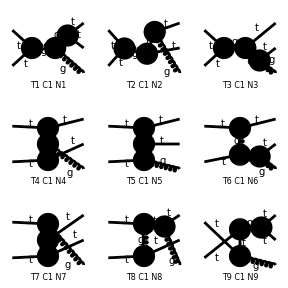

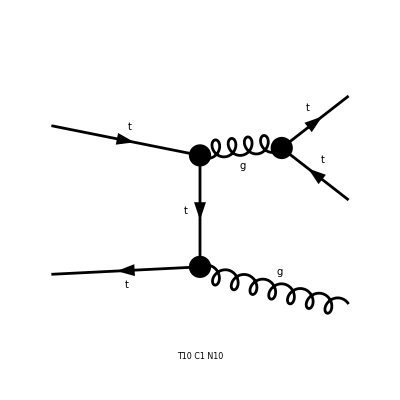

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

> Top. 4: 1 Classes amplitude

> Top. 5: 1 Classes amplitude

> Top. 6: 1 Classes amplitude

> Top. 7: 1 Classes amplitude

> Top. 8: 1 Classes amplitude

> Top. 9: 1 Classes amplitude

> Top. 10: 1 Classes amplitude

in total: 10 Classes amplitudes

-((ⅈ (ḡ)^Lor2Lor3 ((ε̄)^*)^Lor1(OutMom3) (φ(OverBar[OutMom1],FCGV(MT))).(-ⅈ g_s (γ̄)^Lor2.(γ̄)^6 T_Col3Col1^Glu6-ⅈ g_s (γ̄)^Lor2.(γ̄)^7 T_Col3Col1^Glu6).(φ(OverBar[InMom1],FCGV(MT))) (φ(-OverBar[InMom2],FCGV(MT))).(-ⅈ g_s (γ̄)^Lor3.(γ̄)^6 T_Col2Col6^Glu6-ⅈ g_s (γ̄)^Lor3.(γ̄)^7 T_Col2Col6^Glu6).(γ̄·(-OverBar[OutMom2]-OverBar[OutMom3])+FCGV(MT)).(-ⅈ g_s (γ̄)^Lor1.(γ̄)^6 T_Col6Col4^Glu5-ⅈ g_s (γ̄)^Lor1.(γ̄)^7 T_Col6Col4^Glu5).(φ(-OverBar[OutMom2],FCGV(MT))))/((-OverBar[InMom2]+OverBar[OutMom2]+OverBar[OutMom3])^2 ((OverBar[OutMom2]+OverBar[OutMom3])^2-(FCGV(MT))^2)))

-((g_s^3 T_Col3Col1^Glu6 T_Col2Col6^Glu6 T_Col6Col4^Glu5 (φ(OverBar[OutMom1],FCGV(MT))).(γ̄)^Lor2.(φ(OverBar[InMom1],FCGV(MT))) (2 (OverBar[OutMom2]·(ε̄)^*(OutMom3)) (φ(-OverBar[InMom2],FCGV(MT))).(γ̄)^Lor2.(φ(-OverBar[OutMom2],FCGV(MT)))+(φ(-OverBar[InMom2],FCGV(MT))).(γ̄)^Lor2.(γ̄·OverBar[OutMom3]).(γ̄·(ε̄)^*(OutMom3)).(φ(-OverBar[OutMom2],FCGV(MT)))))/((OverBar[InMom2]-OverBar[OutMom2]-OverBar[OutMom3])^2 ((OverBar[OutMom2]+OverBar[OutMom3])^2-(FCGV(MT))^2)))

```mathematica
tmp=InsertFields[Topology2to3,{F[3,{3}],-F[3,{3}]}->{F[3,{3}],-F[3,{3}],V[5]},ExcludeParticles->{S[__],V[1|2|3|4](*,F[3]*)}];
Paint[%,ColumnsXRows->3];
MyCreateFCAmp[tmp][[6]]
Simplify[DiracSimplify[%,DiracSubstitute67->True]]
```

## Scratch

```mathematica
DiracEvaluate[Amplitudeggttbar[[2]],repScalar2to2Prod,MomentumList]
```

(-2*Hold[BarDiracSpinorU[OutMom1[0], ToThreeVector[OutMom1], mt, OutMom1] . GammaMatrix[LorentzIndex[$AL[$3177]]] . DiracSpinorV[OutMom2[0], ToThreeVector[OutMom2], mt, OutMom2]]*
   Pair[LorentzIndex[$AL[$3177]], Momentum[Polarization[InMom1, I]]]*Pair[LorentzIndex[$AL[$3178]], Momentum[OutMom2]]*
   Pair[LorentzIndex[$AL[$3178]], Momentum[Polarization[InMom2, I]]]*SMP["g_s"]^2*SUNTF[{SUNIndex[Glu1]}, SUNFIndex[Col3], SUNFIndex[Col5]]*
   SUNTF[{SUNIndex[Glu2]}, SUNFIndex[Col5], SUNFIndex[Col4]])/(-mt^2 + t) + 
 (Hold[BarDiracSpinorU[OutMom1[0], ToThreeVector[OutMom1], mt, OutMom1] . GammaMatrix[LorentzIndex[$AL[$3176]]] . GammaMatrix[LorentzIndex[$AL[$3179]]] . 
     GammaMatrix[LorentzIndex[$AL[$3180]]] . DiracSpinorV[OutMom2[0], ToThreeVector[OutMom2], mt, OutMom2]]*Pair[LorentzIndex[$AL[$3176]], Momentum[Polarization[InMom1, I]]]*
   Pair[LorentzIndex[$AL[$3179]], Momentum[InMom2]]*Pair[LorentzIndex[$AL[$3180]], Momentum[Polarization[InMom2, I]]]*SMP["g_s"]^2*
   SUNTF[{SUNIndex[Glu1]}, SUNFIndex[Col3], SUNFIndex[Col5]]*SUNTF[{SUNIndex[Glu2]}, SUNFIndex[Col5], SUNFIndex[Col4]])/(-mt^2 + t)

```mathematica
DiracSimplify[ProjectSpinProduction[Amplitudeggttbar[[2]],0]]
SimplifyCM[%,rep2to2ProdCM,repScalar2to2Prod,AssumptionPhysicalggttbar]
FullSimplify[SimplifyCM[DiracSimplify[ExpandScalarProduct[EpsEvaluate[FCReplaceMomenta[%,{OutMom1->InMom1+InMom2-OutMom2}]]]],rep2to2ProdCM,repScalar2to2Prod,AssumptionPhysicalggttbar]]
Uncontract[%,InMom1,InMom2,OutMom1,OutMom2,Pair->All]//InputForm
```

-(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom2)) (OverBar[OutMom2]·ε̄(InMom1)) T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/(Mtt (Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))+(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom1)) (OverBar[OutMom2]·ε̄(InMom2)) T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/(Mtt (Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))+(2 ⅈ √2 (ϵ̄)^(OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2)) (OverBar[InMom2]·OverBar[OutMom2]) T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/(Mtt (Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))-(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2)) OverBar[OutMom1]^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/(Mtt (Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))-(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2)) (OverBar[OutMom1]·OverBar[OutMom2]) T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/(Mtt (Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))-(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]ε̄(InMom1)ε̄(InMom2)) (FCGV(MT))^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/(Mtt (Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))-(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2)) (FCGV(MT))^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/(Mtt (Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))-(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]ε̄(InMom1)ε̄(InMom2)) FCGV(MT) T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/((Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))-(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2)) FCGV(MT) T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/((Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))

-1/(Mtt (2 mt+Mtt) (mt^2-t))ⅈ √2 g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 ((2 mt^2+2 mt Mtt+Mtt^2) (ϵ̄)^(OverBar[InMom2]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2))+mt^2 (-(ϵ̄)^(OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2)))+2 mt (mt+Mtt) (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]ε̄(InMom1)ε̄(InMom2))+t (ϵ̄)^(OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2))+2 (OverBar[OutMom2]·ε̄(InMom1)) (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom2))-2 (OverBar[OutMom2]·ε̄(InMom2)) (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom1)))

-1/(Mtt^2 (2 mt+Mtt) (Mtt-2 p cos(theta)))ⅈ √2 g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 (2 (2 mt^2+2 mt Mtt+Mtt^2) (ϵ̄)^(OverBar[InMom2]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2))+4 mt (mt+Mtt) (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]ε̄(InMom1)ε̄(InMom2))-Mtt (Mtt-2 p cos(theta)) (ϵ̄)^(OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2))+4 (OverBar[OutMom2]·ε̄(InMom1)) (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom2))-4 (OverBar[OutMom2]·ε̄(InMom2)) (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom1)))

(4 ⅈ √2 mt^2 g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 OverBar[InMom2]^($AL($3156)) OverBar[OutMom1]^($AL($3166)) (ε̄)^($AL($3150))(InMom1) (ε̄)^($AL($3161))(InMom2) EpsLC($AL($3150),$AL($3156),$AL($3161),$AL($3166)))/(Mtt^2 (2 mt+Mtt) (Mtt-2 p cos(theta)))+(4 ⅈ √2 mt^2 g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 OverBar[InMom2]^($AL($3157)) OverBar[OutMom2]^($AL($3167)) (ε̄)^($AL($3151))(InMom1) (ε̄)^($AL($3162))(InMom2) EpsLC($AL($3151),$AL($3157),$AL($3162),$AL($3167)))/(Mtt^2 (2 mt+Mtt) (Mtt-2 p cos(theta)))-(4 ⅈ √2 g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 OverBar[InMom2]^($AL($3155)) OverBar[OutMom1]^($AL($3165)) OverBar[OutMom2]^($AL($3149)) OverBar[OutMom2]^($AL($3170)) (ε̄)^($AL($3149))(InMom1) (ε̄)^($AL($3160))(InMom2) EpsLC($AL($3155),$AL($3160),$AL($3165),$AL($3170)))/(Mtt^2 (2 mt+Mtt) (Mtt-2 p cos(theta)))-(4 ⅈ √2 g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 OverBar[InMom2]^($AL($3159)) OverBar[OutMom1]^($AL($3164)) OverBar[OutMom2]^($AL($3154)) OverBar[OutMom2]^($AL($3169)) (ε̄)^($AL($3153))(InMom1) (ε̄)^($AL($3154))(InMom2) EpsLC($AL($3153),$AL($3159),$AL($3164),$AL($3169)))/(Mtt^2 (2 mt+Mtt) (Mtt-2 p cos(theta)))+(ⅈ √2 g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 OverBar[OutMom1]^($AL($3163)) OverBar[OutMom2]^($AL($3168)) (ε̄)^($AL($3152))(InMom1) (ε̄)^($AL($3158))(InMom2) EpsLC($AL($3152),$AL($3158),$AL($3163),$AL($3168)))/(Mtt (2 mt+Mtt))+(4 ⅈ √2 mt g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 OverBar[InMom2]^($AL($3156)) OverBar[OutMom1]^($AL($3166)) (ε̄)^($AL($3150))(InMom1) (ε̄)^($AL($3161))(InMom2) EpsLC($AL($3150),$AL($3156),$AL($3161),$AL($3166)))/(Mtt (2 mt+Mtt) (Mtt-2 p cos(theta)))+(4 ⅈ √2 mt g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 OverBar[InMom2]^($AL($3157)) OverBar[OutMom2]^($AL($3167)) (ε̄)^($AL($3151))(InMom1) (ε̄)^($AL($3162))(InMom2) EpsLC($AL($3151),$AL($3157),$AL($3162),$AL($3167)))/(Mtt (2 mt+Mtt) (Mtt-2 p cos(theta)))+(2 ⅈ √2 g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 OverBar[InMom2]^($AL($3157)) OverBar[OutMom2]^($AL($3167)) (ε̄)^($AL($3151))(InMom1) (ε̄)^($AL($3162))(InMom2) EpsLC($AL($3151),$AL($3157),$AL($3162),$AL($3167)))/((2 mt+Mtt) (Mtt-2 p cos(theta)))

((4*I)*Sqrt[2]*Eps[LorentzIndex[$AL[$3131]], LorentzIndex[$AL[$3135]], LorentzIndex[$AL[$3140]], LorentzIndex[$AL[$3144]]]*Pair[LorentzIndex[$AL[$3127]], Momentum[OutMom2]]*
   Pair[LorentzIndex[$AL[$3127]], Momentum[Polarization[InMom1, I]]]*Pair[LorentzIndex[$AL[$3131]], Momentum[OutMom2]]*Pair[LorentzIndex[$AL[$3135]], Momentum[OutMom1]]*
   Pair[LorentzIndex[$AL[$3140]], Momentum[InMom2]]*Pair[LorentzIndex[$AL[$3144]], Momentum[Polarization[InMom2, I]]]*SMP["g_s"]^2*
   SUNTF[{SUNIndex[Glu1]}, SUNFIndex[Col3], SUNFIndex[Col5]]*SUNTF[{SUNIndex[Glu2]}, SUNFIndex[Col5], SUNFIndex[Col4]])/(Mtt^2*(2*mt + Mtt)*(Mtt - 2*p*Cos[theta])) + 
 (I*Sqrt[2]*Eps[LorentzIndex[$AL[$3130]], LorentzIndex[$AL[$3134]], LorentzIndex[$AL[$3139]], LorentzIndex[$AL[$3145]]]*Pair[LorentzIndex[$AL[$3130]], Momentum[OutMom2]]*
   Pair[LorentzIndex[$AL[$3134]], Momentum[OutMom1]]*Pair[LorentzIndex[$AL[$3139]], Momentum[Polarization[InMom2, I]]]*
   Pair[LorentzIndex[$AL[$3145]], Momentum[Polarization[InMom1, I]]]*SMP["g_s"]^2*SUNTF[{SUNIndex[Glu1]}, SUNFIndex[Col3], SUNFIndex[Col5]]*
   SUNTF[{SUNIndex[Glu2]}, SUNFIndex[Col5], SUNFIndex[Col4]])/(Mtt*(2*mt + Mtt)) - 
 ((4*I)*Sqrt[2]*Eps[LorentzIndex[$AL[$3132]], LorentzIndex[$AL[$3136]], LorentzIndex[$AL[$3141]], LorentzIndex[$AL[$3146]]]*Pair[LorentzIndex[$AL[$3128]], Momentum[OutMom2]]*
   Pair[LorentzIndex[$AL[$3128]], Momentum[Polarization[InMom2, I]]]*Pair[LorentzIndex[$AL[$3132]], Momentum[OutMom2]]*Pair[LorentzIndex[$AL[$3136]], Momentum[OutMom1]]*
   Pair[LorentzIndex[$AL[$3141]], Momentum[InMom2]]*Pair[LorentzIndex[$AL[$3146]], Momentum[Polarization[InMom1, I]]]*SMP["g_s"]^2*
   SUNTF[{SUNIndex[Glu1]}, SUNFIndex[Col3], SUNFIndex[Col5]]*SUNTF[{SUNIndex[Glu2]}, SUNFIndex[Col5], SUNFIndex[Col4]])/(Mtt^2*(2*mt + Mtt)*(Mtt - 2*p*Cos[theta])) - 
 ((2*I)*Sqrt[2]*(2*mt^2 + 2*mt*Mtt + Mtt^2)*Eps[LorentzIndex[$AL[$3129]], LorentzIndex[$AL[$3137]], LorentzIndex[$AL[$3142]], LorentzIndex[$AL[$3147]]]*
   Pair[LorentzIndex[$AL[$3129]], Momentum[OutMom2]]*Pair[LorentzIndex[$AL[$3137]], Momentum[InMom2]]*Pair[LorentzIndex[$AL[$3142]], Momentum[Polarization[InMom2, I]]]*
   Pair[LorentzIndex[$AL[$3147]], Momentum[Polarization[InMom1, I]]]*SMP["g_s"]^2*SUNTF[{SUNIndex[Glu1]}, SUNFIndex[Col3], SUNFIndex[Col5]]*
   SUNTF[{SUNIndex[Glu2]}, SUNFIndex[Col5], SUNFIndex[Col4]])/(Mtt^2*(2*mt + Mtt)*(Mtt - 2*p*Cos[theta])) - 
 ((4*I)*Sqrt[2]*mt*(mt + Mtt)*Eps[LorentzIndex[$AL[$3133]], LorentzIndex[$AL[$3138]], LorentzIndex[$AL[$3143]], LorentzIndex[$AL[$3148]]]*
   Pair[LorentzIndex[$AL[$3133]], Momentum[OutMom1]]*Pair[LorentzIndex[$AL[$3138]], Momentum[InMom2]]*Pair[LorentzIndex[$AL[$3143]], Momentum[Polarization[InMom2, I]]]*
   Pair[LorentzIndex[$AL[$3148]], Momentum[Polarization[InMom1, I]]]*SMP["g_s"]^2*SUNTF[{SUNIndex[Glu1]}, SUNFIndex[Col3], SUNFIndex[Col5]]*
   SUNTF[{SUNIndex[Glu2]}, SUNFIndex[Col5], SUNFIndex[Col4]])/(Mtt^2*(2*mt + Mtt)*(Mtt - 2*p*Cos[theta]))

```mathematica
DiracSimplify[ProjectSpinProduction[Amplitudeggttbar[[2]],0]]
SimplifyCM[%,rep2to2ProdCM,repScalar2to2Prod,AssumptionPhysicalggttbar]
FullSimplify[SimplifyCM[DiracSimplify[ExpandScalarProduct[EpsEvaluate[FCReplaceMomenta[%,{OutMom1->InMom1+InMom2-OutMom2}]]]],rep2to2ProdCM,repScalar2to2Prod,AssumptionPhysicalggttbar]]
Uncontract[%%,InMom1,InMom2,OutMom1,OutMom2,Pair->All]
DiracEvaluate[%%,repScalar2to2Prod,MomentumList]
SimplifyCM[%,rep2to2ProdCM,repScalar2to2Prod,AssumptionPhysicalggttbar]
```

-(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom2)) (OverBar[OutMom2]·ε̄(InMom1)) T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/(Mtt (Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))+(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom1)) (OverBar[OutMom2]·ε̄(InMom2)) T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/(Mtt (Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))+(2 ⅈ √2 (ϵ̄)^(OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2)) (OverBar[InMom2]·OverBar[OutMom2]) T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/(Mtt (Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))-(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2)) OverBar[OutMom1]^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/(Mtt (Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))-(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2)) (OverBar[OutMom1]·OverBar[OutMom2]) T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/(Mtt (Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))-(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]ε̄(InMom1)ε̄(InMom2)) (FCGV(MT))^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/(Mtt (Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))-(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2)) (FCGV(MT))^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/(Mtt (Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))-(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]ε̄(InMom1)ε̄(InMom2)) FCGV(MT) T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/((Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))-(2 ⅈ √2 (ϵ̄)^(OverBar[InMom2]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2)) FCGV(MT) T_Col3Col5^Glu1 T_Col5Col4^Glu2 g_s^2)/((Mtt+2 FCGV(MT)) ((FCGV(MT))^2-OverBar[InMom2]^2+2 (OverBar[InMom2]·OverBar[OutMom2])-OverBar[OutMom2]^2))

-1/(Mtt (2 mt+Mtt) (mt^2-t))ⅈ √2 g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 ((2 mt^2+2 mt Mtt+Mtt^2) (ϵ̄)^(OverBar[InMom2]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2))+mt^2 (-(ϵ̄)^(OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2)))+2 mt (mt+Mtt) (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]ε̄(InMom1)ε̄(InMom2))+t (ϵ̄)^(OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2))+2 (OverBar[OutMom2]·ε̄(InMom1)) (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom2))-2 (OverBar[OutMom2]·ε̄(InMom2)) (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom1)))

-1/(Mtt^2 (2 mt+Mtt) (Mtt-2 p cos(theta)))ⅈ √2 g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 (2 (2 mt^2+2 mt Mtt+Mtt^2) (ϵ̄)^(OverBar[InMom2]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2))+4 mt (mt+Mtt) (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]ε̄(InMom1)ε̄(InMom2))-Mtt (Mtt-2 p cos(theta)) (ϵ̄)^(OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom1)ε̄(InMom2))+4 (OverBar[OutMom2]·ε̄(InMom1)) (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom2))-4 (OverBar[OutMom2]·ε̄(InMom2)) (ϵ̄)^(OverBar[InMom2]OverBar[OutMom1]OverBar[OutMom2]ε̄(InMom1)))

-(ⅈ √2 g_s^2 (2 mt^2+2 mt Mtt+Mtt^2) T_Col3Col5^Glu1 T_Col5Col4^Glu2 OverBar[InMom2]^($AL($3297)) OverBar[OutMom2]^($AL($3287)) (ε̄)^($AL($3309))(InMom1) (ε̄)^($AL($3303))(InMom2) (ϵ̄)^($AL($3287)$AL($3297)$AL($3303)$AL($3309)))/(Mtt (2 mt+Mtt) (mt^2-t))+(2 ⅈ √2 g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 OverBar[InMom2]^($AL($3301)) OverBar[OutMom1]^($AL($3295)) OverBar[OutMom2]^($AL($3285)) OverBar[OutMom2]^($AL($3290)) (ε̄)^($AL($3285))(InMom1) (ε̄)^($AL($3305))(InMom2) (ϵ̄)^($AL($3290)$AL($3295)$AL($3301)$AL($3305)))/(Mtt (2 mt+Mtt) (mt^2-t))-(2 ⅈ √2 g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 OverBar[InMom2]^($AL($3302)) OverBar[OutMom1]^($AL($3296)) OverBar[OutMom2]^($AL($3286)) OverBar[OutMom2]^($AL($3291)) (ε̄)^($AL($3308))(InMom1) (ε̄)^($AL($3286))(InMom2) (ϵ̄)^($AL($3291)$AL($3296)$AL($3302)$AL($3308)))/(Mtt (2 mt+Mtt) (mt^2-t))+(ⅈ √2 mt^2 g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 OverBar[OutMom1]^($AL($3293)) OverBar[OutMom2]^($AL($3288)) (ε̄)^($AL($3306))(InMom1) (ε̄)^($AL($3299))(InMom2) (ϵ̄)^($AL($3288)$AL($3293)$AL($3299)$AL($3306)))/(Mtt (2 mt+Mtt) (mt^2-t))-(ⅈ √2 t g_s^2 T_Col3Col5^Glu1 T_Col5Col4^Glu2 OverBar[OutMom1]^($AL($3294)) OverBar[OutMom2]^($AL($3289)) (ε̄)^($AL($3307))(InMom1) (ε̄)^($AL($3300))(InMom2) (ϵ̄)^($AL($3289)$AL($3294)$AL($3300)$AL($3307)))/(Mtt (2 mt+Mtt) (mt^2-t))-(2 ⅈ √2 mt g_s^2 (mt+Mtt) T_Col3Col5^Glu1 T_Col5Col4^Glu2 OverBar[InMom2]^($AL($3298)) OverBar[OutMom1]^($AL($3292)) (ε̄)^($AL($3310))(InMom1) (ε̄)^($AL($3304))(InMom2) (ϵ̄)^($AL($3292)$AL($3298)$AL($3304)$AL($3310)))/(Mtt (2 mt+Mtt) (mt^2-t))

4 {$AL($3315),$AL($3321),$AL($3326),$AL($3331),$AL($3316)}

4 {$AL($3314),$AL($3320),$AL($3325),$AL($3330)}

4 {$AL($3317),$AL($3322),$AL($3327),$AL($3332),$AL($3311)}

4 {$AL($3312),$AL($3318),$AL($3323),$AL($3328)}

4 {$AL($3312),$AL($3318),$AL($3323),$AL($3328)}

4 {$AL($3313),$AL($3319),$AL($3324),$AL($3329)}

4 {$AL($3313),$AL($3319),$AL($3324),$AL($3329)}

4 {$AL($3313),$AL($3319),$AL($3324),$AL($3329)}

(g_s^2 (4 mt^2+4 mt Mtt+Mtt^2-4 p^2) T_Col3Col5^Glu1 T_Col5Col4^Glu2 (Pol(InMom1,plus) Pol(InMom2,minus)-Pol(InMom1,minus) Pol(InMom2,plus)))/(√2 (2 mt+Mtt) (Mtt-2 p cos(theta)))

```mathematica
Eps[0,1,2,3]
```

0

```mathematica
Eps[1,2,3,4]
```

(ϵ̄)^1234

```mathematica
LeviCivita[0,1,2,3]
```

(ϵ̄)^0123

```mathematica
1.8*^-26/5.2*^-16
```

3.46154×10^-11

```mathematica
?SphericalHarmonicExpansion
```

```mathematica
ProjectSphericalHarmonics[Cos[theta],1,0]
```

2 √(π/3)

```mathematica
Sqrt[Pi]/Gamma[1+1/2]*1/Sqrt[3]
```

2/(√3)